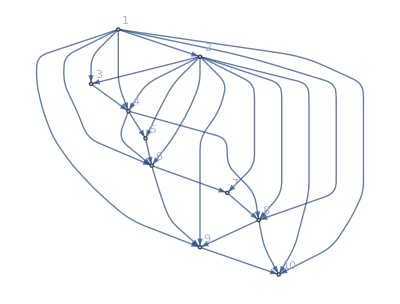

26

```mathematica
n=10;
flow=100;
g= Graph[
Table[i,{i,n}],
Join[
Flatten[
Table[i->j,{i,n-2},{j,RandomSample[Range[i+2,n],RandomInteger[n-i-1]]}]],
Table[i->i+1,{i,1,n-1}]
],
VertexLabels->Table[i->i,{i,n}]
]
val=Sort[EdgeList[g]]; (*care arce sunt in graf*)
m=EdgeCount[g] (*numarul de arce*)

A=IncidenceMatrix[g]; (*matricea de incidenta*)
b=Table[{0,0},n];b⟦1,1⟧=-80;b⟦n,1⟧=80; (*m[rimea fluxului transmis din sursa spre destinatie*)
                                                (* b⟦1,2⟧=-1;b⟦n,2⟧=1;*)
X=Array[x,m];

lu=Table[{0,100},{i,m}];

γ=Table[RandomInteger[{1,5}],m];
δ=Table[RandomInteger[{1,5}],m];
f[j_Integer,x_]:=Piecewise[{{γ⟦j⟧ x, x≤δ⟦j⟧}, {γ⟦j⟧ δ⟦j⟧, x>δ⟦j⟧}, {0, True}}]
fd[j_Integer,x_]:=Piecewise[{{f[j,x]/x, x>0}, {γ⟦j⟧, x==0}, {0, True}}]
```

## Alg P2

```mathematica
Do[
Print[Style["Test ","Section"],Style[bigCount,"Section"]];
thisTimer=Timing[
 min=10000;
solmin={};
perm=Gather[val,First[#1]==First[#2]&]⟦All,All,2⟧; (* Lista de adiacenta --- Are nevoie ca lista de muchii sa fie sortata *)
Do[perm⟦i⟧=RandomSample[perm⟦i⟧],{i,n-1}]; (* Lista randomizata *)
cc=Table[Length[perm⟦i⟧],{i,n-1}]; (* Lista care arata gradul fiecarui nod (cite muchii ies din el) *)
v=Table[{0, Table[Normalize[RandomReal[{0,1},cc⟦i⟧],Total],{i,n-1}]}, {k,4*n}] ; (* Cromozomii initiali *)

(* Lista de coeficienti care vor fi folositi pentru a determina fluxul care va merge pe fiecare muchie *)
pos = SparseArray[MapIndexed[#⟦1⟧*n+#⟦2⟧->#2⟦1⟧&,val]]; (* Creaza un hash map care codeaza muchia cu pozitia ei in lista de muchii ---- Modul de codare este i*n + j pentru muchia i -> j *)
prev=-1000; genEps=0.1; (* variabile ajutatoare pentru conditia de oprire a programului *)

Do[
If[v⟦i⟧⟦1⟧>0,Continue[]];
flux=Table[0,n]; (* Acest tabel retine fluxul care intra in fiecare nod *)
flux⟦1⟧=flow;
Do[
flux⟦perm⟦j,ii⟧⟧+=flux⟦j⟧*v⟦i,2,j,ii⟧; (* Din nodul j este impins fluxul spre alte noduri *)
v⟦i,1⟧+=f[pos⟦j*n+perm⟦j,ii⟧⟧,flux⟦j⟧*v⟦i,2,j,ii⟧]; (* solutia acestui cromozom este actualizata *)
,{j,n-1},{ii,cc⟦j⟧}]
,{i,4*n}];


(*Print["**********************************************************************************"];
Print["Pasul 1. Initializarea unei matrici a ratelor de flux si a unei populatii intiale:"];
Print[v];*)
counter = 1;

While[Abs[v⟦1⟧⟦1⟧-prev]>genEps,(* Verifica daca ultimele 2 cele mai bune solutii sunt aproape egale *)
prev=v⟦1⟧⟦1⟧;
(*Print[v⟦1⟧⟦1⟧];*)
Print["------------------------------------------------------------------"];
Print["Iteratia ", counter];

counter++;
(*Afisam Populatia si evaluarea functiei populatiei*)
(*Print["Pasul 2. Populatia si evaluarea functiei obiectiv:"];*)

v=Take[v,2*n]; (* Ia jumatatea de solutii care sunt cele mai bune *)
(*Print["Pasul 3. Parintii care vor fi folositi la incrucisare:"];
Print[v];*)
v=Join[v,Flatten[Table[
zz=RandomInteger[{1,n-2}];
{{0,Join[Take[v⟦i,2⟧,zz],Drop[v⟦i+1,2⟧,zz]]},{0,Join[Take[v⟦i+1,2⟧,zz],Drop[v⟦i,2⟧,zz]]}},
{i,1,2*n,2}],1] (* Formeaza copii taind la zz *)
];
(*Print["Pasul 4. Urmasii:"];
Print[Take[v,-2*n]];*)
Do[If[RandomInteger[{1,100}]==1, j=RandomInteger[{1,n-1}];v⟦i,2,j⟧=Normalize[RandomReal[{0,1},cc⟦j⟧],Total]],{i,n+1,2*n}] ;(* Mutatii *)
Do[
If[v⟦i⟧⟦1⟧>0,Continue[]];
flux=Table[0,n]; (* Acest tabel retine fluxul care intra in fiecare nod *)
flux⟦1⟧=flow;
Do[
flux⟦perm⟦j,ii⟧⟧+=flux⟦j⟧*v⟦i,2,j,ii⟧; (* Din nodul j este impins fluxul spre alte noduri *)
v⟦i,1⟧+=f[pos⟦j*n+perm⟦j,ii⟧⟧,flux⟦j⟧*v⟦i,2,j,ii⟧]; (* solutia acestui cromozom este actualizata *)
,{j,n-1},{ii,cc⟦j⟧}]
,{i,2*n,4*n}];

(*Print["Pasul 5. Populatia noua dupa mutatii:"];
Print[v];
Print[v⟦1⟧⟦1⟧];

Print["Solutiile asociate cromozomilor"];*)
solutii = Table[0,4*n];
Do[
flux=Table[0,n];
flux⟦1⟧=flow;
X=Table[0,m];
Do[
flux⟦perm⟦j,ii⟧⟧+=flux⟦j⟧*v⟦k,2,j,ii⟧; 
X⟦pos⟦j*n+perm⟦j,ii⟧⟧⟧=flux⟦j⟧*v⟦k,2,j,ii⟧;
,{j,n-1},{ii,cc⟦j⟧}
];
solutii⟦k⟧ = {v⟦k,1⟧, X};
,{k,4*n}];
(*Print[solutii];*)
Print["Parintii si urmasii ",v];
Print["Cel mai bun cromozom ",v[[Ordering[solutii,1]]]];
Print["Cea mai buna solutie ",solutii[[Ordering[solutii,1]]]];
Print["Functia obiectiv totala ",Sum[v⟦i,1⟧,{i,4*n}]];
v=v[[Ordering[solutii]]];
];

(* Gasirea solutiei finale *)
flux=Table[0,n];
flux⟦1⟧=flow;
X=Table[0,m];
Do[
flux⟦perm⟦j,ii⟧⟧+=flux⟦j⟧*v⟦1,2,j,ii⟧; 
X⟦pos⟦j*n+perm⟦j,ii⟧⟧⟧=flux⟦j⟧*v⟦1,2,j,ii⟧;
,{j,n-1},{ii,cc⟦j⟧}
]
(*{Print[v⟦1,1⟧,X];}
Print["    "]*)
];
Print[thisTimer];
,{bigCount,1,10}]
```

Test 1

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{157.918,{{0.154116,0.203101,0.143483,0.197608,0.0109433,0.186154,0.104595},{0.236094,0.202864,0.0084507,0.169907,0.196748,0.0720933,0.0865374,0.0273044},{1.},{0.0476952,0.354896,0.597409},{1.},{0.565219,0.434781},{1.},{0.678708,0.321292},{1.}}},{145.725,{{0.0740148,0.0532562,0.156108,0.323902,0.0334031,0.285158,0.0741582},{0.00154045,0.0320604,0.154217,0.194489,0.112725,0.225184,0.220998,0.0587869},{1.},{0.556819,0.357245,0.0859363},{1.},{0.698632,0.301368},{1.},{0.0145668,0.985433},{1.}}},{187.675,{{0.177005,0.0326762,0.168212,0.186763,0.0275372,0.20842,0.199386},{0.0468189,0.120298,0.122,0.185624,0.255896,0.236246,0.0204238,0.0126935},{1.},{0.391883,0.0422796,0.565838},{1.},{0.880465,0.119535},{1.},{0.735613,0.264387},{1.}}},{178.51,{{0.144755,0.187246,0.157651,0.149065,0.0613626,0.139092,0.160828},{0.114893,0.135485,0.0232207,0.0809518,0.162617,0.226888,0.0915959,0.164349},{1.},{0.000320369,0.560806,0.438874},{1.},{0.606981,0.393019},{1.},{0.575409,0.424591},{1.}}},{158.107,{{0.14443,0.358945,0.0895854,0.14669,0.0781254,0.117877,0.0643476},{0.0499766,0.0095845,0.162018,0.0229358,0.259159,0.218817,0.133837,0.143671},{1.},{0.647656,0.0764022,0.275942},{1.},{0.538947,0.461053},{1.},{0.650155,0.349845},{1.}}},{156.875,{{0.10524,0.175841,0.170173,0.204761,0.0886671,0.182425,0.072893},{0.0141545,0.250094,0.0730518,0.043864,0.180105,0.0825256,0.110334,0.245871},{1.},{0.428335,0.121981,0.449684},{1.},{0.312006,0.687994},{1.},{0.699846,0.300154},{1.}}},{126.463,{{0.054531,0.221245,0.310615,0.238263,0.0591682,0.0652306,0.0509468},{0.185077,0.133296,0.0581833,0.0365161,0.185108,0.168932,0.170256,0.0626316},{1.},{0.222195,0.626586,0.15122},{1.},{0.314617,0.685383},{1.},{0.996446,0.00355412},{1.}}},{194.918,{{0.0820165,0.00518405,0.22812,0.144638,0.112224,0.228507,0.19931},{0.0041244,0.017179,0.173102,0.219671,0.0986078,0.209391,0.158325,0.119599},{1.},{0.348486,0.216943,0.434572},{1.},{0.712258,0.287742},{1.},{0.0553423,0.944658},{1.}}},{149.965,{{0.0674643,0.212768,0.201636,0.00921462,0.244766,0.208796,0.055355},{0.163297,0.121326,0.193042,0.0331121,0.0753598,0.126367,0.150966,0.13653},{1.},{0.0507358,0.737161,0.212103},{1.},{0.535046,0.464954},{1.},{0.274138,0.725862},{1.}}},{120.508,{{0.320353,0.0195635,0.0647455,0.298908,0.25863,0.0177718,0.0200278},{0.0637696,0.254962,0.00540648,0.191165,0.0610372,0.0871228,0.146971,0.189565},{1.},{0.0636482,0.509428,0.426924},{1.},{0.404774,0.595226},{1.},{0.546949,0.453051},{1.}}},{140.053,{{0.181556,0.2976,0.0877879,0.153282,0.0493476,0.203225,0.0272016},{0.176082,0.0627122,0.0143574,0.209005,0.203774,0.151696,0.159135,0.0232393},{1.},{0.569396,0.275595,0.15501},{1.},{0.725703,0.274297},{1.},{0.298425,0.701575},{1.}}},{182.724,{{0.251358,0.184545,0.0115665,0.124079,0.0779956,0.192866,0.15759},{0.131915,0.0597131,0.0945302,0.0126787,0.191552,0.202823,0.17391,0.132879},{1.},{0.35075,0.079461,0.569789},{1.},{0.800956,0.199044},{1.},{0.528983,0.471017},{1.}}},{204.266,{{0.231366,0.0637498,0.0388151,0.285733,0.103691,0.0860749,0.19057},{0.149826,0.0775748,0.195409,0.206529,0.0385092,0.193949,0.0891184,0.0490853},{1.},{0.256581,0.510735,0.232684},{1.},{0.624297,0.375703},{1.},{0.700236,0.299764},{1.}}},{106.771,{{0.102117,0.361493,0.0166916,0.137274,0.129065,0.249084,0.00427369},{0.186516,0.149803,0.0481728,0.0616885,0.120399,0.223978,0.156204,0.0532394},{1.},{0.585411,0.380028,0.0345609},{1.},{0.236277,0.763723},{1.},{0.626947,0.373053},{1.}}},{181.056,{{0.196107,0.0588076,0.201812,0.0431543,0.200289,0.161154,0.138676},{0.306329,0.0215941,0.29058,0.2287,0.0213239,0.00460219,0.0575819,0.0692891},{1.},{0.334767,0.0811748,0.584059},{1.},{0.608194,0.391806},{1.},{0.262308,0.737692},{1.}}},{192.73,{{0.051742,0.0476578,0.104204,0.0237344,0.16439,0.397688,0.210584},{0.0346001,0.109874,0.00288799,0.223335,0.134157,0.0617224,0.229516,0.203908},{1.},{0.808904,0.085208,0.105888},{1.},{0.444787,0.555213},{1.},{0.474719,0.525281},{1.}}},{186.661,{{0.0827845,0.201103,0.195392,0.0947804,0.177423,0.103696,0.144821},{0.09581,0.103903,0.214169,0.100157,0.0348374,0.106668,0.212013,0.132442},{1.},{0.426315,0.110939,0.462746},{1.},{0.505032,0.494968},{1.},{0.413669,0.586331},{1.}}},{178.643,{{0.084629,0.13156,0.217227,0.246529,0.0948404,0.0934621,0.131753},{0.254258,0.0330269,0.117377,0.0887393,0.0693471,0.202905,0.118719,0.115627},{1.},{0.338108,0.325716,0.336175},{1.},{0.694281,0.305719},{1.},{0.569881,0.430119},{1.}}},{204.572,{{0.145554,0.093262,0.0988393,0.123605,0.201023,0.121531,0.216185},{0.101614,0.156923,0.166891,0.128485,0.10222,0.0733502,0.102772,0.167744},{1.},{0.408571,0.255628,0.335801},{1.},{0.623414,0.376586},{1.},{0.384968,0.615032},{1.}}},{184.018,{{0.0826475,0.00395209,0.194114,0.182848,0.0673309,0.259058,0.21005},{0.0997209,0.0995851,0.201301,0.135398,0.115313,0.106828,0.199656,0.0421977},{1.},{0.123933,0.177391,0.698676},{1.},{0.275678,0.724322},{1.},{0.988121,0.0118786},{1.}}},{157.031,{{0.154116,0.203101,0.143483,0.197608,0.0109433,0.186154,0.104595},{0.00154045,0.0320604,0.154217,0.194489,0.112725,0.225184,0.220998,0.0587869},{1.},{0.556819,0.357245,0.0859363},{1.},{0.698632,0.301368},{1.},{0.0145668,0.985433},{1.}}},{152.764,{{0.0740148,0.0532562,0.156108,0.323902,0.0334031,0.285158,0.0741582},{0.236094,0.202864,0.0084507,0.169907,0.196748,0.0720933,0.0865374,0.0273044},{1.},{0.0476952,0.354896,0.597409},{1.},{0.565219,0.434781},{1.},{0.678708,0.321292},{1.}}},{190.535,{{0.177005,0.0326762,0.168212,0.186763,0.0275372,0.20842,0.199386},{0.0468189,0.120298,0.122,0.185624,0.255896,0.236246,0.0204238,0.0126935},{1.},{0.391883,0.0422796,0.565838},{1.},{0.880465,0.119535},{1.},{0.575409,0.424591},{1.}}},{178.51,{{0.144755,0.187246,0.157651,0.149065,0.0613626,0.139092,0.160828},{0.114893,0.135485,0.0232207,0.0809518,0.162617,0.226888,0.0915959,0.164349},{1.},{0.000320369,0.560806,0.438874},{1.},{0.606981,0.393019},{1.},{0.735613,0.264387},{1.}}},{158.107,{{0.14443,0.358945,0.0895854,0.14669,0.0781254,0.117877,0.0643476},{0.0499766,0.0095845,0.162018,0.0229358,0.259159,0.218817,0.133837,0.143671},{1.},{0.428335,0.121981,0.449684},{1.},{0.312006,0.687994},{1.},{0.699846,0.300154},{1.}}},{156.875,{{0.10524,0.175841,0.170173,0.204761,0.0886671,0.182425,0.072893},{0.0141545,0.250094,0.0730518,0.043864,0.180105,0.0825256,0.110334,0.245871},{1.},{0.647656,0.0764022,0.275942},{1.},{0.538947,0.461053},{1.},{0.650155,0.349845},{1.}}},{146.271,{{0.054531,0.221245,0.310615,0.238263,0.0591682,0.0652306,0.0509468},{0.185077,0.133296,0.0581833,0.0365161,0.185108,0.168932,0.170256,0.0626316},{1.},{0.348486,0.216943,0.434572},{1.},{0.712258,0.287742},{1.},{0.0553423,0.944658},{1.}}},{192.453,{{0.0820165,0.00518405,0.22812,0.144638,0.112224,0.228507,0.19931},{0.0041244,0.017179,0.173102,0.219671,0.0986078,0.209391,0.158325,0.119599},{1.},{0.222195,0.626586,0.15122},{1.},{0.314617,0.685383},{1.},{0.996446,0.00355412},{1.}}},{149.965,{{0.0674643,0.212768,0.201636,0.00921462,0.244766,0.208796,0.055355},{0.163297,0.121326,0.193042,0.0331121,0.0753598,0.126367,0.150966,0.13653},{1.},{0.0507358,0.737161,0.212103},{1.},{0.404774,0.595226},{1.},{0.546949,0.453051},{1.}}},{120.508,{{0.320353,0.0195635,0.0647455,0.298908,0.25863,0.0177718,0.0200278},{0.0637696,0.254962,0.00540648,0.191165,0.0610372,0.0871228,0.146971,0.189565},{1.},{0.0636482,0.509428,0.426924},{1.},{0.535046,0.464954},{1.},{0.274138,0.725862},{1.}}},{140.053,{{0.181556,0.2976,0.0877879,0.153282,0.0493476,0.203225,0.0272016},{0.176082,0.0627122,0.0143574,0.209005,0.203774,0.151696,0.159135,0.0232393},{1.},{0.569396,0.275595,0.15501},{1.},{0.725703,0.274297},{1.},{0.528983,0.471017},{1.}}},{182.724,{{0.251358,0.184545,0.0115665,0.124079,0.0779956,0.192866,0.15759},{0.131915,0.0597131,0.0945302,0.0126787,0.191552,0.202823,0.17391,0.132879},{1.},{0.35075,0.079461,0.569789},{1.},{0.800956,0.199044},{1.},{0.298425,0.701575},{1.}}},{185.372,{{0.231366,0.0637498,0.0388151,0.285733,0.103691,0.0860749,0.19057},{0.149826,0.0775748,0.195409,0.206529,0.0385092,0.193949,0.0891184,0.0490853},{1.},{0.585411,0.380028,0.0345609},{1.},{0.236277,0.763723},{1.},{0.626947,0.373053},{1.}}},{125.679,{{0.102117,0.361493,0.0166916,0.137274,0.129065,0.249084,0.00427369},{0.186516,0.149803,0.0481728,0.0616885,0.120399,0.223978,0.156204,0.0532394},{1.},{0.256581,0.510735,0.232684},{1.},{0.624297,0.375703},{1.},{0.700236,0.299764},{1.}}},{181.056,{{0.196107,0.0588076,0.201812,0.0431543,0.200289,0.161154,0.138676},{0.306329,0.0215941,0.29058,0.2287,0.0213239,0.00460219,0.0575819,0.0692891},{1.},{0.334767,0.0811748,0.584059},{1.},{0.608194,0.391806},{1.},{0.474719,0.525281},{1.}}},{192.73,{{0.051742,0.0476578,0.104204,0.0237344,0.16439,0.397688,0.210584},{0.0346001,0.109874,0.00288799,0.223335,0.134157,0.0617224,0.229516,0.203908},{1.},{0.808904,0.085208,0.105888},{1.},{0.444787,0.555213},{1.},{0.262308,0.737692},{1.}}},{186.661,{{0.0827845,0.201103,0.195392,0.0947804,0.177423,0.103696,0.144821},{0.09581,0.103903,0.214169,0.100157,0.0348374,0.106668,0.212013,0.132442},{1.},{0.426315,0.110939,0.462746},{1.},{0.694281,0.305719},{1.},{0.569881,0.430119},{1.}}},{178.643,{{0.084629,0.13156,0.217227,0.246529,0.0948404,0.0934621,0.131753},{0.254258,0.0330269,0.117377,0.0887393,0.0693471,0.202905,0.118719,0.115627},{1.},{0.338108,0.325716,0.336175},{1.},{0.505032,0.494968},{1.},{0.413669,0.586331},{1.}}},{195.811,{{0.145554,0.093262,0.0988393,0.123605,0.201023,0.121531,0.216185},{0.101614,0.156923,0.166891,0.128485,0.10222,0.0733502,0.102772,0.167744},{1.},{0.408571,0.255628,0.335801},{1.},{0.275678,0.724322},{1.},{0.988121,0.0118786},{1.}}},{192.735,{{0.0826475,0.00395209,0.194114,0.182848,0.0673309,0.259058,0.21005},{0.0997209,0.0995851,0.201301,0.135398,0.115313,0.106828,0.199656,0.0421977},{1.},{0.123933,0.177391,0.698676},{1.},{0.623414,0.376586},{1.},{0.384968,0.615032},{1.}}}}

Cel mai bun cromozom {{106.771,{{0.102117,0.361493,0.0166916,0.137274,0.129065,0.249084,0.00427369},{0.186516,0.149803,0.0481728,0.0616885,0.120399,0.223978,0.156204,0.0532394},{1.},{0.585411,0.380028,0.0345609},{1.},{0.236277,0.763723},{1.},{0.626947,0.373053},{1.}}}}

Cea mai buna solutie {{106.771,{0.427369,24.9084,10.2117,1.66916,36.1493,12.9065,13.7274,0.0797111,0.0514546,0.064021,0.0205876,0.0227529,0.0667567,0.0957211,0.0263638,24.9881,20.6365,1.21832,13.3965,20.7005,18.0304,5.57818,18.0532,42.4228,25.2429,61.0033}}}

Functia obiectiv totala 6702.64

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{106.771,{{0.102117,0.361493,0.0166916,0.137274,0.129065,0.249084,0.00427369},{0.186516,0.149803,0.0481728,0.0616885,0.120399,0.223978,0.156204,0.0532394},{1.},{0.585411,0.380028,0.0345609},{1.},{0.236277,0.763723},{1.},{0.626947,0.373053},{1.}}},{120.508,{{0.320353,0.0195635,0.0647455,0.298908,0.25863,0.0177718,0.0200278},{0.0637696,0.254962,0.00540648,0.191165,0.0610372,0.0871228,0.146971,0.189565},{1.},{0.0636482,0.509428,0.426924},{1.},{0.535046,0.464954},{1.},{0.274138,0.725862},{1.}}},{120.508,{{0.320353,0.0195635,0.0647455,0.298908,0.25863,0.0177718,0.0200278},{0.0637696,0.254962,0.00540648,0.191165,0.0610372,0.0871228,0.146971,0.189565},{1.},{0.0636482,0.509428,0.426924},{1.},{0.404774,0.595226},{1.},{0.546949,0.453051},{1.}}},{125.679,{{0.102117,0.361493,0.0166916,0.137274,0.129065,0.249084,0.00427369},{0.186516,0.149803,0.0481728,0.0616885,0.120399,0.223978,0.156204,0.0532394},{1.},{0.256581,0.510735,0.232684},{1.},{0.624297,0.375703},{1.},{0.700236,0.299764},{1.}}},{126.463,{{0.054531,0.221245,0.310615,0.238263,0.0591682,0.0652306,0.0509468},{0.185077,0.133296,0.0581833,0.0365161,0.185108,0.168932,0.170256,0.0626316},{1.},{0.222195,0.626586,0.15122},{1.},{0.314617,0.685383},{1.},{0.996446,0.00355412},{1.}}},{140.053,{{0.181556,0.2976,0.0877879,0.153282,0.0493476,0.203225,0.0272016},{0.176082,0.0627122,0.0143574,0.209005,0.203774,0.151696,0.159135,0.0232393},{1.},{0.569396,0.275595,0.15501},{1.},{0.725703,0.274297},{1.},{0.298425,0.701575},{1.}}},{140.053,{{0.181556,0.2976,0.0877879,0.153282,0.0493476,0.203225,0.0272016},{0.176082,0.0627122,0.0143574,0.209005,0.203774,0.151696,0.159135,0.0232393},{1.},{0.569396,0.275595,0.15501},{1.},{0.725703,0.274297},{1.},{0.528983,0.471017},{1.}}},{145.725,{{0.0740148,0.0532562,0.156108,0.323902,0.0334031,0.285158,0.0741582},{0.00154045,0.0320604,0.154217,0.194489,0.112725,0.225184,0.220998,0.0587869},{1.},{0.556819,0.357245,0.0859363},{1.},{0.698632,0.301368},{1.},{0.0145668,0.985433},{1.}}},{146.271,{{0.054531,0.221245,0.310615,0.238263,0.0591682,0.0652306,0.0509468},{0.185077,0.133296,0.0581833,0.0365161,0.185108,0.168932,0.170256,0.0626316},{1.},{0.348486,0.216943,0.434572},{1.},{0.712258,0.287742},{1.},{0.0553423,0.944658},{1.}}},{149.965,{{0.0674643,0.212768,0.201636,0.00921462,0.244766,0.208796,0.055355},{0.163297,0.121326,0.193042,0.0331121,0.0753598,0.126367,0.150966,0.13653},{1.},{0.0507358,0.737161,0.212103},{1.},{0.535046,0.464954},{1.},{0.274138,0.725862},{1.}}},{149.965,{{0.0674643,0.212768,0.201636,0.00921462,0.244766,0.208796,0.055355},{0.163297,0.121326,0.193042,0.0331121,0.0753598,0.126367,0.150966,0.13653},{1.},{0.0507358,0.737161,0.212103},{1.},{0.404774,0.595226},{1.},{0.546949,0.453051},{1.}}},{152.764,{{0.0740148,0.0532562,0.156108,0.323902,0.0334031,0.285158,0.0741582},{0.236094,0.202864,0.0084507,0.169907,0.196748,0.0720933,0.0865374,0.0273044},{1.},{0.0476952,0.354896,0.597409},{1.},{0.565219,0.434781},{1.},{0.678708,0.321292},{1.}}},{156.875,{{0.10524,0.175841,0.170173,0.204761,0.0886671,0.182425,0.072893},{0.0141545,0.250094,0.0730518,0.043864,0.180105,0.0825256,0.110334,0.245871},{1.},{0.428335,0.121981,0.449684},{1.},{0.312006,0.687994},{1.},{0.699846,0.300154},{1.}}},{156.875,{{0.10524,0.175841,0.170173,0.204761,0.0886671,0.182425,0.072893},{0.0141545,0.250094,0.0730518,0.043864,0.180105,0.0825256,0.110334,0.245871},{1.},{0.647656,0.0764022,0.275942},{1.},{0.538947,0.461053},{1.},{0.650155,0.349845},{1.}}},{157.031,{{0.154116,0.203101,0.143483,0.197608,0.0109433,0.186154,0.104595},{0.00154045,0.0320604,0.154217,0.194489,0.112725,0.225184,0.220998,0.0587869},{1.},{0.556819,0.357245,0.0859363},{1.},{0.698632,0.301368},{1.},{0.0145668,0.985433},{1.}}},{157.918,{{0.154116,0.203101,0.143483,0.197608,0.0109433,0.186154,0.104595},{0.236094,0.202864,0.0084507,0.169907,0.196748,0.0720933,0.0865374,0.0273044},{1.},{0.0476952,0.354896,0.597409},{1.},{0.565219,0.434781},{1.},{0.678708,0.321292},{1.}}},{158.107,{{0.14443,0.358945,0.0895854,0.14669,0.0781254,0.117877,0.0643476},{0.0499766,0.0095845,0.162018,0.0229358,0.259159,0.218817,0.133837,0.143671},{1.},{0.428335,0.121981,0.449684},{1.},{0.312006,0.687994},{1.},{0.699846,0.300154},{1.}}},{158.107,{{0.14443,0.358945,0.0895854,0.14669,0.0781254,0.117877,0.0643476},{0.0499766,0.0095845,0.162018,0.0229358,0.259159,0.218817,0.133837,0.143671},{1.},{0.647656,0.0764022,0.275942},{1.},{0.538947,0.461053},{1.},{0.650155,0.349845},{1.}}},{178.51,{{0.144755,0.187246,0.157651,0.149065,0.0613626,0.139092,0.160828},{0.114893,0.135485,0.0232207,0.0809518,0.162617,0.226888,0.0915959,0.164349},{1.},{0.000320369,0.560806,0.438874},{1.},{0.606981,0.393019},{1.},{0.575409,0.424591},{1.}}},{178.51,{{0.144755,0.187246,0.157651,0.149065,0.0613626,0.139092,0.160828},{0.114893,0.135485,0.0232207,0.0809518,0.162617,0.226888,0.0915959,0.164349},{1.},{0.000320369,0.560806,0.438874},{1.},{0.606981,0.393019},{1.},{0.735613,0.264387},{1.}}},{106.771,{{0.102117,0.361493,0.0166916,0.137274,0.129065,0.249084,0.00427369},{0.186516,0.149803,0.0481728,0.0616885,0.120399,0.223978,0.156204,0.0532394},{1.},{0.585411,0.380028,0.0345609},{1.},{0.236277,0.763723},{1.},{0.274138,0.725862},{1.}}},{120.508,{{0.320353,0.0195635,0.0647455,0.298908,0.25863,0.0177718,0.0200278},{0.0637696,0.254962,0.00540648,0.191165,0.0610372,0.0871228,0.146971,0.189565},{1.},{0.0636482,0.509428,0.426924},{1.},{0.535046,0.464954},{1.},{0.626947,0.373053},{1.}}},{120.508,{{0.320353,0.0195635,0.0647455,0.298908,0.25863,0.0177718,0.0200278},{0.0637696,0.254962,0.00540648,0.191165,0.0610372,0.0871228,0.146971,0.189565},{1.},{0.0636482,0.509428,0.426924},{1.},{0.404774,0.595226},{1.},{0.546949,0.453051},{1.}}},{125.679,{{0.102117,0.361493,0.0166916,0.137274,0.129065,0.249084,0.00427369},{0.186516,0.149803,0.0481728,0.0616885,0.120399,0.223978,0.156204,0.0532394},{1.},{0.256581,0.510735,0.232684},{1.},{0.624297,0.375703},{1.},{0.700236,0.299764},{1.}}},{136.054,{{0.054531,0.221245,0.310615,0.238263,0.0591682,0.0652306,0.0509468},{0.185077,0.133296,0.0581833,0.0365161,0.185108,0.168932,0.170256,0.0626316},{1.},{0.222195,0.626586,0.15122},{1.},{0.725703,0.274297},{1.},{0.298425,0.701575},{1.}}},{130.529,{{0.181556,0.2976,0.0877879,0.153282,0.0493476,0.203225,0.0272016},{0.176082,0.0627122,0.0143574,0.209005,0.203774,0.151696,0.159135,0.0232393},{1.},{0.569396,0.275595,0.15501},{1.},{0.314617,0.685383},{1.},{0.996446,0.00355412},{1.}}},{128.801,{{0.181556,0.2976,0.0877879,0.153282,0.0493476,0.203225,0.0272016},{0.176082,0.0627122,0.0143574,0.209005,0.203774,0.151696,0.159135,0.0232393},{1.},{0.569396,0.275595,0.15501},{1.},{0.725703,0.274297},{1.},{0.0145668,0.985433},{1.}}},{158.337,{{0.0740148,0.0532562,0.156108,0.323902,0.0334031,0.285158,0.0741582},{0.00154045,0.0320604,0.154217,0.194489,0.112725,0.225184,0.220998,0.0587869},{1.},{0.556819,0.357245,0.0859363},{1.},{0.698632,0.301368},{1.},{0.528983,0.471017},{1.}}},{150.573,{{0.054531,0.221245,0.310615,0.238263,0.0591682,0.0652306,0.0509468},{0.185077,0.133296,0.0581833,0.0365161,0.185108,0.168932,0.170256,0.0626316},{1.},{0.348486,0.216943,0.434572},{1.},{0.535046,0.464954},{1.},{0.274138,0.725862},{1.}}},{149.547,{{0.0674643,0.212768,0.201636,0.00921462,0.244766,0.208796,0.055355},{0.163297,0.121326,0.193042,0.0331121,0.0753598,0.126367,0.150966,0.13653},{1.},{0.0507358,0.737161,0.212103},{1.},{0.712258,0.287742},{1.},{0.0553423,0.944658},{1.}}},{149.965,{{0.0674643,0.212768,0.201636,0.00921462,0.244766,0.208796,0.055355},{0.163297,0.121326,0.193042,0.0331121,0.0753598,0.126367,0.150966,0.13653},{1.},{0.0507358,0.737161,0.212103},{1.},{0.565219,0.434781},{1.},{0.678708,0.321292},{1.}}},{152.764,{{0.0740148,0.0532562,0.156108,0.323902,0.0334031,0.285158,0.0741582},{0.236094,0.202864,0.0084507,0.169907,0.196748,0.0720933,0.0865374,0.0273044},{1.},{0.0476952,0.354896,0.597409},{1.},{0.404774,0.595226},{1.},{0.546949,0.453051},{1.}}},{156.875,{{0.10524,0.175841,0.170173,0.204761,0.0886671,0.182425,0.072893},{0.0141545,0.250094,0.0730518,0.043864,0.180105,0.0825256,0.110334,0.245871},{1.},{0.428335,0.121981,0.449684},{1.},{0.538947,0.461053},{1.},{0.650155,0.349845},{1.}}},{156.875,{{0.10524,0.175841,0.170173,0.204761,0.0886671,0.182425,0.072893},{0.0141545,0.250094,0.0730518,0.043864,0.180105,0.0825256,0.110334,0.245871},{1.},{0.647656,0.0764022,0.275942},{1.},{0.312006,0.687994},{1.},{0.699846,0.300154},{1.}}},{168.567,{{0.154116,0.203101,0.143483,0.197608,0.0109433,0.186154,0.104595},{0.00154045,0.0320604,0.154217,0.194489,0.112725,0.225184,0.220998,0.0587869},{1.},{0.556819,0.357245,0.0859363},{1.},{0.565219,0.434781},{1.},{0.678708,0.321292},{1.}}},{146.39,{{0.154116,0.203101,0.143483,0.197608,0.0109433,0.186154,0.104595},{0.236094,0.202864,0.0084507,0.169907,0.196748,0.0720933,0.0865374,0.0273044},{1.},{0.0476952,0.354896,0.597409},{1.},{0.698632,0.301368},{1.},{0.0145668,0.985433},{1.}}},{158.107,{{0.14443,0.358945,0.0895854,0.14669,0.0781254,0.117877,0.0643476},{0.0499766,0.0095845,0.162018,0.0229358,0.259159,0.218817,0.133837,0.143671},{1.},{0.428335,0.121981,0.449684},{1.},{0.312006,0.687994},{1.},{0.650155,0.349845},{1.}}},{158.107,{{0.14443,0.358945,0.0895854,0.14669,0.0781254,0.117877,0.0643476},{0.0499766,0.0095845,0.162018,0.0229358,0.259159,0.218817,0.133837,0.143671},{1.},{0.647656,0.0764022,0.275942},{1.},{0.538947,0.461053},{1.},{0.699846,0.300154},{1.}}},{178.51,{{0.144755,0.187246,0.157651,0.149065,0.0613626,0.139092,0.160828},{0.114893,0.135485,0.0232207,0.0809518,0.162617,0.226888,0.0915959,0.164349},{1.},{0.000320369,0.560806,0.438874},{1.},{0.606981,0.393019},{1.},{0.735613,0.264387},{1.}}},{178.51,{{0.144755,0.187246,0.157651,0.149065,0.0613626,0.139092,0.160828},{0.114893,0.135485,0.0232207,0.0809518,0.162617,0.226888,0.0915959,0.164349},{1.},{0.000320369,0.560806,0.438874},{1.},{0.606981,0.393019},{1.},{0.575409,0.424591},{1.}}}}

Cel mai bun cromozom {{106.771,{{0.102117,0.361493,0.0166916,0.137274,0.129065,0.249084,0.00427369},{0.186516,0.149803,0.0481728,0.0616885,0.120399,0.223978,0.156204,0.0532394},{1.},{0.585411,0.380028,0.0345609},{1.},{0.236277,0.763723},{1.},{0.274138,0.725862},{1.}}}}

Cea mai buna solutie {{106.771,{0.427369,24.9084,10.2117,1.66916,36.1493,12.9065,13.7274,0.0797111,0.0514546,0.064021,0.0205876,0.0227529,0.0667567,0.0957211,0.0263638,24.9881,20.6365,1.21832,13.3965,20.7005,18.0304,5.57818,18.0532,18.5498,49.116,37.1302}}}

Functia obiectiv totala 5858.64

{0.078125,Null}

Test 2

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{124.683,{{0.154576,0.102637,0.0355249,0.0823313,0.18663,0.210145,0.228156},{0.120841,0.121923,0.161239,0.145438,0.0618923,0.102863,0.167101,0.118702},{1.},{0.812394,0.156881,0.0307244},{1.},{0.444441,0.555559},{1.},{0.208287,0.791713},{1.}}},{161.452,{{0.165527,0.193324,0.0782186,0.153115,0.111397,0.107038,0.19138},{0.0178653,0.0533976,0.0902031,0.082141,0.197179,0.134183,0.215291,0.20974},{1.},{0.269596,0.519782,0.210622},{1.},{0.329549,0.670451},{1.},{0.549169,0.450831},{1.}}},{157.574,{{0.0667897,0.0399134,0.0704375,0.120563,0.342752,0.307944,0.0516003},{0.159121,0.13456,0.156946,0.0154078,0.188498,0.0879574,0.102813,0.154696},{1.},{0.410091,0.298184,0.291725},{1.},{0.355056,0.644944},{1.},{0.653945,0.346055},{1.}}},{170.327,{{0.022722,0.0335494,0.149246,0.188793,0.206737,0.233533,0.16542},{0.159235,0.184443,0.158891,0.150672,0.175289,0.0298363,0.00301155,0.138621},{1.},{0.496939,0.406917,0.0961441},{1.},{0.332357,0.667643},{1.},{0.451317,0.548683},{1.}}},{185.835,{{0.178264,0.095612,0.167621,0.191804,0.0782097,0.121569,0.16692},{0.168629,0.0275385,0.10307,0.0252095,0.175914,0.165635,0.135441,0.198562},{1.},{0.0239797,0.335024,0.640997},{1.},{0.458991,0.541009},{1.},{0.588459,0.411541},{1.}}},{174.19,{{0.0383553,0.202671,0.141789,0.0595976,0.185451,0.163442,0.208694},{0.146392,0.115525,0.191395,0.117172,0.149168,0.143066,0.0681561,0.0691264},{1.},{0.0355735,0.488167,0.476259},{1.},{0.333255,0.666745},{1.},{0.889044,0.110956},{1.}}},{130.905,{{0.327391,0.127472,0.0143887,0.208869,0.0725792,0.212719,0.0365814},{0.16596,0.144457,0.0367523,0.0205536,0.224303,0.123399,0.121657,0.162918},{1.},{0.0832242,0.326043,0.590733},{1.},{0.660761,0.339239},{1.},{0.945464,0.0545359},{1.}}},{172.76,{{0.166799,0.177598,0.14251,0.0822372,0.13469,0.124213,0.171954},{0.027024,0.115314,0.175108,0.189486,0.192203,0.0281279,0.1878,0.0849375},{1.},{0.334611,0.0329281,0.632461},{1.},{0.222891,0.777109},{1.},{0.411047,0.588953},{1.}}},{158.044,{{0.256439,0.163458,0.10173,0.0278116,0.190428,0.125792,0.134341},{0.186087,0.051388,0.0633369,0.175205,0.0431716,0.17616,0.146338,0.158314},{1.},{0.277733,0.349128,0.373139},{1.},{0.333751,0.666249},{1.},{0.97003,0.0299695},{1.}}},{162.331,{{0.203887,0.0913872,0.0816476,0.239446,0.206501,0.108691,0.0684391},{0.206164,0.0434069,0.153372,0.095161,0.0322745,0.216119,0.230358,0.0231444},{1.},{0.304398,0.198037,0.497565},{1.},{0.107369,0.892631},{1.},{0.606385,0.393615},{1.}}},{219.732,{{0.0371713,0.222066,0.362636,0.136202,0.162283,0.0573825,0.0222586},{0.1123,0.211636,0.0718962,0.171361,0.0217409,0.0218048,0.143963,0.245298},{1.},{0.249262,0.481985,0.268752},{1.},{0.775771,0.224229},{1.},{0.488287,0.511713},{1.}}},{172.007,{{0.121718,0.269124,0.160383,0.0615948,0.0216141,0.143038,0.222528},{0.056209,0.0023093,0.218122,0.178636,0.206912,0.137882,0.16363,0.0362992},{1.},{0.387263,0.24598,0.366757},{1.},{0.588183,0.411817},{1.},{0.831354,0.168646},{1.}}},{174.043,{{0.059619,0.127047,0.229533,0.224449,0.0185419,0.15117,0.189641},{0.0609368,0.340872,0.27969,0.122123,0.00717538,0.00370821,0.0564315,0.129063},{1.},{0.360036,0.599583,0.0403808},{1.},{0.479134,0.520866},{1.},{0.615195,0.384805},{1.}}},{169.2,{{0.13716,0.186634,0.122544,0.176297,0.080162,0.0995522,0.19765},{0.0939466,0.139476,0.129915,0.199998,0.192734,0.142001,0.0454561,0.0564724},{1.},{0.398125,0.211776,0.390099},{1.},{0.506192,0.493808},{1.},{0.195213,0.804787},{1.}}},{181.206,{{0.166842,0.169364,0.15212,0.099352,0.0825693,0.139234,0.190519},{0.219986,0.208544,0.0426059,0.227021,0.0357893,0.218829,0.0403611,0.0068636},{1.},{0.204242,0.479465,0.316292},{1.},{0.870753,0.129247},{1.},{0.394521,0.605479},{1.}}},{178.82,{{0.122056,0.204991,0.146535,0.118258,0.125879,0.230147,0.0521339},{0.218219,0.0132099,0.135983,0.00226683,0.210644,0.0202483,0.301005,0.098423},{1.},{0.332954,0.31611,0.350937},{1.},{0.151208,0.848792},{1.},{0.659956,0.340044},{1.}}},{190.317,{{0.111841,0.0144425,0.22206,0.145502,0.267314,0.182197,0.056645},{0.136531,0.0216296,0.133546,0.22471,0.0737278,0.12272,0.204674,0.0824614},{1.},{0.173376,0.479177,0.347447},{1.},{0.475844,0.524156},{1.},{0.33918,0.66082},{1.}}},{146.772,{{0.221344,0.218271,0.0365028,0.0571169,0.227945,0.0681634,0.170656},{0.154053,0.20112,0.125394,0.0518535,0.194978,0.00165435,0.124418,0.146529},{1.},{0.393684,0.374288,0.232028},{1.},{0.253911,0.746089},{1.},{0.735082,0.264918},{1.}}},{152.197,{{0.199122,0.232404,0.0839416,0.0108859,0.202482,0.0678679,0.203297},{0.0877779,0.0920088,0.170687,0.285131,0.141427,0.0307508,0.15969,0.0325278},{1.},{0.314514,0.401924,0.283563},{1.},{0.810145,0.189855},{1.},{0.52845,0.47155},{1.}}},{160.531,{{0.169856,0.206335,0.0764077,0.152924,0.0492843,0.141826,0.203367},{0.0428228,0.0678652,0.1044,0.131433,0.0810948,0.222107,0.117202,0.233076},{1.},{0.381985,0.353594,0.264422},{1.},{0.183357,0.816643},{1.},{0.728544,0.271456},{1.}}},{124.683,{{0.154576,0.102637,0.0355249,0.0823313,0.18663,0.210145,0.228156},{0.120841,0.121923,0.161239,0.145438,0.0618923,0.102863,0.167101,0.118702},{1.},{0.812394,0.156881,0.0307244},{1.},{0.329549,0.670451},{1.},{0.549169,0.450831},{1.}}},{161.452,{{0.165527,0.193324,0.0782186,0.153115,0.111397,0.107038,0.19138},{0.0178653,0.0533976,0.0902031,0.082141,0.197179,0.134183,0.215291,0.20974},{1.},{0.269596,0.519782,0.210622},{1.},{0.444441,0.555559},{1.},{0.208287,0.791713},{1.}}},{157.574,{{0.0667897,0.0399134,0.0704375,0.120563,0.342752,0.307944,0.0516003},{0.159121,0.13456,0.156946,0.0154078,0.188498,0.0879574,0.102813,0.154696},{1.},{0.410091,0.298184,0.291725},{1.},{0.355056,0.644944},{1.},{0.451317,0.548683},{1.}}},{170.327,{{0.022722,0.0335494,0.149246,0.188793,0.206737,0.233533,0.16542},{0.159235,0.184443,0.158891,0.150672,0.175289,0.0298363,0.00301155,0.138621},{1.},{0.496939,0.406917,0.0961441},{1.},{0.332357,0.667643},{1.},{0.653945,0.346055},{1.}}},{185.835,{{0.178264,0.095612,0.167621,0.191804,0.0782097,0.121569,0.16692},{0.168629,0.0275385,0.10307,0.0252095,0.175914,0.165635,0.135441,0.198562},{1.},{0.0239797,0.335024,0.640997},{1.},{0.333255,0.666745},{1.},{0.889044,0.110956},{1.}}},{174.19,{{0.0383553,0.202671,0.141789,0.0595976,0.185451,0.163442,0.208694},{0.146392,0.115525,0.191395,0.117172,0.149168,0.143066,0.0681561,0.0691264},{1.},{0.0355735,0.488167,0.476259},{1.},{0.458991,0.541009},{1.},{0.588459,0.411541},{1.}}},{132.268,{{0.327391,0.127472,0.0143887,0.208869,0.0725792,0.212719,0.0365814},{0.16596,0.144457,0.0367523,0.0205536,0.224303,0.123399,0.121657,0.162918},{1.},{0.0832242,0.326043,0.590733},{1.},{0.222891,0.777109},{1.},{0.411047,0.588953},{1.}}},{171.491,{{0.166799,0.177598,0.14251,0.0822372,0.13469,0.124213,0.171954},{0.027024,0.115314,0.175108,0.189486,0.192203,0.0281279,0.1878,0.0849375},{1.},{0.334611,0.0329281,0.632461},{1.},{0.660761,0.339239},{1.},{0.945464,0.0545359},{1.}}},{167.636,{{0.256439,0.163458,0.10173,0.0278116,0.190428,0.125792,0.134341},{0.186087,0.051388,0.0633369,0.175205,0.0431716,0.17616,0.146338,0.158314},{1.},{0.277733,0.349128,0.373139},{1.},{0.107369,0.892631},{1.},{0.606385,0.393615},{1.}}},{153.117,{{0.203887,0.0913872,0.0816476,0.239446,0.206501,0.108691,0.0684391},{0.206164,0.0434069,0.153372,0.095161,0.0322745,0.216119,0.230358,0.0231444},{1.},{0.304398,0.198037,0.497565},{1.},{0.333751,0.666249},{1.},{0.97003,0.0299695},{1.}}},{219.732,{{0.0371713,0.222066,0.362636,0.136202,0.162283,0.0573825,0.0222586},{0.1123,0.211636,0.0718962,0.171361,0.0217409,0.0218048,0.143963,0.245298},{1.},{0.249262,0.481985,0.268752},{1.},{0.775771,0.224229},{1.},{0.831354,0.168646},{1.}}},{172.007,{{0.121718,0.269124,0.160383,0.0615948,0.0216141,0.143038,0.222528},{0.056209,0.0023093,0.218122,0.178636,0.206912,0.137882,0.16363,0.0362992},{1.},{0.387263,0.24598,0.366757},{1.},{0.588183,0.411817},{1.},{0.488287,0.511713},{1.}}},{174.043,{{0.059619,0.127047,0.229533,0.224449,0.0185419,0.15117,0.189641},{0.0609368,0.340872,0.27969,0.122123,0.00717538,0.00370821,0.0564315,0.129063},{1.},{0.360036,0.599583,0.0403808},{1.},{0.479134,0.520866},{1.},{0.195213,0.804787},{1.}}},{169.2,{{0.13716,0.186634,0.122544,0.176297,0.080162,0.0995522,0.19765},{0.0939466,0.139476,0.129915,0.199998,0.192734,0.142001,0.0454561,0.0564724},{1.},{0.398125,0.211776,0.390099},{1.},{0.506192,0.493808},{1.},{0.615195,0.384805},{1.}}},{181.206,{{0.166842,0.169364,0.15212,0.099352,0.0825693,0.139234,0.190519},{0.219986,0.208544,0.0426059,0.227021,0.0357893,0.218829,0.0403611,0.0068636},{1.},{0.204242,0.479465,0.316292},{1.},{0.870753,0.129247},{1.},{0.659956,0.340044},{1.}}},{178.82,{{0.122056,0.204991,0.146535,0.118258,0.125879,0.230147,0.0521339},{0.218219,0.0132099,0.135983,0.00226683,0.210644,0.0202483,0.301005,0.098423},{1.},{0.332954,0.31611,0.350937},{1.},{0.151208,0.848792},{1.},{0.394521,0.605479},{1.}}},{190.317,{{0.111841,0.0144425,0.22206,0.145502,0.267314,0.182197,0.056645},{0.136531,0.0216296,0.133546,0.22471,0.0737278,0.12272,0.204674,0.0824614},{1.},{0.173376,0.479177,0.347447},{1.},{0.253911,0.746089},{1.},{0.735082,0.264918},{1.}}},{146.772,{{0.221344,0.218271,0.0365028,0.0571169,0.227945,0.0681634,0.170656},{0.154053,0.20112,0.125394,0.0518535,0.194978,0.00165435,0.124418,0.146529},{1.},{0.393684,0.374288,0.232028},{1.},{0.475844,0.524156},{1.},{0.33918,0.66082},{1.}}},{152.197,{{0.199122,0.232404,0.0839416,0.0108859,0.202482,0.0678679,0.203297},{0.0877779,0.0920088,0.170687,0.285131,0.141427,0.0307508,0.15969,0.0325278},{1.},{0.314514,0.401924,0.283563},{1.},{0.183357,0.816643},{1.},{0.728544,0.271456},{1.}}},{160.531,{{0.169856,0.206335,0.0764077,0.152924,0.0492843,0.141826,0.203367},{0.0428228,0.0678652,0.1044,0.131433,0.0810948,0.222107,0.117202,0.233076},{1.},{0.381985,0.353594,0.264422},{1.},{0.810145,0.189855},{1.},{0.52845,0.47155},{1.}}}}

Cel mai bun cromozom {{124.683,{{0.154576,0.102637,0.0355249,0.0823313,0.18663,0.210145,0.228156},{0.120841,0.121923,0.161239,0.145438,0.0618923,0.102863,0.167101,0.118702},{1.},{0.812394,0.156881,0.0307244},{1.},{0.329549,0.670451},{1.},{0.549169,0.450831},{1.}}}}

Cea mai buna solutie {{124.683,{3.55249,8.23313,10.2637,18.663,21.0145,22.8156,15.4576,0.572801,0.219872,0.36542,0.429289,0.433132,0.516666,0.593626,0.421688,8.80593,3.02617,0.592659,15.6707,3.39159,7.60483,15.4717,8.03796,20.3955,24.8443,59.2764}}}

Functia obiectiv totala 6686.33

{0.0625,Null}

Test 3

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{155.563,{{0.236461,0.123548,0.0769743,0.0542219,0.0697928,0.220668,0.218334},{0.11307,0.0266417,0.0460344,0.127517,0.288124,0.183771,0.0766519,0.13819},{1.},{0.355321,0.290615,0.354064},{1.},{0.534588,0.465412},{1.},{0.644556,0.355444},{1.}}},{147.334,{{0.0882169,0.103317,0.036502,0.188437,0.194766,0.1858,0.202962},{0.111542,0.0510848,0.215533,0.0808932,0.209057,0.188137,0.0640795,0.0796738},{1.},{0.212851,0.534945,0.252203},{1.},{0.454903,0.545097},{1.},{0.14274,0.85726},{1.}}},{192.923,{{0.10852,0.0520609,0.295198,0.155867,0.118168,0.267651,0.00253473},{0.209409,0.228392,0.151296,0.146764,0.137564,0.00610363,0.0573225,0.0631495},{1.},{0.526603,0.348126,0.12527},{1.},{0.653277,0.346723},{1.},{0.0625859,0.937414},{1.}}},{166.197,{{0.0697841,0.158993,0.125586,0.14378,0.182302,0.0978117,0.221743},{0.147801,0.125307,0.15555,0.16679,0.0658443,0.0868427,0.136991,0.114873},{1.},{0.10829,0.363286,0.528424},{1.},{0.19723,0.80277},{1.},{0.993454,0.00654573},{1.}}},{182.24,{{0.114628,0.186,0.222693,0.0492255,0.193969,0.105577,0.127909},{0.190942,0.178268,0.21799,0.0108233,0.171954,0.185011,0.0152227,0.0297886},{1.},{0.0255582,0.484746,0.489696},{1.},{0.939003,0.060997},{1.},{0.184214,0.815786},{1.}}},{132.257,{{0.216925,0.103161,0.013796,0.218362,0.080695,0.102437,0.264624},{0.162007,0.170866,0.133404,0.067489,0.189093,0.0249603,0.185268,0.0669135},{1.},{0.545325,0.233588,0.221087},{1.},{0.324441,0.675559},{1.},{0.693368,0.306632},{1.}}},{133.75,{{0.0923491,0.120851,0.0164869,0.238875,0.0898338,0.288502,0.153102},{0.193352,0.0613605,0.204419,0.19617,0.15336,0.0300301,0.136761,0.0245471},{1.},{0.336858,0.197923,0.465219},{1.},{0.44437,0.55563},{1.},{0.816249,0.183751},{1.}}},{191.18,{{0.105991,0.0406472,0.144473,0.137054,0.205068,0.155797,0.21097},{0.233293,0.00634015,0.191613,0.00956996,0.113088,0.199935,0.160925,0.0852364},{1.},{0.22312,0.334134,0.442745},{1.},{0.402392,0.597608},{1.},{0.149698,0.850302},{1.}}},{175.611,{{0.298194,0.171786,0.120823,0.0856169,0.11397,0.0875072,0.122103},{0.27659,0.063208,0.232452,0.115087,0.179228,0.0482163,0.0114851,0.0737347},{1.},{0.309683,0.394566,0.295751},{1.},{0.34324,0.65676},{1.},{0.245304,0.754696},{1.}}},{179.244,{{0.130764,0.11739,0.111043,0.217095,0.0573491,0.210708,0.155652},{0.237918,0.180663,0.128401,0.0824141,0.0311831,0.115466,0.145061,0.0788939},{1.},{0.507994,0.477476,0.01453},{1.},{0.547245,0.452755},{1.},{0.524904,0.475096},{1.}}},{141.598,{{0.249692,0.171999,0.0675954,0.0629388,0.204632,0.00433828,0.238804},{0.0343969,0.234873,0.0707633,0.149706,0.173719,0.0823343,0.0245811,0.229627},{1.},{0.39853,0.316385,0.285085},{1.},{0.0431615,0.956839},{1.},{0.281449,0.718551},{1.}}},{176.75,{{0.249763,0.163452,0.181684,0.00795728,0.022031,0.212412,0.162701},{0.0750865,0.17837,0.177736,0.20498,0.110152,0.0540719,0.114732,0.084871},{1.},{0.264843,0.166036,0.569122},{1.},{0.270943,0.729057},{1.},{0.819699,0.180301},{1.}}},{137.871,{{0.297719,0.296886,0.0250137,0.102037,0.116289,0.107548,0.0545081},{0.23322,0.267223,0.10673,0.0213944,0.0259371,0.233833,0.0513812,0.0602809},{1.},{0.520773,0.108673,0.370554},{1.},{0.210724,0.789276},{1.},{0.217999,0.782001},{1.}}},{186.563,{{0.29078,0.00560594,0.138384,0.0889447,0.0681127,0.221769,0.186404},{0.178321,0.149136,0.188169,0.0849122,0.0421671,0.153198,0.0849479,0.119149},{1.},{0.400774,0.353206,0.24602},{1.},{0.746624,0.253376},{1.},{0.377827,0.622173},{1.}}},{184.714,{{0.132606,0.140915,0.171338,0.0538685,0.145137,0.195039,0.161096},{0.0613443,0.127942,0.116243,0.166301,0.106667,0.127414,0.112874,0.181215},{1.},{0.546009,0.212669,0.241322},{1.},{0.570303,0.429697},{1.},{0.408718,0.591282},{1.}}},{198.047,{{0.17258,0.21616,0.21729,0.142984,0.0715889,0.0658763,0.113521},{0.107966,0.137185,0.183783,0.0773596,0.177499,0.00615722,0.184214,0.125836},{1.},{0.389989,0.213846,0.396165},{1.},{0.209648,0.790352},{1.},{0.64521,0.35479},{1.}}},{205.993,{{0.235405,0.0239975,0.305245,0.0536874,0.146329,0.0740163,0.16132},{0.0964577,0.0603319,0.310347,0.0501167,0.244816,0.2122,0.00145349,0.024277},{1.},{0.364063,0.119399,0.516538},{1.},{0.113375,0.886625},{1.},{0.228478,0.771522},{1.}}},{154.543,{{0.341058,0.0785298,0.0498473,0.040759,0.255839,0.0486019,0.185366},{0.20507,0.239421,0.187331,0.0786799,0.0090578,0.0990566,0.168061,0.0133225},{1.},{0.68909,0.220959,0.089951},{1.},{0.171262,0.828738},{1.},{0.384801,0.615199},{1.}}},{210.09,{{0.106142,0.103136,0.222719,0.185068,0.221325,0.00789605,0.153715},{0.12153,0.137691,0.168022,0.0952127,0.0383658,0.151374,0.137066,0.150739},{1.},{0.257172,0.578323,0.164506},{1.},{0.444798,0.555202},{1.},{0.620397,0.379603},{1.}}},{196.67,{{0.0313638,0.0218422,0.291802,0.0764369,0.154956,0.181951,0.241648},{0.132456,0.217348,0.00674129,0.161666,0.0140227,0.209633,0.0486934,0.20944},{1.},{0.439658,0.414929,0.145413},{1.},{0.286613,0.713387},{1.},{0.257925,0.742075},{1.}}},{155.563,{{0.236461,0.123548,0.0769743,0.0542219,0.0697928,0.220668,0.218334},{0.11307,0.0266417,0.0460344,0.127517,0.288124,0.183771,0.0766519,0.13819},{1.},{0.212851,0.534945,0.252203},{1.},{0.454903,0.545097},{1.},{0.14274,0.85726},{1.}}},{147.334,{{0.0882169,0.103317,0.036502,0.188437,0.194766,0.1858,0.202962},{0.111542,0.0510848,0.215533,0.0808932,0.209057,0.188137,0.0640795,0.0796738},{1.},{0.355321,0.290615,0.354064},{1.},{0.534588,0.465412},{1.},{0.644556,0.355444},{1.}}},{170.367,{{0.10852,0.0520609,0.295198,0.155867,0.118168,0.267651,0.00253473},{0.209409,0.228392,0.151296,0.146764,0.137564,0.00610363,0.0573225,0.0631495},{1.},{0.10829,0.363286,0.528424},{1.},{0.19723,0.80277},{1.},{0.993454,0.00654573},{1.}}},{178.347,{{0.0697841,0.158993,0.125586,0.14378,0.182302,0.0978117,0.221743},{0.147801,0.125307,0.15555,0.16679,0.0658443,0.0868427,0.136991,0.114873},{1.},{0.526603,0.348126,0.12527},{1.},{0.653277,0.346723},{1.},{0.0625859,0.937414},{1.}}},{182.24,{{0.114628,0.186,0.222693,0.0492255,0.193969,0.105577,0.127909},{0.190942,0.178268,0.21799,0.0108233,0.171954,0.185011,0.0152227,0.0297886},{1.},{0.0255582,0.484746,0.489696},{1.},{0.939003,0.060997},{1.},{0.693368,0.306632},{1.}}},{132.257,{{0.216925,0.103161,0.013796,0.218362,0.080695,0.102437,0.264624},{0.162007,0.170866,0.133404,0.067489,0.189093,0.0249603,0.185268,0.0669135},{1.},{0.545325,0.233588,0.221087},{1.},{0.324441,0.675559},{1.},{0.184214,0.815786},{1.}}},{133.75,{{0.0923491,0.120851,0.0164869,0.238875,0.0898338,0.288502,0.153102},{0.193352,0.0613605,0.204419,0.19617,0.15336,0.0300301,0.136761,0.0245471},{1.},{0.336858,0.197923,0.465219},{1.},{0.44437,0.55563},{1.},{0.149698,0.850302},{1.}}},{191.18,{{0.105991,0.0406472,0.144473,0.137054,0.205068,0.155797,0.21097},{0.233293,0.00634015,0.191613,0.00956996,0.113088,0.199935,0.160925,0.0852364},{1.},{0.22312,0.334134,0.442745},{1.},{0.402392,0.597608},{1.},{0.816249,0.183751},{1.}}},{175.611,{{0.298194,0.171786,0.120823,0.0856169,0.11397,0.0875072,0.122103},{0.27659,0.063208,0.232452,0.115087,0.179228,0.0482163,0.0114851,0.0737347},{1.},{0.309683,0.394566,0.295751},{1.},{0.34324,0.65676},{1.},{0.245304,0.754696},{1.}}},{179.244,{{0.130764,0.11739,0.111043,0.217095,0.0573491,0.210708,0.155652},{0.237918,0.180663,0.128401,0.0824141,0.0311831,0.115466,0.145061,0.0788939},{1.},{0.507994,0.477476,0.01453},{1.},{0.547245,0.452755},{1.},{0.524904,0.475096},{1.}}},{150.695,{{0.249692,0.171999,0.0675954,0.0629388,0.204632,0.00433828,0.238804},{0.0343969,0.234873,0.0707633,0.149706,0.173719,0.0823343,0.0245811,0.229627},{1.},{0.264843,0.166036,0.569122},{1.},{0.270943,0.729057},{1.},{0.819699,0.180301},{1.}}},{171.038,{{0.249763,0.163452,0.181684,0.00795728,0.022031,0.212412,0.162701},{0.0750865,0.17837,0.177736,0.20498,0.110152,0.0540719,0.114732,0.084871},{1.},{0.39853,0.316385,0.285085},{1.},{0.0431615,0.956839},{1.},{0.281449,0.718551},{1.}}},{138.236,{{0.297719,0.296886,0.0250137,0.102037,0.116289,0.107548,0.0545081},{0.23322,0.267223,0.10673,0.0213944,0.0259371,0.233833,0.0513812,0.0602809},{1.},{0.520773,0.108673,0.370554},{1.},{0.746624,0.253376},{1.},{0.377827,0.622173},{1.}}},{186.563,{{0.29078,0.00560594,0.138384,0.0889447,0.0681127,0.221769,0.186404},{0.178321,0.149136,0.188169,0.0849122,0.0421671,0.153198,0.0849479,0.119149},{1.},{0.400774,0.353206,0.24602},{1.},{0.210724,0.789276},{1.},{0.217999,0.782001},{1.}}},{184.714,{{0.132606,0.140915,0.171338,0.0538685,0.145137,0.195039,0.161096},{0.0613443,0.127942,0.116243,0.166301,0.106667,0.127414,0.112874,0.181215},{1.},{0.546009,0.212669,0.241322},{1.},{0.209648,0.790352},{1.},{0.64521,0.35479},{1.}}},{198.047,{{0.17258,0.21616,0.21729,0.142984,0.0715889,0.0658763,0.113521},{0.107966,0.137185,0.183783,0.0773596,0.177499,0.00615722,0.184214,0.125836},{1.},{0.389989,0.213846,0.396165},{1.},{0.570303,0.429697},{1.},{0.408718,0.591282},{1.}}},{213.879,{{0.235405,0.0239975,0.305245,0.0536874,0.146329,0.0740163,0.16132},{0.20507,0.239421,0.187331,0.0786799,0.0090578,0.0990566,0.168061,0.0133225},{1.},{0.68909,0.220959,0.089951},{1.},{0.171262,0.828738},{1.},{0.384801,0.615199},{1.}}},{145.137,{{0.341058,0.0785298,0.0498473,0.040759,0.255839,0.0486019,0.185366},{0.0964577,0.0603319,0.310347,0.0501167,0.244816,0.2122,0.00145349,0.024277},{1.},{0.364063,0.119399,0.516538},{1.},{0.113375,0.886625},{1.},{0.228478,0.771522},{1.}}},{210.09,{{0.106142,0.103136,0.222719,0.185068,0.221325,0.00789605,0.153715},{0.12153,0.137691,0.168022,0.0952127,0.0383658,0.151374,0.137066,0.150739},{1.},{0.257172,0.578323,0.164506},{1.},{0.286613,0.713387},{1.},{0.257925,0.742075},{1.}}},{196.67,{{0.0313638,0.0218422,0.291802,0.0764369,0.154956,0.181951,0.241648},{0.132456,0.217348,0.00674129,0.161666,0.0140227,0.209633,0.0486934,0.20944},{1.},{0.439658,0.414929,0.145413},{1.},{0.444798,0.555202},{1.},{0.620397,0.379603},{1.}}}}

Cel mai bun cromozom {{132.257,{{0.216925,0.103161,0.013796,0.218362,0.080695,0.102437,0.264624},{0.162007,0.170866,0.133404,0.067489,0.189093,0.0249603,0.185268,0.0669135},{1.},{0.545325,0.233588,0.221087},{1.},{0.324441,0.675559},{1.},{0.184214,0.815786},{1.}}}}

Cea mai buna solutie {{132.257,{1.3796,21.8362,26.4624,10.2437,21.6925,8.0695,10.3161,0.0923138,0.0931077,0.260872,0.0344353,0.255596,0.235726,0.223504,0.184044,21.9285,11.3253,26.4395,10.7192,11.5862,15.6718,32.6321,15.9274,8.94814,39.6266,49.8732}}}

Functia obiectiv totala 6890.1

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{132.257,{{0.216925,0.103161,0.013796,0.218362,0.080695,0.102437,0.264624},{0.162007,0.170866,0.133404,0.067489,0.189093,0.0249603,0.185268,0.0669135},{1.},{0.545325,0.233588,0.221087},{1.},{0.324441,0.675559},{1.},{0.184214,0.815786},{1.}}},{132.257,{{0.216925,0.103161,0.013796,0.218362,0.080695,0.102437,0.264624},{0.162007,0.170866,0.133404,0.067489,0.189093,0.0249603,0.185268,0.0669135},{1.},{0.545325,0.233588,0.221087},{1.},{0.324441,0.675559},{1.},{0.693368,0.306632},{1.}}},{133.75,{{0.0923491,0.120851,0.0164869,0.238875,0.0898338,0.288502,0.153102},{0.193352,0.0613605,0.204419,0.19617,0.15336,0.0300301,0.136761,0.0245471},{1.},{0.336858,0.197923,0.465219},{1.},{0.44437,0.55563},{1.},{0.149698,0.850302},{1.}}},{133.75,{{0.0923491,0.120851,0.0164869,0.238875,0.0898338,0.288502,0.153102},{0.193352,0.0613605,0.204419,0.19617,0.15336,0.0300301,0.136761,0.0245471},{1.},{0.336858,0.197923,0.465219},{1.},{0.44437,0.55563},{1.},{0.816249,0.183751},{1.}}},{137.871,{{0.297719,0.296886,0.0250137,0.102037,0.116289,0.107548,0.0545081},{0.23322,0.267223,0.10673,0.0213944,0.0259371,0.233833,0.0513812,0.0602809},{1.},{0.520773,0.108673,0.370554},{1.},{0.210724,0.789276},{1.},{0.217999,0.782001},{1.}}},{138.236,{{0.297719,0.296886,0.0250137,0.102037,0.116289,0.107548,0.0545081},{0.23322,0.267223,0.10673,0.0213944,0.0259371,0.233833,0.0513812,0.0602809},{1.},{0.520773,0.108673,0.370554},{1.},{0.746624,0.253376},{1.},{0.377827,0.622173},{1.}}},{141.598,{{0.249692,0.171999,0.0675954,0.0629388,0.204632,0.00433828,0.238804},{0.0343969,0.234873,0.0707633,0.149706,0.173719,0.0823343,0.0245811,0.229627},{1.},{0.39853,0.316385,0.285085},{1.},{0.0431615,0.956839},{1.},{0.281449,0.718551},{1.}}},{145.137,{{0.341058,0.0785298,0.0498473,0.040759,0.255839,0.0486019,0.185366},{0.0964577,0.0603319,0.310347,0.0501167,0.244816,0.2122,0.00145349,0.024277},{1.},{0.364063,0.119399,0.516538},{1.},{0.113375,0.886625},{1.},{0.228478,0.771522},{1.}}},{147.334,{{0.0882169,0.103317,0.036502,0.188437,0.194766,0.1858,0.202962},{0.111542,0.0510848,0.215533,0.0808932,0.209057,0.188137,0.0640795,0.0796738},{1.},{0.355321,0.290615,0.354064},{1.},{0.534588,0.465412},{1.},{0.644556,0.355444},{1.}}},{147.334,{{0.0882169,0.103317,0.036502,0.188437,0.194766,0.1858,0.202962},{0.111542,0.0510848,0.215533,0.0808932,0.209057,0.188137,0.0640795,0.0796738},{1.},{0.212851,0.534945,0.252203},{1.},{0.454903,0.545097},{1.},{0.14274,0.85726},{1.}}},{150.695,{{0.249692,0.171999,0.0675954,0.0629388,0.204632,0.00433828,0.238804},{0.0343969,0.234873,0.0707633,0.149706,0.173719,0.0823343,0.0245811,0.229627},{1.},{0.264843,0.166036,0.569122},{1.},{0.270943,0.729057},{1.},{0.819699,0.180301},{1.}}},{154.543,{{0.341058,0.0785298,0.0498473,0.040759,0.255839,0.0486019,0.185366},{0.20507,0.239421,0.187331,0.0786799,0.0090578,0.0990566,0.168061,0.0133225},{1.},{0.68909,0.220959,0.089951},{1.},{0.171262,0.828738},{1.},{0.384801,0.615199},{1.}}},{155.563,{{0.236461,0.123548,0.0769743,0.0542219,0.0697928,0.220668,0.218334},{0.11307,0.0266417,0.0460344,0.127517,0.288124,0.183771,0.0766519,0.13819},{1.},{0.355321,0.290615,0.354064},{1.},{0.534588,0.465412},{1.},{0.644556,0.355444},{1.}}},{155.563,{{0.236461,0.123548,0.0769743,0.0542219,0.0697928,0.220668,0.218334},{0.11307,0.0266417,0.0460344,0.127517,0.288124,0.183771,0.0766519,0.13819},{1.},{0.212851,0.534945,0.252203},{1.},{0.454903,0.545097},{1.},{0.14274,0.85726},{1.}}},{166.197,{{0.0697841,0.158993,0.125586,0.14378,0.182302,0.0978117,0.221743},{0.147801,0.125307,0.15555,0.16679,0.0658443,0.0868427,0.136991,0.114873},{1.},{0.10829,0.363286,0.528424},{1.},{0.19723,0.80277},{1.},{0.993454,0.00654573},{1.}}},{170.367,{{0.10852,0.0520609,0.295198,0.155867,0.118168,0.267651,0.00253473},{0.209409,0.228392,0.151296,0.146764,0.137564,0.00610363,0.0573225,0.0631495},{1.},{0.10829,0.363286,0.528424},{1.},{0.19723,0.80277},{1.},{0.993454,0.00654573},{1.}}},{171.038,{{0.249763,0.163452,0.181684,0.00795728,0.022031,0.212412,0.162701},{0.0750865,0.17837,0.177736,0.20498,0.110152,0.0540719,0.114732,0.084871},{1.},{0.39853,0.316385,0.285085},{1.},{0.0431615,0.956839},{1.},{0.281449,0.718551},{1.}}},{175.611,{{0.298194,0.171786,0.120823,0.0856169,0.11397,0.0875072,0.122103},{0.27659,0.063208,0.232452,0.115087,0.179228,0.0482163,0.0114851,0.0737347},{1.},{0.309683,0.394566,0.295751},{1.},{0.34324,0.65676},{1.},{0.245304,0.754696},{1.}}},{175.611,{{0.298194,0.171786,0.120823,0.0856169,0.11397,0.0875072,0.122103},{0.27659,0.063208,0.232452,0.115087,0.179228,0.0482163,0.0114851,0.0737347},{1.},{0.309683,0.394566,0.295751},{1.},{0.34324,0.65676},{1.},{0.245304,0.754696},{1.}}},{176.75,{{0.249763,0.163452,0.181684,0.00795728,0.022031,0.212412,0.162701},{0.0750865,0.17837,0.177736,0.20498,0.110152,0.0540719,0.114732,0.084871},{1.},{0.264843,0.166036,0.569122},{1.},{0.270943,0.729057},{1.},{0.819699,0.180301},{1.}}},{132.257,{{0.216925,0.103161,0.013796,0.218362,0.080695,0.102437,0.264624},{0.162007,0.170866,0.133404,0.067489,0.189093,0.0249603,0.185268,0.0669135},{1.},{0.545325,0.233588,0.221087},{1.},{0.324441,0.675559},{1.},{0.184214,0.815786},{1.}}},{132.257,{{0.216925,0.103161,0.013796,0.218362,0.080695,0.102437,0.264624},{0.162007,0.170866,0.133404,0.067489,0.189093,0.0249603,0.185268,0.0669135},{1.},{0.545325,0.233588,0.221087},{1.},{0.324441,0.675559},{1.},{0.693368,0.306632},{1.}}},{133.75,{{0.0923491,0.120851,0.0164869,0.238875,0.0898338,0.288502,0.153102},{0.193352,0.0613605,0.204419,0.19617,0.15336,0.0300301,0.136761,0.0245471},{1.},{0.336858,0.197923,0.465219},{1.},{0.44437,0.55563},{1.},{0.149698,0.850302},{1.}}},{133.75,{{0.0923491,0.120851,0.0164869,0.238875,0.0898338,0.288502,0.153102},{0.193352,0.0613605,0.204419,0.19617,0.15336,0.0300301,0.136761,0.0245471},{1.},{0.336858,0.197923,0.465219},{1.},{0.44437,0.55563},{1.},{0.816249,0.183751},{1.}}},{138.236,{{0.297719,0.296886,0.0250137,0.102037,0.116289,0.107548,0.0545081},{0.23322,0.267223,0.10673,0.0213944,0.0259371,0.233833,0.0513812,0.0602809},{1.},{0.520773,0.108673,0.370554},{1.},{0.746624,0.253376},{1.},{0.377827,0.622173},{1.}}},{137.871,{{0.297719,0.296886,0.0250137,0.102037,0.116289,0.107548,0.0545081},{0.23322,0.267223,0.10673,0.0213944,0.0259371,0.233833,0.0513812,0.0602809},{1.},{0.520773,0.108673,0.370554},{1.},{0.210724,0.789276},{1.},{0.217999,0.782001},{1.}}},{144.407,{{0.249692,0.171999,0.0675954,0.0629388,0.204632,0.00433828,0.238804},{0.0343969,0.234873,0.0707633,0.149706,0.173719,0.0823343,0.0245811,0.229627},{1.},{0.364063,0.119399,0.516538},{1.},{0.113375,0.886625},{1.},{0.228478,0.771522},{1.}}},{141.981,{{0.341058,0.0785298,0.0498473,0.040759,0.255839,0.0486019,0.185366},{0.0964577,0.0603319,0.310347,0.0501167,0.244816,0.2122,0.00145349,0.024277},{1.},{0.39853,0.316385,0.285085},{1.},{0.0431615,0.956839},{1.},{0.281449,0.718551},{1.}}},{147.334,{{0.0882169,0.103317,0.036502,0.188437,0.194766,0.1858,0.202962},{0.111542,0.0510848,0.215533,0.0808932,0.209057,0.188137,0.0640795,0.0796738},{1.},{0.212851,0.534945,0.252203},{1.},{0.454903,0.545097},{1.},{0.14274,0.85726},{1.}}},{147.334,{{0.0882169,0.103317,0.036502,0.188437,0.194766,0.1858,0.202962},{0.111542,0.0510848,0.215533,0.0808932,0.209057,0.188137,0.0640795,0.0796738},{1.},{0.355321,0.290615,0.354064},{1.},{0.534588,0.465412},{1.},{0.644556,0.355444},{1.}}},{150.695,{{0.249692,0.171999,0.0675954,0.0629388,0.204632,0.00433828,0.238804},{0.0343969,0.234873,0.0707633,0.149706,0.173719,0.0823343,0.0245811,0.229627},{1.},{0.264843,0.166036,0.569122},{1.},{0.270943,0.729057},{1.},{0.384801,0.615199},{1.}}},{154.543,{{0.341058,0.0785298,0.0498473,0.040759,0.255839,0.0486019,0.185366},{0.20507,0.239421,0.187331,0.0786799,0.0090578,0.0990566,0.168061,0.0133225},{1.},{0.68909,0.220959,0.089951},{1.},{0.171262,0.828738},{1.},{0.819699,0.180301},{1.}}},{155.563,{{0.236461,0.123548,0.0769743,0.0542219,0.0697928,0.220668,0.218334},{0.11307,0.0266417,0.0460344,0.127517,0.288124,0.183771,0.0766519,0.13819},{1.},{0.212851,0.534945,0.252203},{1.},{0.454903,0.545097},{1.},{0.14274,0.85726},{1.}}},{155.563,{{0.236461,0.123548,0.0769743,0.0542219,0.0697928,0.220668,0.218334},{0.11307,0.0266417,0.0460344,0.127517,0.288124,0.183771,0.0766519,0.13819},{1.},{0.355321,0.290615,0.354064},{1.},{0.534588,0.465412},{1.},{0.644556,0.355444},{1.}}},{166.197,{{0.0697841,0.158993,0.125586,0.14378,0.182302,0.0978117,0.221743},{0.147801,0.125307,0.15555,0.16679,0.0658443,0.0868427,0.136991,0.114873},{1.},{0.10829,0.363286,0.528424},{1.},{0.19723,0.80277},{1.},{0.993454,0.00654573},{1.}}},{170.367,{{0.10852,0.0520609,0.295198,0.155867,0.118168,0.267651,0.00253473},{0.209409,0.228392,0.151296,0.146764,0.137564,0.00610363,0.0573225,0.0631495},{1.},{0.10829,0.363286,0.528424},{1.},{0.19723,0.80277},{1.},{0.993454,0.00654573},{1.}}},{174.249,{{0.249763,0.163452,0.181684,0.00795728,0.022031,0.212412,0.162701},{0.27659,0.063208,0.232452,0.115087,0.179228,0.0482163,0.0114851,0.0737347},{1.},{0.309683,0.394566,0.295751},{1.},{0.34324,0.65676},{1.},{0.245304,0.754696},{1.}}},{166.585,{{0.298194,0.171786,0.120823,0.0856169,0.11397,0.0875072,0.122103},{0.0750865,0.17837,0.177736,0.20498,0.110152,0.0540719,0.114732,0.084871},{1.},{0.39853,0.316385,0.285085},{1.},{0.0431615,0.956839},{1.},{0.281449,0.718551},{1.}}},{175.611,{{0.298194,0.171786,0.120823,0.0856169,0.11397,0.0875072,0.122103},{0.27659,0.063208,0.232452,0.115087,0.179228,0.0482163,0.0114851,0.0737347},{1.},{0.264843,0.166036,0.569122},{1.},{0.270943,0.729057},{1.},{0.819699,0.180301},{1.}}},{176.75,{{0.249763,0.163452,0.181684,0.00795728,0.022031,0.212412,0.162701},{0.0750865,0.17837,0.177736,0.20498,0.110152,0.0540719,0.114732,0.084871},{1.},{0.309683,0.394566,0.295751},{1.},{0.34324,0.65676},{1.},{0.245304,0.754696},{1.}}}}

Cel mai bun cromozom {{132.257,{{0.216925,0.103161,0.013796,0.218362,0.080695,0.102437,0.264624},{0.162007,0.170866,0.133404,0.067489,0.189093,0.0249603,0.185268,0.0669135},{1.},{0.545325,0.233588,0.221087},{1.},{0.324441,0.675559},{1.},{0.184214,0.815786},{1.}}}}

Cea mai buna solutie {{132.257,{1.3796,21.8362,26.4624,10.2437,21.6925,8.0695,10.3161,0.0923138,0.0931077,0.260872,0.0344353,0.255596,0.235726,0.223504,0.184044,21.9285,11.3253,26.4395,10.7192,11.5862,15.6718,32.6321,15.9274,8.94814,39.6266,49.8732}}}

Functia obiectiv totala 6076.76

{0.125,Null}

Test 4

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{156.3,{{0.148914,0.0573536,0.193427,0.182947,0.192503,0.17566,0.0491968},{0.186315,0.0408149,0.113134,0.127529,0.115924,0.213621,0.000408921,0.202254},{1.},{0.151062,0.723347,0.125591},{1.},{0.4971,0.5029},{1.},{0.201511,0.798489},{1.}}},{189.481,{{0.200856,0.209081,0.219126,0.0803849,0.000358004,0.104454,0.18574},{0.108797,0.159561,0.177459,0.0861227,0.0904821,0.169251,0.179697,0.0286317},{1.},{0.134225,0.839626,0.026149},{1.},{0.535615,0.464385},{1.},{0.533694,0.466306},{1.}}},{185.436,{{0.236785,0.161255,0.0751562,0.130479,0.0676794,0.209017,0.119629},{0.118704,0.00757195,0.077549,0.0917503,0.0621967,0.235266,0.207254,0.199708},{1.},{0.248812,0.128939,0.622249},{1.},{0.630015,0.369985},{1.},{0.922727,0.0772731},{1.}}},{180.063,{{0.195742,0.152814,0.188247,0.0361818,0.19034,0.112111,0.124565},{0.0119876,0.0575473,0.0772152,0.210222,0.132118,0.129966,0.192137,0.188807},{1.},{0.602641,0.354385,0.0429741},{1.},{0.573144,0.426856},{1.},{0.53028,0.46972},{1.}}},{128.397,{{0.131807,0.0574387,0.186665,0.0799785,0.29805,0.21142,0.0346411},{0.213393,0.0715812,0.0345521,0.118852,0.193788,0.210676,0.137742,0.0194165},{1.},{0.470802,0.0276183,0.501579},{1.},{0.428165,0.571835},{1.},{0.483269,0.516731},{1.}}},{147.292,{{0.0715801,0.0391727,0.174997,0.225355,0.193724,0.06329,0.231881},{0.115125,0.0926698,0.0136759,0.204435,0.158487,0.175013,0.0764948,0.1641},{1.},{0.465605,0.158448,0.375947},{1.},{0.317988,0.682012},{1.},{0.326418,0.673582},{1.}}},{189.107,{{0.0674397,0.22921,0.190087,0.0465234,0.0336752,0.196654,0.236411},{0.243053,0.122054,0.0197841,0.164243,0.229533,0.0339204,0.0917428,0.0956699},{1.},{0.353785,0.168611,0.477604},{1.},{0.53748,0.46252},{1.},{0.582604,0.417396},{1.}}},{187.398,{{0.0190271,0.185771,0.0797896,0.19992,0.171435,0.290648,0.0534085},{0.254361,0.350051,0.0904119,0.0365615,0.0481723,0.0535726,0.00426216,0.162607},{1.},{0.596162,0.236113,0.167725},{1.},{0.09854,0.90146},{1.},{0.832545,0.167455},{1.}}},{203.055,{{0.262739,0.201523,0.0432831,0.169856,0.0876113,0.17216,0.0628269},{0.0377942,0.197105,0.12605,0.0861386,0.141958,0.082827,0.134559,0.193567},{1.},{0.384129,0.3761,0.239771},{1.},{0.0697398,0.93026},{1.},{0.122915,0.877085},{1.}}},{190.234,{{0.170555,0.177298,0.187075,0.0677075,0.189601,0.070292,0.137472},{0.000586523,0.272819,0.0189195,0.155658,0.0548852,0.143843,0.140055,0.213233},{1.},{0.272479,0.477297,0.250224},{1.},{0.585634,0.414366},{1.},{0.361478,0.638522},{1.}}},{193.492,{{0.172085,0.256396,0.0144071,0.145901,0.17433,0.0680426,0.168838},{0.10156,0.194085,0.0244832,0.116864,0.0665318,0.237835,0.160328,0.0983124},{1.},{0.327412,0.500717,0.171871},{1.},{0.337697,0.662303},{1.},{0.37239,0.62761},{1.}}},{179.025,{{0.0385155,0.248252,0.146457,0.18591,0.0457613,0.136679,0.198424},{0.22461,0.0137833,0.212697,0.0196748,0.0488122,0.215295,0.253118,0.012009},{1.},{0.36191,0.252468,0.385622},{1.},{0.863491,0.136509},{1.},{0.881152,0.118848},{1.}}},{192.765,{{0.122045,0.19949,0.185649,0.0417372,0.132336,0.149509,0.169233},{0.122122,0.204405,0.195717,0.0260479,0.0147992,0.182502,0.082469,0.171938},{1.},{0.133046,0.0942596,0.772694},{1.},{0.72299,0.27701},{1.},{0.75781,0.24219},{1.}}},{180.93,{{0.207063,0.209969,0.0128999,0.178141,0.207782,0.129304,0.0548419},{0.140814,0.329935,0.186546,0.089007,0.09952,0.0950147,0.0409738,0.0181903},{1.},{0.320333,0.341488,0.338179},{1.},{0.385108,0.614892},{1.},{0.362103,0.637897},{1.}}},{181.907,{{0.0739315,0.195916,0.0332883,0.362539,0.0819225,0.185293,0.0671104},{0.114157,0.0840214,0.282757,0.189228,0.11271,0.0218781,0.0680072,0.127242},{1.},{0.210012,0.519873,0.270115},{1.},{0.105405,0.894595},{1.},{0.848199,0.151801},{1.}}},{201.508,{{0.0694771,0.327378,0.0583503,0.301076,0.0187872,0.193323,0.0316083},{0.264323,0.0179986,0.103968,0.11444,0.0697071,0.115897,0.188898,0.124768},{1.},{0.0853663,0.685922,0.228712},{1.},{0.0766268,0.923373},{1.},{0.441015,0.558985},{1.}}},{174.136,{{0.134876,0.133438,0.0753613,0.0145331,0.228833,0.211313,0.201646},{0.0576159,0.143015,0.280089,0.0464949,0.235046,0.0251786,0.163411,0.0491488},{1.},{0.486267,0.258633,0.2551},{1.},{0.873361,0.126639},{1.},{0.150248,0.849752},{1.}}},{203.295,{{0.080429,0.202368,0.067441,0.135861,0.1338,0.201187,0.178914},{0.090346,0.131544,0.0953899,0.191009,0.226847,0.190795,0.0160042,0.0580652},{1.},{0.185642,0.353124,0.461234},{1.},{0.498288,0.501712},{1.},{0.926688,0.073312},{1.}}},{151.,{{0.178031,0.0459702,0.197038,0.154807,0.207277,0.115735,0.101142},{0.077476,0.0363711,0.0199541,0.218253,0.0903298,0.215391,0.115744,0.226482},{1.},{0.109695,0.582749,0.307555},{1.},{0.548086,0.451914},{1.},{0.58414,0.41586},{1.}}},{192.705,{{0.0676789,0.192253,0.061606,0.194227,0.212675,0.139506,0.132055},{0.0983286,0.167091,0.170521,0.160728,0.147277,0.0772962,0.0845263,0.0942321},{1.},{0.253596,0.394685,0.351718},{1.},{0.593351,0.406649},{1.},{0.165713,0.834287},{1.}}},{154.916,{{0.148914,0.0573536,0.193427,0.182947,0.192503,0.17566,0.0491968},{0.186315,0.0408149,0.113134,0.127529,0.115924,0.213621,0.000408921,0.202254},{1.},{0.134225,0.839626,0.026149},{1.},{0.535615,0.464385},{1.},{0.533694,0.466306},{1.}}},{190.564,{{0.200856,0.209081,0.219126,0.0803849,0.000358004,0.104454,0.18574},{0.108797,0.159561,0.177459,0.0861227,0.0904821,0.169251,0.179697,0.0286317},{1.},{0.151062,0.723347,0.125591},{1.},{0.4971,0.5029},{1.},{0.201511,0.798489},{1.}}},{185.436,{{0.236785,0.161255,0.0751562,0.130479,0.0676794,0.209017,0.119629},{0.118704,0.00757195,0.077549,0.0917503,0.0621967,0.235266,0.207254,0.199708},{1.},{0.248812,0.128939,0.622249},{1.},{0.630015,0.369985},{1.},{0.53028,0.46972},{1.}}},{179.848,{{0.195742,0.152814,0.188247,0.0361818,0.19034,0.112111,0.124565},{0.0119876,0.0575473,0.0772152,0.210222,0.132118,0.129966,0.192137,0.188807},{1.},{0.602641,0.354385,0.0429741},{1.},{0.573144,0.426856},{1.},{0.922727,0.0772731},{1.}}},{128.397,{{0.131807,0.0574387,0.186665,0.0799785,0.29805,0.21142,0.0346411},{0.213393,0.0715812,0.0345521,0.118852,0.193788,0.210676,0.137742,0.0194165},{1.},{0.470802,0.0276183,0.501579},{1.},{0.428165,0.571835},{1.},{0.326418,0.673582},{1.}}},{147.292,{{0.0715801,0.0391727,0.174997,0.225355,0.193724,0.06329,0.231881},{0.115125,0.0926698,0.0136759,0.204435,0.158487,0.175013,0.0764948,0.1641},{1.},{0.465605,0.158448,0.375947},{1.},{0.317988,0.682012},{1.},{0.483269,0.516731},{1.}}},{189.107,{{0.0674397,0.22921,0.190087,0.0465234,0.0336752,0.196654,0.236411},{0.243053,0.122054,0.0197841,0.164243,0.229533,0.0339204,0.0917428,0.0956699},{1.},{0.596162,0.236113,0.167725},{1.},{0.09854,0.90146},{1.},{0.832545,0.167455},{1.}}},{187.398,{{0.0190271,0.185771,0.0797896,0.19992,0.171435,0.290648,0.0534085},{0.254361,0.350051,0.0904119,0.0365615,0.0481723,0.0535726,0.00426216,0.162607},{1.},{0.353785,0.168611,0.477604},{1.},{0.53748,0.46252},{1.},{0.582604,0.417396},{1.}}},{203.055,{{0.262739,0.201523,0.0432831,0.169856,0.0876113,0.17216,0.0628269},{0.0377942,0.197105,0.12605,0.0861386,0.141958,0.082827,0.134559,0.193567},{1.},{0.384129,0.3761,0.239771},{1.},{0.585634,0.414366},{1.},{0.361478,0.638522},{1.}}},{190.234,{{0.170555,0.177298,0.187075,0.0677075,0.189601,0.070292,0.137472},{0.000586523,0.272819,0.0189195,0.155658,0.0548852,0.143843,0.140055,0.213233},{1.},{0.272479,0.477297,0.250224},{1.},{0.0697398,0.93026},{1.},{0.122915,0.877085},{1.}}},{193.492,{{0.172085,0.256396,0.0144071,0.145901,0.17433,0.0680426,0.168838},{0.10156,0.194085,0.0244832,0.116864,0.0665318,0.237835,0.160328,0.0983124},{1.},{0.327412,0.500717,0.171871},{1.},{0.337697,0.662303},{1.},{0.881152,0.118848},{1.}}},{179.025,{{0.0385155,0.248252,0.146457,0.18591,0.0457613,0.136679,0.198424},{0.22461,0.0137833,0.212697,0.0196748,0.0488122,0.215295,0.253118,0.012009},{1.},{0.36191,0.252468,0.385622},{1.},{0.863491,0.136509},{1.},{0.37239,0.62761},{1.}}},{192.765,{{0.122045,0.19949,0.185649,0.0417372,0.132336,0.149509,0.169233},{0.122122,0.204405,0.195717,0.0260479,0.0147992,0.182502,0.082469,0.171938},{1.},{0.133046,0.0942596,0.772694},{1.},{0.72299,0.27701},{1.},{0.362103,0.637897},{1.}}},{180.93,{{0.207063,0.209969,0.0128999,0.178141,0.207782,0.129304,0.0548419},{0.140814,0.329935,0.186546,0.089007,0.09952,0.0950147,0.0409738,0.0181903},{1.},{0.320333,0.341488,0.338179},{1.},{0.385108,0.614892},{1.},{0.75781,0.24219},{1.}}},{181.907,{{0.0739315,0.195916,0.0332883,0.362539,0.0819225,0.185293,0.0671104},{0.114157,0.0840214,0.282757,0.189228,0.11271,0.0218781,0.0680072,0.127242},{1.},{0.210012,0.519873,0.270115},{1.},{0.105405,0.894595},{1.},{0.441015,0.558985},{1.}}},{201.508,{{0.0694771,0.327378,0.0583503,0.301076,0.0187872,0.193323,0.0316083},{0.264323,0.0179986,0.103968,0.11444,0.0697071,0.115897,0.188898,0.124768},{1.},{0.0853663,0.685922,0.228712},{1.},{0.0766268,0.923373},{1.},{0.848199,0.151801},{1.}}},{174.136,{{0.134876,0.133438,0.0753613,0.0145331,0.228833,0.211313,0.201646},{0.0576159,0.143015,0.280089,0.0464949,0.235046,0.0251786,0.163411,0.0491488},{1.},{0.486267,0.258633,0.2551},{1.},{0.873361,0.126639},{1.},{0.150248,0.849752},{1.}}},{203.295,{{0.080429,0.202368,0.067441,0.135861,0.1338,0.201187,0.178914},{0.090346,0.131544,0.0953899,0.191009,0.226847,0.190795,0.0160042,0.0580652},{1.},{0.185642,0.353124,0.461234},{1.},{0.498288,0.501712},{1.},{0.926688,0.073312},{1.}}},{151.,{{0.178031,0.0459702,0.197038,0.154807,0.207277,0.115735,0.101142},{0.077476,0.0363711,0.0199541,0.218253,0.0903298,0.215391,0.115744,0.226482},{1.},{0.109695,0.582749,0.307555},{1.},{0.593351,0.406649},{1.},{0.165713,0.834287},{1.}}},{192.705,{{0.0676789,0.192253,0.061606,0.194227,0.212675,0.139506,0.132055},{0.0983286,0.167091,0.170521,0.160728,0.147277,0.0772962,0.0845263,0.0942321},{1.},{0.253596,0.394685,0.351718},{1.},{0.548086,0.451914},{1.},{0.58414,0.41586},{1.}}}}

Cel mai bun cromozom {{128.397,{{0.131807,0.0574387,0.186665,0.0799785,0.29805,0.21142,0.0346411},{0.213393,0.0715812,0.0345521,0.118852,0.193788,0.210676,0.137742,0.0194165},{1.},{0.470802,0.0276183,0.501579},{1.},{0.428165,0.571835},{1.},{0.326418,0.673582},{1.}}}}

Cea mai buna solutie {{128.397,{5.74387,3.46411,21.142,7.99785,18.6665,13.1807,29.805,0.79117,1.2257,0.682671,0.111526,1.11309,0.198463,0.411153,1.21009,4.25528,12.5342,0.735282,13.3535,13.2168,12.6155,9.44595,13.7286,30.9491,14.998,53.9869}}}

Functia obiectiv totala 7214.54

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{128.397,{{0.131807,0.0574387,0.186665,0.0799785,0.29805,0.21142,0.0346411},{0.213393,0.0715812,0.0345521,0.118852,0.193788,0.210676,0.137742,0.0194165},{1.},{0.470802,0.0276183,0.501579},{1.},{0.428165,0.571835},{1.},{0.326418,0.673582},{1.}}},{128.397,{{0.131807,0.0574387,0.186665,0.0799785,0.29805,0.21142,0.0346411},{0.213393,0.0715812,0.0345521,0.118852,0.193788,0.210676,0.137742,0.0194165},{1.},{0.470802,0.0276183,0.501579},{1.},{0.428165,0.571835},{1.},{0.483269,0.516731},{1.}}},{147.292,{{0.0715801,0.0391727,0.174997,0.225355,0.193724,0.06329,0.231881},{0.115125,0.0926698,0.0136759,0.204435,0.158487,0.175013,0.0764948,0.1641},{1.},{0.465605,0.158448,0.375947},{1.},{0.317988,0.682012},{1.},{0.326418,0.673582},{1.}}},{147.292,{{0.0715801,0.0391727,0.174997,0.225355,0.193724,0.06329,0.231881},{0.115125,0.0926698,0.0136759,0.204435,0.158487,0.175013,0.0764948,0.1641},{1.},{0.465605,0.158448,0.375947},{1.},{0.317988,0.682012},{1.},{0.483269,0.516731},{1.}}},{151.,{{0.178031,0.0459702,0.197038,0.154807,0.207277,0.115735,0.101142},{0.077476,0.0363711,0.0199541,0.218253,0.0903298,0.215391,0.115744,0.226482},{1.},{0.109695,0.582749,0.307555},{1.},{0.593351,0.406649},{1.},{0.165713,0.834287},{1.}}},{151.,{{0.178031,0.0459702,0.197038,0.154807,0.207277,0.115735,0.101142},{0.077476,0.0363711,0.0199541,0.218253,0.0903298,0.215391,0.115744,0.226482},{1.},{0.109695,0.582749,0.307555},{1.},{0.548086,0.451914},{1.},{0.58414,0.41586},{1.}}},{154.916,{{0.148914,0.0573536,0.193427,0.182947,0.192503,0.17566,0.0491968},{0.186315,0.0408149,0.113134,0.127529,0.115924,0.213621,0.000408921,0.202254},{1.},{0.134225,0.839626,0.026149},{1.},{0.535615,0.464385},{1.},{0.533694,0.466306},{1.}}},{156.3,{{0.148914,0.0573536,0.193427,0.182947,0.192503,0.17566,0.0491968},{0.186315,0.0408149,0.113134,0.127529,0.115924,0.213621,0.000408921,0.202254},{1.},{0.151062,0.723347,0.125591},{1.},{0.4971,0.5029},{1.},{0.201511,0.798489},{1.}}},{174.136,{{0.134876,0.133438,0.0753613,0.0145331,0.228833,0.211313,0.201646},{0.0576159,0.143015,0.280089,0.0464949,0.235046,0.0251786,0.163411,0.0491488},{1.},{0.486267,0.258633,0.2551},{1.},{0.873361,0.126639},{1.},{0.150248,0.849752},{1.}}},{174.136,{{0.134876,0.133438,0.0753613,0.0145331,0.228833,0.211313,0.201646},{0.0576159,0.143015,0.280089,0.0464949,0.235046,0.0251786,0.163411,0.0491488},{1.},{0.486267,0.258633,0.2551},{1.},{0.873361,0.126639},{1.},{0.150248,0.849752},{1.}}},{179.025,{{0.0385155,0.248252,0.146457,0.18591,0.0457613,0.136679,0.198424},{0.22461,0.0137833,0.212697,0.0196748,0.0488122,0.215295,0.253118,0.012009},{1.},{0.36191,0.252468,0.385622},{1.},{0.863491,0.136509},{1.},{0.881152,0.118848},{1.}}},{179.025,{{0.0385155,0.248252,0.146457,0.18591,0.0457613,0.136679,0.198424},{0.22461,0.0137833,0.212697,0.0196748,0.0488122,0.215295,0.253118,0.012009},{1.},{0.36191,0.252468,0.385622},{1.},{0.863491,0.136509},{1.},{0.37239,0.62761},{1.}}},{179.848,{{0.195742,0.152814,0.188247,0.0361818,0.19034,0.112111,0.124565},{0.0119876,0.0575473,0.0772152,0.210222,0.132118,0.129966,0.192137,0.188807},{1.},{0.602641,0.354385,0.0429741},{1.},{0.573144,0.426856},{1.},{0.922727,0.0772731},{1.}}},{180.063,{{0.195742,0.152814,0.188247,0.0361818,0.19034,0.112111,0.124565},{0.0119876,0.0575473,0.0772152,0.210222,0.132118,0.129966,0.192137,0.188807},{1.},{0.602641,0.354385,0.0429741},{1.},{0.573144,0.426856},{1.},{0.53028,0.46972},{1.}}},{180.93,{{0.207063,0.209969,0.0128999,0.178141,0.207782,0.129304,0.0548419},{0.140814,0.329935,0.186546,0.089007,0.09952,0.0950147,0.0409738,0.0181903},{1.},{0.320333,0.341488,0.338179},{1.},{0.385108,0.614892},{1.},{0.75781,0.24219},{1.}}},{180.93,{{0.207063,0.209969,0.0128999,0.178141,0.207782,0.129304,0.0548419},{0.140814,0.329935,0.186546,0.089007,0.09952,0.0950147,0.0409738,0.0181903},{1.},{0.320333,0.341488,0.338179},{1.},{0.385108,0.614892},{1.},{0.362103,0.637897},{1.}}},{181.907,{{0.0739315,0.195916,0.0332883,0.362539,0.0819225,0.185293,0.0671104},{0.114157,0.0840214,0.282757,0.189228,0.11271,0.0218781,0.0680072,0.127242},{1.},{0.210012,0.519873,0.270115},{1.},{0.105405,0.894595},{1.},{0.848199,0.151801},{1.}}},{181.907,{{0.0739315,0.195916,0.0332883,0.362539,0.0819225,0.185293,0.0671104},{0.114157,0.0840214,0.282757,0.189228,0.11271,0.0218781,0.0680072,0.127242},{1.},{0.210012,0.519873,0.270115},{1.},{0.105405,0.894595},{1.},{0.441015,0.558985},{1.}}},{185.436,{{0.236785,0.161255,0.0751562,0.130479,0.0676794,0.209017,0.119629},{0.118704,0.00757195,0.077549,0.0917503,0.0621967,0.235266,0.207254,0.199708},{1.},{0.248812,0.128939,0.622249},{1.},{0.630015,0.369985},{1.},{0.922727,0.0772731},{1.}}},{185.436,{{0.236785,0.161255,0.0751562,0.130479,0.0676794,0.209017,0.119629},{0.118704,0.00757195,0.077549,0.0917503,0.0621967,0.235266,0.207254,0.199708},{1.},{0.248812,0.128939,0.622249},{1.},{0.630015,0.369985},{1.},{0.53028,0.46972},{1.}}},{128.397,{{0.131807,0.0574387,0.186665,0.0799785,0.29805,0.21142,0.0346411},{0.213393,0.0715812,0.0345521,0.118852,0.193788,0.210676,0.137742,0.0194165},{1.},{0.470802,0.0276183,0.501579},{1.},{0.428165,0.571835},{1.},{0.483269,0.516731},{1.}}},{128.397,{{0.131807,0.0574387,0.186665,0.0799785,0.29805,0.21142,0.0346411},{0.213393,0.0715812,0.0345521,0.118852,0.193788,0.210676,0.137742,0.0194165},{1.},{0.470802,0.0276183,0.501579},{1.},{0.428165,0.571835},{1.},{0.326418,0.673582},{1.}}},{147.292,{{0.0715801,0.0391727,0.174997,0.225355,0.193724,0.06329,0.231881},{0.115125,0.0926698,0.0136759,0.204435,0.158487,0.175013,0.0764948,0.1641},{1.},{0.465605,0.158448,0.375947},{1.},{0.317988,0.682012},{1.},{0.483269,0.516731},{1.}}},{147.292,{{0.0715801,0.0391727,0.174997,0.225355,0.193724,0.06329,0.231881},{0.115125,0.0926698,0.0136759,0.204435,0.158487,0.175013,0.0764948,0.1641},{1.},{0.465605,0.158448,0.375947},{1.},{0.317988,0.682012},{1.},{0.326418,0.673582},{1.}}},{151.,{{0.178031,0.0459702,0.197038,0.154807,0.207277,0.115735,0.101142},{0.077476,0.0363711,0.0199541,0.218253,0.0903298,0.215391,0.115744,0.226482},{1.},{0.109695,0.582749,0.307555},{1.},{0.548086,0.451914},{1.},{0.58414,0.41586},{1.}}},{151.,{{0.178031,0.0459702,0.197038,0.154807,0.207277,0.115735,0.101142},{0.077476,0.0363711,0.0199541,0.218253,0.0903298,0.215391,0.115744,0.226482},{1.},{0.109695,0.582749,0.307555},{1.},{0.593351,0.406649},{1.},{0.165713,0.834287},{1.}}},{154.916,{{0.148914,0.0573536,0.193427,0.182947,0.192503,0.17566,0.0491968},{0.186315,0.0408149,0.113134,0.127529,0.115924,0.213621,0.000408921,0.202254},{1.},{0.134225,0.839626,0.026149},{1.},{0.535615,0.464385},{1.},{0.201511,0.798489},{1.}}},{156.3,{{0.148914,0.0573536,0.193427,0.182947,0.192503,0.17566,0.0491968},{0.186315,0.0408149,0.113134,0.127529,0.115924,0.213621,0.000408921,0.202254},{1.},{0.151062,0.723347,0.125591},{1.},{0.4971,0.5029},{1.},{0.533694,0.466306},{1.}}},{174.136,{{0.134876,0.133438,0.0753613,0.0145331,0.228833,0.211313,0.201646},{0.0576159,0.143015,0.280089,0.0464949,0.235046,0.0251786,0.163411,0.0491488},{1.},{0.486267,0.258633,0.2551},{1.},{0.873361,0.126639},{1.},{0.150248,0.849752},{1.}}},{174.136,{{0.134876,0.133438,0.0753613,0.0145331,0.228833,0.211313,0.201646},{0.0576159,0.143015,0.280089,0.0464949,0.235046,0.0251786,0.163411,0.0491488},{1.},{0.486267,0.258633,0.2551},{1.},{0.873361,0.126639},{1.},{0.150248,0.849752},{1.}}},{179.025,{{0.0385155,0.248252,0.146457,0.18591,0.0457613,0.136679,0.198424},{0.22461,0.0137833,0.212697,0.0196748,0.0488122,0.215295,0.253118,0.012009},{1.},{0.36191,0.252468,0.385622},{1.},{0.863491,0.136509},{1.},{0.37239,0.62761},{1.}}},{179.025,{{0.0385155,0.248252,0.146457,0.18591,0.0457613,0.136679,0.198424},{0.22461,0.0137833,0.212697,0.0196748,0.0488122,0.215295,0.253118,0.012009},{1.},{0.36191,0.252468,0.385622},{1.},{0.863491,0.136509},{1.},{0.881152,0.118848},{1.}}},{180.063,{{0.195742,0.152814,0.188247,0.0361818,0.19034,0.112111,0.124565},{0.0119876,0.0575473,0.0772152,0.210222,0.132118,0.129966,0.192137,0.188807},{1.},{0.602641,0.354385,0.0429741},{1.},{0.573144,0.426856},{1.},{0.53028,0.46972},{1.}}},{179.848,{{0.195742,0.152814,0.188247,0.0361818,0.19034,0.112111,0.124565},{0.0119876,0.0575473,0.0772152,0.210222,0.132118,0.129966,0.192137,0.188807},{1.},{0.602641,0.354385,0.0429741},{1.},{0.573144,0.426856},{1.},{0.922727,0.0772731},{1.}}},{180.93,{{0.207063,0.209969,0.0128999,0.178141,0.207782,0.129304,0.0548419},{0.140814,0.329935,0.186546,0.089007,0.09952,0.0950147,0.0409738,0.0181903},{1.},{0.320333,0.341488,0.338179},{1.},{0.385108,0.614892},{1.},{0.362103,0.637897},{1.}}},{180.93,{{0.207063,0.209969,0.0128999,0.178141,0.207782,0.129304,0.0548419},{0.140814,0.329935,0.186546,0.089007,0.09952,0.0950147,0.0409738,0.0181903},{1.},{0.320333,0.341488,0.338179},{1.},{0.385108,0.614892},{1.},{0.75781,0.24219},{1.}}},{181.907,{{0.0739315,0.195916,0.0332883,0.362539,0.0819225,0.185293,0.0671104},{0.114157,0.0840214,0.282757,0.189228,0.11271,0.0218781,0.0680072,0.127242},{1.},{0.210012,0.519873,0.270115},{1.},{0.105405,0.894595},{1.},{0.441015,0.558985},{1.}}},{181.907,{{0.0739315,0.195916,0.0332883,0.362539,0.0819225,0.185293,0.0671104},{0.114157,0.0840214,0.282757,0.189228,0.11271,0.0218781,0.0680072,0.127242},{1.},{0.210012,0.519873,0.270115},{1.},{0.105405,0.894595},{1.},{0.848199,0.151801},{1.}}},{185.436,{{0.236785,0.161255,0.0751562,0.130479,0.0676794,0.209017,0.119629},{0.118704,0.00757195,0.077549,0.0917503,0.0621967,0.235266,0.207254,0.199708},{1.},{0.248812,0.128939,0.622249},{1.},{0.630015,0.369985},{1.},{0.53028,0.46972},{1.}}},{185.436,{{0.236785,0.161255,0.0751562,0.130479,0.0676794,0.209017,0.119629},{0.118704,0.00757195,0.077549,0.0917503,0.0621967,0.235266,0.207254,0.199708},{1.},{0.248812,0.128939,0.622249},{1.},{0.630015,0.369985},{1.},{0.922727,0.0772731},{1.}}}}

Cel mai bun cromozom {{128.397,{{0.131807,0.0574387,0.186665,0.0799785,0.29805,0.21142,0.0346411},{0.213393,0.0715812,0.0345521,0.118852,0.193788,0.210676,0.137742,0.0194165},{1.},{0.470802,0.0276183,0.501579},{1.},{0.428165,0.571835},{1.},{0.326418,0.673582},{1.}}}}

Cea mai buna solutie {{128.397,{5.74387,3.46411,21.142,7.99785,18.6665,13.1807,29.805,0.79117,1.2257,0.682671,0.111526,1.11309,0.198463,0.411153,1.21009,4.25528,12.5342,0.735282,13.3535,13.2168,12.6155,9.44595,13.7286,30.9491,14.998,53.9869}}}

Functia obiectiv totala 6654.75

{0.078125,Null}

Test 5

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{158.01,{{0.247814,0.318039,0.10024,0.199651,0.0541825,0.0284502,0.0516234},{0.171208,0.255194,0.123257,0.170951,0.121624,0.110268,0.0130681,0.0344303},{1.},{0.42984,0.359627,0.210533},{1.},{0.496352,0.503648},{1.},{0.145301,0.854699},{1.}}},{162.871,{{0.259181,0.220141,0.218542,0.0602952,0.199679,0.0158751,0.0262859},{0.078727,0.232792,0.167582,0.232897,0.0532054,0.0998297,0.0187685,0.116197},{1.},{0.270826,0.204503,0.524671},{1.},{0.95187,0.0481296},{1.},{0.0877836,0.912216},{1.}}},{197.63,{{0.0191368,0.25941,0.181312,0.145248,0.0610707,0.163366,0.170457},{0.25578,0.0730726,0.0911121,0.0606097,0.203949,0.134398,0.156136,0.0249423},{1.},{0.265487,0.414347,0.320166},{1.},{0.468041,0.531959},{1.},{0.338057,0.661943},{1.}}},{179.419,{{0.0787032,0.0473196,0.22694,0.221522,0.199868,0.117634,0.108013},{0.0245843,0.269056,0.157181,0.233308,0.0040802,0.0635409,0.161911,0.0863374},{1.},{0.313415,0.0300391,0.656545},{1.},{0.0789226,0.921077},{1.},{0.714455,0.285545},{1.}}},{150.802,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.122233,0.169927,0.123205,0.0644799,0.131393,0.176751,0.178285,0.0337266},{1.},{0.526936,0.445099,0.0279645},{1.},{0.090218,0.909782},{1.},{0.370059,0.629941},{1.}}},{155.664,{{0.18896,0.144334,0.19859,0.0406294,0.184725,0.163799,0.0789632},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.329672,0.670328},{1.}}},{168.644,{{0.0475945,0.0306155,0.308251,0.110186,0.169242,0.208054,0.126057},{0.0728187,0.379031,0.194444,0.0545128,0.0147628,0.0898539,0.137125,0.0574519},{1.},{0.0155245,0.500051,0.484425},{1.},{0.970374,0.0296264},{1.},{0.504897,0.495103},{1.}}},{175.229,{{0.210562,0.0431519,0.135074,0.216862,0.108906,0.0394751,0.245969},{0.156884,0.195616,0.12483,0.160973,0.00984933,0.0125971,0.187473,0.151777},{1.},{0.178986,0.314906,0.506108},{1.},{0.357306,0.642694},{1.},{0.0697769,0.930223},{1.}}},{170.6,{{0.0199847,0.284471,0.120816,0.0912267,0.0919233,0.117432,0.274147},{0.0599259,0.0426757,0.272914,0.137288,0.0713443,0.197106,0.0844597,0.134286},{1.},{0.532976,0.108082,0.358942},{1.},{0.50936,0.49064},{1.},{0.714086,0.285914},{1.}}},{166.855,{{0.175506,0.239087,0.101617,0.0978002,0.169317,0.130138,0.0865353},{0.100454,0.0668212,0.144887,0.207542,0.130951,0.0988605,0.0616651,0.18882},{1.},{0.330819,0.264334,0.404848},{1.},{0.45034,0.54966},{1.},{0.303226,0.696774},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.617989,0.382011},{1.}}},{175.862,{{0.102609,0.181673,0.202822,0.208609,0.0224555,0.105707,0.176124},{0.227603,0.007501,0.142582,0.145142,0.175251,0.155739,0.0808922,0.0652901},{1.},{0.0919988,0.812999,0.0950024},{1.},{0.115138,0.884862},{1.},{0.981783,0.0182165},{1.}}},{146.587,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{191.831,{{0.0546919,0.0779935,0.26236,0.0754707,0.00755611,0.397895,0.124032},{0.107493,0.137205,0.235216,0.224288,0.0552834,0.037553,0.177904,0.0250566},{1.},{0.2581,0.289772,0.452129},{1.},{0.768689,0.231311},{1.},{0.631095,0.368905},{1.}}},{149.579,{{0.0740302,0.076066,0.0577554,0.277606,0.249021,0.249306,0.016215},{0.172914,0.194884,0.224689,0.00986722,0.00030739,0.118988,0.130756,0.147593},{1.},{0.24689,0.215973,0.537137},{1.},{0.384871,0.615129},{1.},{0.56669,0.43331},{1.}}},{178.353,{{0.23547,0.0346065,0.19162,0.21969,0.0884178,0.0262919,0.203904},{0.20878,0.0865038,0.199177,0.16517,0.124419,0.0350515,0.0226675,0.158231},{1.},{0.253765,0.2865,0.459735},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{184.153,{{0.00503252,0.142555,0.227526,0.0566987,0.135008,0.18862,0.244559},{0.221402,0.161056,0.0555409,0.238251,0.0333633,0.170379,0.113406,0.0066023},{1.},{0.329076,0.00828067,0.662643},{1.},{0.724081,0.275919},{1.},{0.938228,0.0617719},{1.}}},{165.427,{{0.344311,0.315542,0.123337,0.104918,0.0189265,0.00994885,0.0830161},{0.142778,0.200533,0.051791,0.0755817,0.234491,0.163647,0.0437354,0.0874432},{1.},{0.383392,0.171845,0.444762},{1.},{0.723708,0.276292},{1.},{0.532733,0.467267},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.145301,0.854699},{1.}}},{158.01,{{0.247814,0.318039,0.10024,0.199651,0.0541825,0.0284502,0.0516234},{0.171208,0.255194,0.123257,0.170951,0.121624,0.110268,0.0130681,0.0344303},{1.},{0.42984,0.359627,0.210533},{1.},{0.496352,0.503648},{1.},{0.471161,0.528839},{1.}}},{174.686,{{0.259181,0.220141,0.218542,0.0602952,0.199679,0.0158751,0.0262859},{0.078727,0.232792,0.167582,0.232897,0.0532054,0.0998297,0.0187685,0.116197},{1.},{0.270826,0.204503,0.524671},{1.},{0.468041,0.531959},{1.},{0.338057,0.661943},{1.}}},{190.21,{{0.0191368,0.25941,0.181312,0.145248,0.0610707,0.163366,0.170457},{0.25578,0.0730726,0.0911121,0.0606097,0.203949,0.134398,0.156136,0.0249423},{1.},{0.265487,0.414347,0.320166},{1.},{0.95187,0.0481296},{1.},{0.0877836,0.912216},{1.}}},{180.358,{{0.0787032,0.0473196,0.22694,0.221522,0.199868,0.117634,0.108013},{0.0245843,0.269056,0.157181,0.233308,0.0040802,0.0635409,0.161911,0.0863374},{1.},{0.526936,0.445099,0.0279645},{1.},{0.090218,0.909782},{1.},{0.370059,0.629941},{1.}}},{155.048,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.122233,0.169927,0.123205,0.0644799,0.131393,0.176751,0.178285,0.0337266},{1.},{0.313415,0.0300391,0.656545},{1.},{0.0789226,0.921077},{1.},{0.714455,0.285545},{1.}}},{155.664,{{0.18896,0.144334,0.19859,0.0406294,0.184725,0.163799,0.0789632},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.504897,0.495103},{1.}}},{168.644,{{0.0475945,0.0306155,0.308251,0.110186,0.169242,0.208054,0.126057},{0.0728187,0.379031,0.194444,0.0545128,0.0147628,0.0898539,0.137125,0.0574519},{1.},{0.0155245,0.500051,0.484425},{1.},{0.970374,0.0296264},{1.},{0.329672,0.670328},{1.}}},{175.229,{{0.210562,0.0431519,0.135074,0.216862,0.108906,0.0394751,0.245969},{0.156884,0.195616,0.12483,0.160973,0.00984933,0.0125971,0.187473,0.151777},{1.},{0.178986,0.314906,0.506108},{1.},{0.50936,0.49064},{1.},{0.714086,0.285914},{1.}}},{170.6,{{0.0199847,0.284471,0.120816,0.0912267,0.0919233,0.117432,0.274147},{0.0599259,0.0426757,0.272914,0.137288,0.0713443,0.197106,0.0844597,0.134286},{1.},{0.532976,0.108082,0.358942},{1.},{0.357306,0.642694},{1.},{0.0697769,0.930223},{1.}}},{166.855,{{0.175506,0.239087,0.101617,0.0978002,0.169317,0.130138,0.0865353},{0.100454,0.0668212,0.144887,0.207542,0.130951,0.0988605,0.0616651,0.18882},{1.},{0.330819,0.264334,0.404848},{1.},{0.45034,0.54966},{1.},{0.617989,0.382011},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.303226,0.696774},{1.}}},{183.971,{{0.102609,0.181673,0.202822,0.208609,0.0224555,0.105707,0.176124},{0.227603,0.007501,0.142582,0.145142,0.175251,0.155739,0.0808922,0.0652901},{1.},{0.0919988,0.812999,0.0950024},{1.},{0.115138,0.884862},{1.},{0.211832,0.788168},{1.}}},{137.385,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.981783,0.0182165},{1.}}},{191.831,{{0.0546919,0.0779935,0.26236,0.0754707,0.00755611,0.397895,0.124032},{0.107493,0.137205,0.235216,0.224288,0.0552834,0.037553,0.177904,0.0250566},{1.},{0.24689,0.215973,0.537137},{1.},{0.384871,0.615129},{1.},{0.56669,0.43331},{1.}}},{149.579,{{0.0740302,0.076066,0.0577554,0.277606,0.249021,0.249306,0.016215},{0.172914,0.194884,0.224689,0.00986722,0.00030739,0.118988,0.130756,0.147593},{1.},{0.2581,0.289772,0.452129},{1.},{0.768689,0.231311},{1.},{0.631095,0.368905},{1.}}},{178.353,{{0.23547,0.0346065,0.19162,0.21969,0.0884178,0.0262919,0.203904},{0.20878,0.0865038,0.199177,0.16517,0.124419,0.0350515,0.0226675,0.158231},{1.},{0.253765,0.2865,0.459735},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{205.043,{{0.00503252,0.142555,0.227526,0.0566987,0.135008,0.18862,0.244559},{0.142778,0.200533,0.051791,0.0755817,0.234491,0.163647,0.0437354,0.0874432},{1.},{0.383392,0.171845,0.444762},{1.},{0.723708,0.276292},{1.},{0.532733,0.467267},{1.}}},{150.855,{{0.344311,0.315542,0.123337,0.104918,0.0189265,0.00994885,0.0830161},{0.221402,0.161056,0.0555409,0.238251,0.0333633,0.170379,0.113406,0.0066023},{1.},{0.329076,0.00828067,0.662643},{1.},{0.724081,0.275919},{1.},{0.938228,0.0617719},{1.}}}}

Cel mai bun cromozom {{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}}}

Cea mai buna solutie {{131.926,{4.71889,5.18941,3.65865,30.9713,4.97109,22.7691,27.7215,0.587986,0.539181,0.677791,0.81982,0.558435,0.520805,0.416927,0.597944,5.77739,4.38221,1.08644,4.50657,5.06,14.9369,23.0007,15.4953,12.7979,12.6959,58.9847}}}

Functia obiectiv totala 6603.52

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{137.385,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.981783,0.0182165},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.145301,0.854699},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{146.587,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.303226,0.696774},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.617989,0.382011},{1.}}},{149.579,{{0.0740302,0.076066,0.0577554,0.277606,0.249021,0.249306,0.016215},{0.172914,0.194884,0.224689,0.00986722,0.00030739,0.118988,0.130756,0.147593},{1.},{0.2581,0.289772,0.452129},{1.},{0.768689,0.231311},{1.},{0.631095,0.368905},{1.}}},{149.579,{{0.0740302,0.076066,0.0577554,0.277606,0.249021,0.249306,0.016215},{0.172914,0.194884,0.224689,0.00986722,0.00030739,0.118988,0.130756,0.147593},{1.},{0.24689,0.215973,0.537137},{1.},{0.384871,0.615129},{1.},{0.56669,0.43331},{1.}}},{150.802,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.122233,0.169927,0.123205,0.0644799,0.131393,0.176751,0.178285,0.0337266},{1.},{0.526936,0.445099,0.0279645},{1.},{0.090218,0.909782},{1.},{0.370059,0.629941},{1.}}},{150.855,{{0.344311,0.315542,0.123337,0.104918,0.0189265,0.00994885,0.0830161},{0.221402,0.161056,0.0555409,0.238251,0.0333633,0.170379,0.113406,0.0066023},{1.},{0.329076,0.00828067,0.662643},{1.},{0.724081,0.275919},{1.},{0.938228,0.0617719},{1.}}},{155.048,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.122233,0.169927,0.123205,0.0644799,0.131393,0.176751,0.178285,0.0337266},{1.},{0.313415,0.0300391,0.656545},{1.},{0.0789226,0.921077},{1.},{0.714455,0.285545},{1.}}},{155.664,{{0.18896,0.144334,0.19859,0.0406294,0.184725,0.163799,0.0789632},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.329672,0.670328},{1.}}},{155.664,{{0.18896,0.144334,0.19859,0.0406294,0.184725,0.163799,0.0789632},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.504897,0.495103},{1.}}},{158.01,{{0.247814,0.318039,0.10024,0.199651,0.0541825,0.0284502,0.0516234},{0.171208,0.255194,0.123257,0.170951,0.121624,0.110268,0.0130681,0.0344303},{1.},{0.42984,0.359627,0.210533},{1.},{0.496352,0.503648},{1.},{0.145301,0.854699},{1.}}},{158.01,{{0.247814,0.318039,0.10024,0.199651,0.0541825,0.0284502,0.0516234},{0.171208,0.255194,0.123257,0.170951,0.121624,0.110268,0.0130681,0.0344303},{1.},{0.42984,0.359627,0.210533},{1.},{0.496352,0.503648},{1.},{0.471161,0.528839},{1.}}},{162.871,{{0.259181,0.220141,0.218542,0.0602952,0.199679,0.0158751,0.0262859},{0.078727,0.232792,0.167582,0.232897,0.0532054,0.0998297,0.0187685,0.116197},{1.},{0.270826,0.204503,0.524671},{1.},{0.95187,0.0481296},{1.},{0.0877836,0.912216},{1.}}},{165.427,{{0.344311,0.315542,0.123337,0.104918,0.0189265,0.00994885,0.0830161},{0.142778,0.200533,0.051791,0.0755817,0.234491,0.163647,0.0437354,0.0874432},{1.},{0.383392,0.171845,0.444762},{1.},{0.723708,0.276292},{1.},{0.532733,0.467267},{1.}}},{166.855,{{0.175506,0.239087,0.101617,0.0978002,0.169317,0.130138,0.0865353},{0.100454,0.0668212,0.144887,0.207542,0.130951,0.0988605,0.0616651,0.18882},{1.},{0.330819,0.264334,0.404848},{1.},{0.45034,0.54966},{1.},{0.303226,0.696774},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.502002,0.497998},{1.}}},{146.587,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.145301,0.854699},{1.}}},{130.077,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.981783,0.0182165},{1.}}},{138.757,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{145.577,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.617989,0.382011},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.303226,0.696774},{1.}}},{149.579,{{0.0740302,0.076066,0.0577554,0.277606,0.249021,0.249306,0.016215},{0.172914,0.194884,0.224689,0.00986722,0.00030739,0.118988,0.130756,0.147593},{1.},{0.2581,0.289772,0.452129},{1.},{0.768689,0.231311},{1.},{0.56669,0.43331},{1.}}},{149.579,{{0.0740302,0.076066,0.0577554,0.277606,0.249021,0.249306,0.016215},{0.172914,0.194884,0.224689,0.00986722,0.00030739,0.118988,0.130756,0.147593},{1.},{0.24689,0.215973,0.537137},{1.},{0.384871,0.615129},{1.},{0.631095,0.368905},{1.}}},{147.38,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.122233,0.169927,0.123205,0.0644799,0.131393,0.176751,0.178285,0.0337266},{1.},{0.526936,0.445099,0.0279645},{1.},{0.090218,0.909782},{1.},{0.938228,0.0617719},{1.}}},{158.229,{{0.344311,0.315542,0.123337,0.104918,0.0189265,0.00994885,0.0830161},{0.221402,0.161056,0.0555409,0.238251,0.0333633,0.170379,0.113406,0.0066023},{1.},{0.329076,0.00828067,0.662643},{1.},{0.724081,0.275919},{1.},{0.370059,0.629941},{1.}}},{126.348,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.329672,0.670328},{1.}}},{201.786,{{0.18896,0.144334,0.19859,0.0406294,0.184725,0.163799,0.0789632},{0.122233,0.169927,0.123205,0.0644799,0.131393,0.176751,0.178285,0.0337266},{1.},{0.313415,0.0300391,0.656545},{1.},{0.0789226,0.921077},{1.},{0.714455,0.285545},{1.}}},{155.664,{{0.18896,0.144334,0.19859,0.0406294,0.184725,0.163799,0.0789632},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.145301,0.854699},{1.}}},{158.01,{{0.247814,0.318039,0.10024,0.199651,0.0541825,0.0284502,0.0516234},{0.171208,0.255194,0.123257,0.170951,0.121624,0.110268,0.0130681,0.0344303},{1.},{0.42984,0.359627,0.210533},{1.},{0.496352,0.503648},{1.},{0.504897,0.495103},{1.}}},{139.465,{{0.247814,0.318039,0.10024,0.199651,0.0541825,0.0284502,0.0516234},{0.078727,0.232792,0.167582,0.232897,0.0532054,0.0998297,0.0187685,0.116197},{1.},{0.270826,0.204503,0.524671},{1.},{0.95187,0.0481296},{1.},{0.0877836,0.912216},{1.}}},{179.188,{{0.259181,0.220141,0.218542,0.0602952,0.199679,0.0158751,0.0262859},{0.171208,0.255194,0.123257,0.170951,0.121624,0.110268,0.0130681,0.0344303},{1.},{0.42984,0.359627,0.210533},{1.},{0.496352,0.503648},{1.},{0.471161,0.528839},{1.}}},{165.427,{{0.344311,0.315542,0.123337,0.104918,0.0189265,0.00994885,0.0830161},{0.142778,0.200533,0.051791,0.0755817,0.234491,0.163647,0.0437354,0.0874432},{1.},{0.383392,0.171845,0.444762},{1.},{0.45034,0.54966},{1.},{0.303226,0.696774},{1.}}},{166.855,{{0.175506,0.239087,0.101617,0.0978002,0.169317,0.130138,0.0865353},{0.100454,0.0668212,0.144887,0.207542,0.130951,0.0988605,0.0616651,0.18882},{1.},{0.330819,0.264334,0.404848},{1.},{0.723708,0.276292},{1.},{0.532733,0.467267},{1.}}}}

Cel mai bun cromozom {{126.348,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.329672,0.670328},{1.}}}}

Cea mai buna solutie {{126.348,{7.70824,16.3306,9.06337,25.2065,1.07271,17.1642,23.4545,1.67649,1.80438,1.4927,0.520155,0.138143,0.065127,1.32081,0.69043,18.0071,15.147,0.758,12.9698,16.6397,31.8142,11.3101,31.9523,15.1847,30.8753,44.9798}}}

Functia obiectiv totala 6011.76

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{126.348,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.329672,0.670328},{1.}}},{130.077,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.981783,0.0182165},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{137.385,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.981783,0.0182165},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.145301,0.854699},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{138.757,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{139.465,{{0.247814,0.318039,0.10024,0.199651,0.0541825,0.0284502,0.0516234},{0.078727,0.232792,0.167582,0.232897,0.0532054,0.0998297,0.0187685,0.116197},{1.},{0.270826,0.204503,0.524671},{1.},{0.95187,0.0481296},{1.},{0.0877836,0.912216},{1.}}},{145.577,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{146.587,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.145301,0.854699},{1.}}},{146.587,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.303226,0.696774},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.303226,0.696774},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.617989,0.382011},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.617989,0.382011},{1.}}},{147.38,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.122233,0.169927,0.123205,0.0644799,0.131393,0.176751,0.178285,0.0337266},{1.},{0.526936,0.445099,0.0279645},{1.},{0.090218,0.909782},{1.},{0.938228,0.0617719},{1.}}},{149.579,{{0.0740302,0.076066,0.0577554,0.277606,0.249021,0.249306,0.016215},{0.172914,0.194884,0.224689,0.00986722,0.00030739,0.118988,0.130756,0.147593},{1.},{0.2581,0.289772,0.452129},{1.},{0.768689,0.231311},{1.},{0.631095,0.368905},{1.}}},{118.026,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.981783,0.0182165},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.329672,0.670328},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.502002,0.497998},{1.}}},{146.587,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.145301,0.854699},{1.}}},{130.077,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.981783,0.0182165},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{138.757,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{155.6,{{0.247814,0.318039,0.10024,0.199651,0.0541825,0.0284502,0.0516234},{0.078727,0.232792,0.167582,0.232897,0.0532054,0.0998297,0.0187685,0.116197},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{133.266,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.270826,0.204503,0.524671},{1.},{0.95187,0.0481296},{1.},{0.0877836,0.912216},{1.}}},{146.587,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{146.587,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.145301,0.854699},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.303226,0.696774},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.303226,0.696774},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.617989,0.382011},{1.}}},{146.689,{{0.0890571,0.00535001,0.0481433,0.219702,0.151744,0.234396,0.251608},{0.0919257,0.262723,0.231544,0.0874375,0.0044312,0.190676,0.0186964,0.112566},{1.},{0.452608,0.35109,0.196302},{1.},{0.543099,0.456901},{1.},{0.617989,0.382011},{1.}}},{147.38,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.122233,0.169927,0.123205,0.0644799,0.131393,0.176751,0.178285,0.0337266},{1.},{0.526936,0.445099,0.0279645},{1.},{0.090218,0.909782},{1.},{0.938228,0.0617719},{1.}}},{149.579,{{0.0740302,0.076066,0.0577554,0.277606,0.249021,0.249306,0.016215},{0.172914,0.194884,0.224689,0.00986722,0.00030739,0.118988,0.130756,0.147593},{1.},{0.2581,0.289772,0.452129},{1.},{0.768689,0.231311},{1.},{0.631095,0.368905},{1.}}}}

Cel mai bun cromozom {{118.026,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.981783,0.0182165},{1.}}}}

Cea mai buna solutie {{118.026,{7.70824,16.3306,9.06337,25.2065,1.07271,17.1642,23.4545,1.67649,1.80438,1.4927,0.520155,0.138143,0.065127,1.32081,0.69043,18.0071,15.147,0.758,12.9698,16.6397,31.8142,11.3101,31.9523,45.221,0.839054,75.0161}}}

Functia obiectiv totala 5602.02

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{118.026,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.981783,0.0182165},{1.}}},{126.348,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.329672,0.670328},{1.}}},{130.077,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.981783,0.0182165},{1.}}},{130.077,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.981783,0.0182165},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{133.266,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.270826,0.204503,0.524671},{1.},{0.95187,0.0481296},{1.},{0.0877836,0.912216},{1.}}},{137.385,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.981783,0.0182165},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.145301,0.854699},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.329672,0.670328},{1.}}},{138.757,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{138.757,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{126.348,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.329672,0.670328},{1.}}},{118.026,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.981783,0.0182165},{1.}}},{130.077,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.981783,0.0182165},{1.}}},{130.077,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.981783,0.0182165},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.606277,0.393723},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.502002,0.497998},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{131.926,{{0.0365865,0.227691,0.0471889,0.277215,0.309713,0.0518941,0.0497109},{0.0883528,0.11426,0.124603,0.143634,0.11834,0.126713,0.173731,0.110366},{1.},{0.108914,0.451777,0.43931},{1.},{0.57565,0.42435},{1.},{0.709792,0.290208},{1.}}},{136.44,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.270826,0.204503,0.524671},{1.},{0.795271,0.204729},{1.},{0.981783,0.0182165},{1.}}},{133.436,{{0.2378,0.0103668,0.0459138,0.265753,0.25425,0.168349,0.0175677},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.95187,0.0481296},{1.},{0.0877836,0.912216},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.145301,0.854699},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.329672,0.670328},{1.}}},{138.228,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.223648,0.105438,0.141097,0.173938,0.166185,0.0129793,0.095877,0.0808378},{1.},{0.407239,0.0922247,0.500537},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}},{138.757,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.795271,0.204729},{1.},{0.211832,0.788168},{1.}}},{138.757,{{0.0502901,0.155512,0.024072,0.0582051,0.24976,0.169043,0.293118},{0.152155,0.0228087,0.192969,0.156282,0.122346,0.15153,0.179739,0.0221717},{1.},{0.487539,0.164872,0.347589},{1.},{0.592631,0.407369},{1.},{0.471161,0.528839},{1.}}}}

Cel mai bun cromozom {{118.026,{{0.0906337,0.171642,0.0770824,0.234545,0.252065,0.163306,0.0107271},{0.17135,0.234085,0.217494,0.19365,0.0179215,0.0895704,0.0674804,0.008449},{1.},{0.0262512,0.449174,0.524575},{1.},{0.262268,0.737732},{1.},{0.981783,0.0182165},{1.}}}}

Cea mai buna solutie {{118.026,{7.70824,16.3306,9.06337,25.2065,1.07271,17.1642,23.4545,1.67649,1.80438,1.4927,0.520155,0.138143,0.065127,1.32081,0.69043,18.0071,15.147,0.758,12.9698,16.6397,31.8142,11.3101,31.9523,45.221,0.839054,75.0161}}}

Functia obiectiv totala 5321.25

{0.140625,Null}

Test 6

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{205.203,{{0.117063,0.141911,0.255143,0.052523,0.208421,0.181568,0.0433707},{0.234767,0.230146,0.00620223,0.190967,0.0370193,0.13619,0.101089,0.0636195},{1.},{0.187796,0.36601,0.446194},{1.},{0.924141,0.0758588},{1.},{0.708289,0.291711},{1.}}},{169.98,{{0.121548,0.0704635,0.237634,0.210868,0.115958,0.0992008,0.144329},{0.0178451,0.184928,0.195976,0.137776,0.116827,0.11792,0.171238,0.0574891},{1.},{0.369425,0.297798,0.332777},{1.},{0.685609,0.314391},{1.},{0.475731,0.524269},{1.}}},{176.951,{{0.0759565,0.108274,0.160209,0.120076,0.110578,0.165507,0.2594},{0.136149,0.245056,0.093824,0.0787124,0.137579,0.108086,0.046926,0.153668},{1.},{0.321844,0.147833,0.530323},{1.},{0.446212,0.553788},{1.},{0.817967,0.182033},{1.}}},{179.4,{{0.135836,0.111045,0.146592,0.152626,0.176499,0.176757,0.100645},{0.0491222,0.0585783,0.206502,0.1352,0.101231,0.267091,0.100839,0.0814366},{1.},{0.198414,0.438,0.363586},{1.},{0.424218,0.575782},{1.},{0.34517,0.65483},{1.}}},{154.991,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{160.331,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{157.332,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{121.244,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{180.543,{{0.267239,0.0514023,0.142461,0.0193648,0.211849,0.272862,0.0348229},{0.0838016,0.0457987,0.19502,0.01087,0.210038,0.0691624,0.184183,0.201126},{1.},{0.181144,0.5974,0.221456},{1.},{0.567626,0.432374},{1.},{0.947066,0.0529336},{1.}}},{203.012,{{0.167648,0.00117267,0.227358,0.131737,0.208374,0.123311,0.1404},{0.160382,0.167277,0.165604,0.0618855,0.059016,0.13012,0.0769198,0.178797},{1.},{0.21358,0.371028,0.415392},{1.},{0.601461,0.398539},{1.},{0.578978,0.421022},{1.}}},{217.192,{{0.0710589,0.115059,0.12673,0.285671,0.320034,0.0753555,0.00609125},{0.123822,0.111241,0.159601,0.0784051,0.0654739,0.12162,0.184349,0.155487},{1.},{0.586298,0.0424084,0.371294},{1.},{0.395816,0.604184},{1.},{0.408384,0.591616},{1.}}},{160.164,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.0668911,0.167389,0.127572,0.00024277,0.224567,0.173571,0.0558824,0.183885},{1.},{0.226552,0.497517,0.27593},{1.},{0.611311,0.388689},{1.},{0.380564,0.619436},{1.}}},{178.671,{{0.221893,0.204571,0.0433244,0.196487,0.161618,0.155295,0.0168103},{0.145546,0.141076,0.147566,0.00640753,0.202723,0.146617,0.107633,0.10243},{1.},{0.202236,0.540385,0.25738},{1.},{0.556591,0.443409},{1.},{0.259857,0.740143},{1.}}},{188.479,{{0.0857576,0.0444873,0.118201,0.28146,0.194548,0.265649,0.00989639},{0.111014,0.138365,0.216112,0.0591307,0.150924,0.187895,0.0211284,0.115431},{1.},{0.539352,0.193397,0.267251},{1.},{0.547247,0.452753},{1.},{0.907944,0.0920561},{1.}}},{176.545,{{0.124993,0.0842149,0.107945,0.196093,0.146412,0.331755,0.00858786},{0.202446,0.0534521,0.202327,0.106405,0.18687,0.0717888,0.0516784,0.125033},{1.},{0.19641,0.376478,0.427112},{1.},{0.346213,0.653787},{1.},{0.670777,0.329223},{1.}}},{174.629,{{0.000850149,0.174167,0.0672401,0.106958,0.34278,0.106738,0.201266},{0.141516,0.183681,0.142701,0.134448,0.158166,0.171329,0.00202451,0.0661357},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{213.914,{{0.086212,0.0836481,0.107129,0.0461837,0.287664,0.275322,0.113842},{0.175303,0.177061,0.108995,0.132025,0.115862,0.132525,0.0693151,0.0889142},{1.},{0.440523,0.176479,0.382998},{1.},{0.407887,0.592113},{1.},{0.465386,0.534614},{1.}}},{187.091,{{0.176549,0.165924,0.182231,0.0158528,0.207918,0.0428313,0.208694},{0.157653,0.0638548,0.149784,0.171313,0.122941,0.0128678,0.180916,0.14067},{1.},{0.101511,0.300352,0.598137},{1.},{0.276794,0.723206},{1.},{0.324979,0.675021},{1.}}},{170.778,{{0.0764131,0.424581,0.210387,0.0220534,0.117441,0.0486784,0.100447},{0.173025,0.0310351,0.192782,0.135936,0.0495343,0.110634,0.116513,0.190542},{1.},{0.4566,0.457332,0.0860681},{1.},{0.121264,0.878736},{1.},{0.652713,0.347287},{1.}}},{169.923,{{0.0510159,0.154167,0.229009,0.210701,0.196984,0.0110929,0.14703},{0.021646,0.24919,0.170816,0.271073,0.0350363,0.120883,0.121491,0.00986597},{1.},{0.038509,0.0901731,0.871318},{1.},{0.316367,0.683633},{1.},{0.240291,0.759709},{1.}}},{205.203,{{0.117063,0.141911,0.255143,0.052523,0.208421,0.181568,0.0433707},{0.234767,0.230146,0.00620223,0.190967,0.0370193,0.13619,0.101089,0.0636195},{1.},{0.187796,0.36601,0.446194},{1.},{0.924141,0.0758588},{1.},{0.708289,0.291711},{1.}}},{169.98,{{0.121548,0.0704635,0.237634,0.210868,0.115958,0.0992008,0.144329},{0.0178451,0.184928,0.195976,0.137776,0.116827,0.11792,0.171238,0.0574891},{1.},{0.369425,0.297798,0.332777},{1.},{0.685609,0.314391},{1.},{0.475731,0.524269},{1.}}},{176.951,{{0.0759565,0.108274,0.160209,0.120076,0.110578,0.165507,0.2594},{0.136149,0.245056,0.093824,0.0787124,0.137579,0.108086,0.046926,0.153668},{1.},{0.321844,0.147833,0.530323},{1.},{0.446212,0.553788},{1.},{0.34517,0.65483},{1.}}},{179.4,{{0.135836,0.111045,0.146592,0.152626,0.176499,0.176757,0.100645},{0.0491222,0.0585783,0.206502,0.1352,0.101231,0.267091,0.100839,0.0814366},{1.},{0.198414,0.438,0.363586},{1.},{0.424218,0.575782},{1.},{0.817967,0.182033},{1.}}},{157.939,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{158.349,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{163.757,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.525354,0.400169,0.0744771},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{120.104,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{180.543,{{0.267239,0.0514023,0.142461,0.0193648,0.211849,0.272862,0.0348229},{0.0838016,0.0457987,0.19502,0.01087,0.210038,0.0691624,0.184183,0.201126},{1.},{0.181144,0.5974,0.221456},{1.},{0.601461,0.398539},{1.},{0.578978,0.421022},{1.}}},{203.012,{{0.167648,0.00117267,0.227358,0.131737,0.208374,0.123311,0.1404},{0.160382,0.167277,0.165604,0.0618855,0.059016,0.13012,0.0769198,0.178797},{1.},{0.21358,0.371028,0.415392},{1.},{0.567626,0.432374},{1.},{0.947066,0.0529336},{1.}}},{198.211,{{0.0710589,0.115059,0.12673,0.285671,0.320034,0.0753555,0.00609125},{0.0668911,0.167389,0.127572,0.00024277,0.224567,0.173571,0.0558824,0.183885},{1.},{0.226552,0.497517,0.27593},{1.},{0.611311,0.388689},{1.},{0.380564,0.619436},{1.}}},{159.549,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.123822,0.111241,0.159601,0.0784051,0.0654739,0.12162,0.184349,0.155487},{1.},{0.586298,0.0424084,0.371294},{1.},{0.395816,0.604184},{1.},{0.408384,0.591616},{1.}}},{178.671,{{0.221893,0.204571,0.0433244,0.196487,0.161618,0.155295,0.0168103},{0.145546,0.141076,0.147566,0.00640753,0.202723,0.146617,0.107633,0.10243},{1.},{0.202236,0.540385,0.25738},{1.},{0.556591,0.443409},{1.},{0.907944,0.0920561},{1.}}},{188.479,{{0.0857576,0.0444873,0.118201,0.28146,0.194548,0.265649,0.00989639},{0.111014,0.138365,0.216112,0.0591307,0.150924,0.187895,0.0211284,0.115431},{1.},{0.539352,0.193397,0.267251},{1.},{0.547247,0.452753},{1.},{0.259857,0.740143},{1.}}},{162.277,{{0.124993,0.0842149,0.107945,0.196093,0.146412,0.331755,0.00858786},{0.202446,0.0534521,0.202327,0.106405,0.18687,0.0717888,0.0516784,0.125033},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{181.511,{{0.000850149,0.174167,0.0672401,0.106958,0.34278,0.106738,0.201266},{0.141516,0.183681,0.142701,0.134448,0.158166,0.171329,0.00202451,0.0661357},{1.},{0.19641,0.376478,0.427112},{1.},{0.346213,0.653787},{1.},{0.670777,0.329223},{1.}}},{201.33,{{0.086212,0.0836481,0.107129,0.0461837,0.287664,0.275322,0.113842},{0.175303,0.177061,0.108995,0.132025,0.115862,0.132525,0.0693151,0.0889142},{1.},{0.101511,0.300352,0.598137},{1.},{0.276794,0.723206},{1.},{0.324979,0.675021},{1.}}},{190.391,{{0.176549,0.165924,0.182231,0.0158528,0.207918,0.0428313,0.208694},{0.157653,0.0638548,0.149784,0.171313,0.122941,0.0128678,0.180916,0.14067},{1.},{0.440523,0.176479,0.382998},{1.},{0.407887,0.592113},{1.},{0.465386,0.534614},{1.}}},{170.778,{{0.0764131,0.424581,0.210387,0.0220534,0.117441,0.0486784,0.100447},{0.173025,0.0310351,0.192782,0.135936,0.0495343,0.110634,0.116513,0.190542},{1.},{0.4566,0.457332,0.0860681},{1.},{0.121264,0.878736},{1.},{0.652713,0.347287},{1.}}},{169.923,{{0.0510159,0.154167,0.229009,0.210701,0.196984,0.0110929,0.14703},{0.021646,0.24919,0.170816,0.271073,0.0350363,0.120883,0.121491,0.00986597},{1.},{0.038509,0.0901731,0.871318},{1.},{0.316367,0.683633},{1.},{0.240291,0.759709},{1.}}}}

Cel mai bun cromozom {{120.104,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}}}

Cea mai buna solutie {{120.104,{0.189178,21.396,5.43093,26.4762,20.8152,10.9722,14.7203,0.0374056,0.0298333,0.0150082,0.0201127,0.00961376,0.036592,0.00870654,0.031906,21.4334,9.31656,5.05229,12.5253,9.33157,2.9682,37.912,2.97781,20.1196,16.2353,69.0125}}}

Functia obiectiv totala 7062.73

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{120.104,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{121.244,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{154.991,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{157.332,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{157.939,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{158.349,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{159.549,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.123822,0.111241,0.159601,0.0784051,0.0654739,0.12162,0.184349,0.155487},{1.},{0.586298,0.0424084,0.371294},{1.},{0.395816,0.604184},{1.},{0.408384,0.591616},{1.}}},{160.164,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.0668911,0.167389,0.127572,0.00024277,0.224567,0.173571,0.0558824,0.183885},{1.},{0.226552,0.497517,0.27593},{1.},{0.611311,0.388689},{1.},{0.380564,0.619436},{1.}}},{160.331,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{162.277,{{0.124993,0.0842149,0.107945,0.196093,0.146412,0.331755,0.00858786},{0.202446,0.0534521,0.202327,0.106405,0.18687,0.0717888,0.0516784,0.125033},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{163.757,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.525354,0.400169,0.0744771},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{169.923,{{0.0510159,0.154167,0.229009,0.210701,0.196984,0.0110929,0.14703},{0.021646,0.24919,0.170816,0.271073,0.0350363,0.120883,0.121491,0.00986597},{1.},{0.038509,0.0901731,0.871318},{1.},{0.316367,0.683633},{1.},{0.240291,0.759709},{1.}}},{169.923,{{0.0510159,0.154167,0.229009,0.210701,0.196984,0.0110929,0.14703},{0.021646,0.24919,0.170816,0.271073,0.0350363,0.120883,0.121491,0.00986597},{1.},{0.038509,0.0901731,0.871318},{1.},{0.316367,0.683633},{1.},{0.240291,0.759709},{1.}}},{169.98,{{0.121548,0.0704635,0.237634,0.210868,0.115958,0.0992008,0.144329},{0.0178451,0.184928,0.195976,0.137776,0.116827,0.11792,0.171238,0.0574891},{1.},{0.369425,0.297798,0.332777},{1.},{0.685609,0.314391},{1.},{0.475731,0.524269},{1.}}},{169.98,{{0.121548,0.0704635,0.237634,0.210868,0.115958,0.0992008,0.144329},{0.0178451,0.184928,0.195976,0.137776,0.116827,0.11792,0.171238,0.0574891},{1.},{0.369425,0.297798,0.332777},{1.},{0.685609,0.314391},{1.},{0.475731,0.524269},{1.}}},{170.778,{{0.0764131,0.424581,0.210387,0.0220534,0.117441,0.0486784,0.100447},{0.173025,0.0310351,0.192782,0.135936,0.0495343,0.110634,0.116513,0.190542},{1.},{0.4566,0.457332,0.0860681},{1.},{0.121264,0.878736},{1.},{0.652713,0.347287},{1.}}},{170.778,{{0.0764131,0.424581,0.210387,0.0220534,0.117441,0.0486784,0.100447},{0.173025,0.0310351,0.192782,0.135936,0.0495343,0.110634,0.116513,0.190542},{1.},{0.4566,0.457332,0.0860681},{1.},{0.121264,0.878736},{1.},{0.652713,0.347287},{1.}}},{174.629,{{0.000850149,0.174167,0.0672401,0.106958,0.34278,0.106738,0.201266},{0.141516,0.183681,0.142701,0.134448,0.158166,0.171329,0.00202451,0.0661357},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{176.545,{{0.124993,0.0842149,0.107945,0.196093,0.146412,0.331755,0.00858786},{0.202446,0.0534521,0.202327,0.106405,0.18687,0.0717888,0.0516784,0.125033},{1.},{0.19641,0.376478,0.427112},{1.},{0.346213,0.653787},{1.},{0.670777,0.329223},{1.}}},{176.951,{{0.0759565,0.108274,0.160209,0.120076,0.110578,0.165507,0.2594},{0.136149,0.245056,0.093824,0.0787124,0.137579,0.108086,0.046926,0.153668},{1.},{0.321844,0.147833,0.530323},{1.},{0.446212,0.553788},{1.},{0.817967,0.182033},{1.}}},{124.19,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.187858,0.465726,0.346416},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{117.542,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{156.977,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{158.646,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{157.939,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{158.349,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{159.549,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.123822,0.111241,0.159601,0.0784051,0.0654739,0.12162,0.184349,0.155487},{1.},{0.586298,0.0424084,0.371294},{1.},{0.395816,0.604184},{1.},{0.408384,0.591616},{1.}}},{160.164,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.0668911,0.167389,0.127572,0.00024277,0.224567,0.173571,0.0558824,0.183885},{1.},{0.226552,0.497517,0.27593},{1.},{0.611311,0.388689},{1.},{0.380564,0.619436},{1.}}},{146.31,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{176.545,{{0.124993,0.0842149,0.107945,0.196093,0.146412,0.331755,0.00858786},{0.202446,0.0534521,0.202327,0.106405,0.18687,0.0717888,0.0516784,0.125033},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{163.757,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.525354,0.400169,0.0744771},{1.},{0.316367,0.683633},{1.},{0.240291,0.759709},{1.}}},{169.923,{{0.0510159,0.154167,0.229009,0.210701,0.196984,0.0110929,0.14703},{0.021646,0.24919,0.170816,0.271073,0.0350363,0.120883,0.121491,0.00986597},{1.},{0.038509,0.0901731,0.871318},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{187.499,{{0.0510159,0.154167,0.229009,0.210701,0.196984,0.0110929,0.14703},{0.0178451,0.184928,0.195976,0.137776,0.116827,0.11792,0.171238,0.0574891},{1.},{0.369425,0.297798,0.332777},{1.},{0.685609,0.314391},{1.},{0.475731,0.524269},{1.}}},{160.111,{{0.121548,0.0704635,0.237634,0.210868,0.115958,0.0992008,0.144329},{0.021646,0.24919,0.170816,0.271073,0.0350363,0.120883,0.121491,0.00986597},{1.},{0.038509,0.0901731,0.871318},{1.},{0.316367,0.683633},{1.},{0.240291,0.759709},{1.}}},{169.98,{{0.121548,0.0704635,0.237634,0.210868,0.115958,0.0992008,0.144329},{0.0178451,0.184928,0.195976,0.137776,0.116827,0.11792,0.171238,0.0574891},{1.},{0.369425,0.297798,0.332777},{1.},{0.121264,0.878736},{1.},{0.652713,0.347287},{1.}}},{172.661,{{0.0764131,0.424581,0.210387,0.0220534,0.117441,0.0486784,0.100447},{0.173025,0.0310351,0.192782,0.135936,0.0495343,0.110634,0.116513,0.190542},{1.},{0.4566,0.457332,0.0860681},{1.},{0.685609,0.314391},{1.},{0.475731,0.524269},{1.}}},{172.661,{{0.0764131,0.424581,0.210387,0.0220534,0.117441,0.0486784,0.100447},{0.173025,0.0310351,0.192782,0.135936,0.0495343,0.110634,0.116513,0.190542},{1.},{0.4566,0.457332,0.0860681},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{172.623,{{0.000850149,0.174167,0.0672401,0.106958,0.34278,0.106738,0.201266},{0.141516,0.183681,0.142701,0.134448,0.158166,0.171329,0.00202451,0.0661357},{1.},{0.0794623,0.460333,0.460205},{1.},{0.121264,0.878736},{1.},{0.652713,0.347287},{1.}}},{184.817,{{0.124993,0.0842149,0.107945,0.196093,0.146412,0.331755,0.00858786},{0.136149,0.245056,0.093824,0.0787124,0.137579,0.108086,0.046926,0.153668},{1.},{0.321844,0.147833,0.530323},{1.},{0.446212,0.553788},{1.},{0.817967,0.182033},{1.}}},{168.484,{{0.0759565,0.108274,0.160209,0.120076,0.110578,0.165507,0.2594},{0.202446,0.0534521,0.202327,0.106405,0.18687,0.0717888,0.0516784,0.125033},{1.},{0.19641,0.376478,0.427112},{1.},{0.346213,0.653787},{1.},{0.670777,0.329223},{1.}}}}

Cel mai bun cromozom {{117.542,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}}}

Cea mai buna solutie {{117.542,{0.189178,21.396,5.43093,26.4762,20.8152,10.9722,14.7203,0.0374056,0.0298333,0.0150082,0.0201127,0.00961376,0.036592,0.00870654,0.031906,21.4334,2.003,14.129,10.7622,2.01801,3.09621,39.5471,3.10583,19.2147,15.5051,69.7427}}}

Functia obiectiv totala 6464.25

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{117.542,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{120.104,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{121.244,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{124.19,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.187858,0.465726,0.346416},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{146.31,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{154.991,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{156.977,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{157.332,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{157.939,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{157.939,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{158.349,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{158.349,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{158.646,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{159.549,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.123822,0.111241,0.159601,0.0784051,0.0654739,0.12162,0.184349,0.155487},{1.},{0.586298,0.0424084,0.371294},{1.},{0.395816,0.604184},{1.},{0.408384,0.591616},{1.}}},{159.549,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.123822,0.111241,0.159601,0.0784051,0.0654739,0.12162,0.184349,0.155487},{1.},{0.586298,0.0424084,0.371294},{1.},{0.395816,0.604184},{1.},{0.408384,0.591616},{1.}}},{160.111,{{0.121548,0.0704635,0.237634,0.210868,0.115958,0.0992008,0.144329},{0.021646,0.24919,0.170816,0.271073,0.0350363,0.120883,0.121491,0.00986597},{1.},{0.038509,0.0901731,0.871318},{1.},{0.316367,0.683633},{1.},{0.240291,0.759709},{1.}}},{160.164,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.0668911,0.167389,0.127572,0.00024277,0.224567,0.173571,0.0558824,0.183885},{1.},{0.226552,0.497517,0.27593},{1.},{0.611311,0.388689},{1.},{0.380564,0.619436},{1.}}},{160.164,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.0668911,0.167389,0.127572,0.00024277,0.224567,0.173571,0.0558824,0.183885},{1.},{0.226552,0.497517,0.27593},{1.},{0.611311,0.388689},{1.},{0.380564,0.619436},{1.}}},{160.331,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{162.277,{{0.124993,0.0842149,0.107945,0.196093,0.146412,0.331755,0.00858786},{0.202446,0.0534521,0.202327,0.106405,0.18687,0.0717888,0.0516784,0.125033},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{117.542,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{120.104,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{121.244,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{124.19,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.187858,0.465726,0.346416},{1.},{0.728365,0.271635},{1.},{0.416332,0.583668},{1.}}},{158.968,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{139.434,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{156.977,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{157.332,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.187858,0.465726,0.346416},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}},{157.939,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{157.939,{{0.0743127,0.0377249,0.169841,0.237882,0.0629084,0.369176,0.0481551},{0.148801,0.141819,0.028089,0.172018,0.15867,0.123347,0.11601,0.111247},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}},{158.349,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{158.349,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{162.77,{{0.0267758,0.168367,0.19145,0.132555,0.111783,0.189953,0.179117},{0.111679,0.0585693,0.166263,0.175316,0.21411,0.0665878,0.0174418,0.190034},{1.},{0.586298,0.0424084,0.371294},{1.},{0.395816,0.604184},{1.},{0.408384,0.591616},{1.}}},{159.549,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.123822,0.111241,0.159601,0.0784051,0.0654739,0.12162,0.184349,0.155487},{1.},{0.166602,0.455242,0.378157},{1.},{0.338022,0.661978},{1.},{0.474253,0.525747},{1.}}},{159.549,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.123822,0.111241,0.159601,0.0784051,0.0654739,0.12162,0.184349,0.155487},{1.},{0.586298,0.0424084,0.371294},{1.},{0.395816,0.604184},{1.},{0.408384,0.591616},{1.}}},{160.111,{{0.121548,0.0704635,0.237634,0.210868,0.115958,0.0992008,0.144329},{0.021646,0.24919,0.170816,0.271073,0.0350363,0.120883,0.121491,0.00986597},{1.},{0.038509,0.0901731,0.871318},{1.},{0.316367,0.683633},{1.},{0.240291,0.759709},{1.}}},{160.164,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.0668911,0.167389,0.127572,0.00024277,0.224567,0.173571,0.0558824,0.183885},{1.},{0.226552,0.497517,0.27593},{1.},{0.611311,0.388689},{1.},{0.380564,0.619436},{1.}}},{160.164,{{0.218359,0.0745517,0.293904,0.0156372,0.0892989,0.270997,0.0372515},{0.0668911,0.167389,0.127572,0.00024277,0.224567,0.173571,0.0558824,0.183885},{1.},{0.226552,0.497517,0.27593},{1.},{0.611311,0.388689},{1.},{0.380564,0.619436},{1.}}},{146.31,{{0.0130034,0.123675,0.217533,0.266895,0.105812,0.05718,0.215901},{0.0530818,0.0912607,0.166902,0.0685084,0.04803,0.044269,0.26586,0.262088},{1.},{0.0794623,0.460333,0.460205},{1.},{0.506706,0.493294},{1.},{0.362865,0.637135},{1.}}},{176.545,{{0.124993,0.0842149,0.107945,0.196093,0.146412,0.331755,0.00858786},{0.202446,0.0534521,0.202327,0.106405,0.18687,0.0717888,0.0516784,0.125033},{1.},{0.189884,0.273452,0.536664},{1.},{0.591467,0.408533},{1.},{0.250379,0.749621},{1.}}}}

Cel mai bun cromozom {{117.542,{{0.21396,0.109722,0.0543093,0.208152,0.00189178,0.264762,0.147203},{0.0508186,0.046023,0.157699,0.168656,0.0793335,0.193426,0.197727,0.106316},{1.},{0.525354,0.400169,0.0744771},{1.},{0.0726073,0.927393},{1.},{0.446578,0.553422},{1.}}}}

Cea mai buna solutie {{117.542,{0.189178,21.396,5.43093,26.4762,20.8152,10.9722,14.7203,0.0374056,0.0298333,0.0150082,0.0201127,0.00961376,0.036592,0.00870654,0.031906,21.4334,2.003,14.129,10.7622,2.01801,3.09621,39.5471,3.10583,19.2147,15.5051,69.7427}}}

Functia obiectiv totala 6025.58

{0.109375,Null}

Test 7

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{180.078,{{0.248625,0.152982,0.0368026,0.198066,0.11673,0.123247,0.123548},{0.0709601,0.152533,0.0803495,0.114632,0.0788426,0.261203,0.232475,0.00900551},{1.},{0.0329753,0.505996,0.461029},{1.},{0.708605,0.291395},{1.},{0.149884,0.850116},{1.}}},{171.445,{{0.0303864,0.369346,0.242098,0.0138927,0.156273,0.0491383,0.138866},{0.0325146,0.125099,0.0762368,0.110076,0.256903,0.114643,0.00831049,0.276217},{1.},{0.362178,0.201142,0.43668},{1.},{0.616867,0.383133},{1.},{0.773893,0.226107},{1.}}},{193.797,{{0.0247137,0.0591261,0.178251,0.160619,0.11669,0.211926,0.248674},{0.029795,0.0599554,0.0510837,0.0945964,0.134862,0.10961,0.263539,0.256559},{1.},{0.457955,0.136634,0.40541},{1.},{0.275698,0.724302},{1.},{0.4516,0.5484},{1.}}},{170.98,{{0.0945514,0.213878,0.154854,0.118129,0.206458,0.114787,0.0973421},{0.101004,0.0918775,0.155285,0.164809,0.150261,0.0656626,0.217639,0.0534626},{1.},{0.399351,0.296614,0.304035},{1.},{0.54357,0.45643},{1.},{0.410593,0.589407},{1.}}},{164.334,{{0.15934,0.329215,0.214523,0.0968285,0.00257006,0.0994427,0.0980808},{0.194177,0.234988,0.0878785,0.246303,0.0417758,0.106405,0.00831935,0.0801533},{1.},{0.0561175,0.403844,0.540038},{1.},{0.184538,0.815462},{1.},{0.238786,0.761214},{1.}}},{176.685,{{0.00739055,0.205739,0.00687916,0.189935,0.254757,0.0923992,0.2429},{0.171867,0.015083,0.225885,0.216746,0.00793981,0.0691823,0.0804441,0.212853},{1.},{0.0875291,0.498947,0.413524},{1.},{0.0731585,0.926842},{1.},{0.793924,0.206076},{1.}}},{190.271,{{0.0350336,0.0507161,0.214256,0.161744,0.257112,0.0536073,0.227532},{0.176294,0.175706,0.172685,0.15297,0.0570057,0.0385686,0.116825,0.109946},{1.},{0.615686,0.381924,0.00239038},{1.},{0.444575,0.555425},{1.},{0.486614,0.513386},{1.}}},{151.63,{{0.164898,0.253576,0.200551,0.137045,0.149841,0.0476408,0.046449},{0.220824,0.00642684,0.0131884,0.236279,0.192389,0.174703,0.0532243,0.102965},{1.},{0.197754,0.454378,0.347868},{1.},{0.427879,0.572121},{1.},{0.594417,0.405583},{1.}}},{162.001,{{0.20946,0.238796,0.171167,0.00668796,0.0210188,0.231497,0.121373},{0.00532294,0.0442923,0.0962927,0.225721,0.176602,0.0701909,0.187612,0.193965},{1.},{0.216254,0.0902472,0.693499},{1.},{0.704973,0.295027},{1.},{0.985706,0.0142938},{1.}}},{139.52,{{0.0211735,0.178579,0.23054,0.0671795,0.226869,0.230186,0.0454727},{0.166712,0.0992134,0.0794521,0.135539,0.154173,0.0229369,0.0698121,0.272162},{1.},{0.383651,0.235127,0.381222},{1.},{0.603554,0.396446},{1.},{0.739974,0.260026},{1.}}},{190.345,{{0.105545,0.205542,0.110054,0.031665,0.175493,0.165169,0.206531},{0.111939,0.213382,0.204924,0.0588795,0.106119,0.161454,0.0935114,0.0497901},{1.},{0.114476,0.723161,0.162363},{1.},{0.491065,0.508935},{1.},{0.23039,0.76961},{1.}}},{152.943,{{0.229514,0.172676,0.195687,0.0415308,0.168429,0.1426,0.0495624},{0.0287025,0.0858178,0.0108435,0.261208,0.0281359,0.223244,0.0816743,0.280375},{1.},{0.412425,0.33142,0.256155},{1.},{0.691318,0.308682},{1.},{0.328623,0.671377},{1.}}},{203.255,{{0.219469,0.172502,0.241497,0.0516697,0.0760309,0.00268966,0.236142},{0.182392,0.171802,0.004319,0.169538,0.189738,0.152546,0.0961765,0.033488},{1.},{0.626983,0.108031,0.264986},{1.},{0.795164,0.204836},{1.},{0.597338,0.402662},{1.}}},{179.861,{{0.119578,0.108821,0.0535582,0.239987,0.2764,0.0511285,0.150528},{0.195158,0.0787859,0.0515091,0.035761,0.158771,0.210282,0.0838972,0.185836},{1.},{0.444708,0.479148,0.0761445},{1.},{0.175531,0.824469},{1.},{0.511094,0.488906},{1.}}},{133.004,{{0.192338,0.113006,0.118068,0.353911,0.178972,0.0269512,0.0167532},{0.189421,0.0855269,0.0179439,0.206797,0.0631438,0.219223,0.0732017,0.144743},{1.},{0.473018,0.399614,0.127368},{1.},{0.346968,0.653032},{1.},{0.639751,0.360249},{1.}}},{174.011,{{0.149915,0.0392773,0.199769,0.202131,0.0707369,0.101007,0.237164},{0.332005,0.103823,0.0623586,0.0193643,0.0343664,0.0478024,0.162522,0.237758},{1.},{0.102864,0.516529,0.380607},{1.},{0.971989,0.0280112},{1.},{0.165608,0.834392},{1.}}},{174.512,{{0.215928,0.0635678,0.0106798,0.262071,0.161633,0.133034,0.153087},{0.146878,0.149924,0.179418,0.103468,0.0808706,0.0895249,0.073214,0.176703},{1.},{0.432229,0.440756,0.127015},{1.},{0.497995,0.502005},{1.},{0.486429,0.513571},{1.}}},{115.456,{{0.0118893,0.0306104,0.22992,0.150612,0.283356,0.283371,0.0102419},{0.0951591,0.0885454,0.158955,0.0752231,0.171192,0.126739,0.240627,0.0435602},{1.},{0.426157,0.519715,0.0541283},{1.},{0.705717,0.294283},{1.},{0.635302,0.364698},{1.}}},{146.014,{{0.156293,0.149384,0.249031,0.154213,0.00933732,0.246315,0.0354264},{0.067939,0.184915,0.0164718,0.11645,0.13864,0.154075,0.110629,0.21088},{1.},{0.750535,0.117495,0.13197},{1.},{0.287419,0.712581},{1.},{0.153198,0.846802},{1.}}},{126.106,{{0.129595,0.187128,0.158891,0.306982,0.172029,0.0373502,0.00802471},{0.193588,0.118023,0.0700693,0.0647658,0.207503,0.0892374,0.191947,0.0648662},{1.},{0.116021,0.388907,0.495072},{1.},{0.388492,0.611508},{1.},{0.0673227,0.932677},{1.}}},{180.078,{{0.248625,0.152982,0.0368026,0.198066,0.11673,0.123247,0.123548},{0.0709601,0.152533,0.0803495,0.114632,0.0788426,0.261203,0.232475,0.00900551},{1.},{0.0329753,0.505996,0.461029},{1.},{0.708605,0.291395},{1.},{0.773893,0.226107},{1.}}},{171.445,{{0.0303864,0.369346,0.242098,0.0138927,0.156273,0.0491383,0.138866},{0.0325146,0.125099,0.0762368,0.110076,0.256903,0.114643,0.00831049,0.276217},{1.},{0.362178,0.201142,0.43668},{1.},{0.616867,0.383133},{1.},{0.149884,0.850116},{1.}}},{215.514,{{0.0247137,0.0591261,0.178251,0.160619,0.11669,0.211926,0.248674},{0.101004,0.0918775,0.155285,0.164809,0.150261,0.0656626,0.217639,0.0534626},{1.},{0.399351,0.296614,0.304035},{1.},{0.54357,0.45643},{1.},{0.410593,0.589407},{1.}}},{161.544,{{0.0945514,0.213878,0.154854,0.118129,0.206458,0.114787,0.0973421},{0.029795,0.0599554,0.0510837,0.0945964,0.134862,0.10961,0.263539,0.256559},{1.},{0.457955,0.136634,0.40541},{1.},{0.275698,0.724302},{1.},{0.4516,0.5484},{1.}}},{164.334,{{0.15934,0.329215,0.214523,0.0968285,0.00257006,0.0994427,0.0980808},{0.194177,0.234988,0.0878785,0.246303,0.0417758,0.106405,0.00831935,0.0801533},{1.},{0.0875291,0.498947,0.413524},{1.},{0.0731585,0.926842},{1.},{0.793924,0.206076},{1.}}},{173.727,{{0.00739055,0.205739,0.00687916,0.189935,0.254757,0.0923992,0.2429},{0.171867,0.015083,0.225885,0.216746,0.00793981,0.0691823,0.0804441,0.212853},{1.},{0.0561175,0.403844,0.540038},{1.},{0.184538,0.815462},{1.},{0.238786,0.761214},{1.}}},{190.271,{{0.0350336,0.0507161,0.214256,0.161744,0.257112,0.0536073,0.227532},{0.176294,0.175706,0.172685,0.15297,0.0570057,0.0385686,0.116825,0.109946},{1.},{0.615686,0.381924,0.00239038},{1.},{0.444575,0.555425},{1.},{0.594417,0.405583},{1.}}},{151.63,{{0.164898,0.253576,0.200551,0.137045,0.149841,0.0476408,0.046449},{0.220824,0.00642684,0.0131884,0.236279,0.192389,0.174703,0.0532243,0.102965},{1.},{0.197754,0.454378,0.347868},{1.},{0.427879,0.572121},{1.},{0.486614,0.513386},{1.}}},{170.362,{{0.20946,0.238796,0.171167,0.00668796,0.0210188,0.231497,0.121373},{0.00532294,0.0442923,0.0962927,0.225721,0.176602,0.0701909,0.187612,0.193965},{1.},{0.216254,0.0902472,0.693499},{1.},{0.704973,0.295027},{1.},{0.739974,0.260026},{1.}}},{130.939,{{0.0211735,0.178579,0.23054,0.0671795,0.226869,0.230186,0.0454727},{0.166712,0.0992134,0.0794521,0.135539,0.154173,0.0229369,0.0698121,0.272162},{1.},{0.383651,0.235127,0.381222},{1.},{0.603554,0.396446},{1.},{0.985706,0.0142938},{1.}}},{190.345,{{0.105545,0.205542,0.110054,0.031665,0.175493,0.165169,0.206531},{0.111939,0.213382,0.204924,0.0588795,0.106119,0.161454,0.0935114,0.0497901},{1.},{0.114476,0.723161,0.162363},{1.},{0.691318,0.308682},{1.},{0.328623,0.671377},{1.}}},{152.943,{{0.229514,0.172676,0.195687,0.0415308,0.168429,0.1426,0.0495624},{0.0287025,0.0858178,0.0108435,0.261208,0.0281359,0.223244,0.0816743,0.280375},{1.},{0.412425,0.33142,0.256155},{1.},{0.491065,0.508935},{1.},{0.23039,0.76961},{1.}}},{203.255,{{0.219469,0.172502,0.241497,0.0516697,0.0760309,0.00268966,0.236142},{0.182392,0.171802,0.004319,0.169538,0.189738,0.152546,0.0961765,0.033488},{1.},{0.626983,0.108031,0.264986},{1.},{0.175531,0.824469},{1.},{0.511094,0.488906},{1.}}},{179.861,{{0.119578,0.108821,0.0535582,0.239987,0.2764,0.0511285,0.150528},{0.195158,0.0787859,0.0515091,0.035761,0.158771,0.210282,0.0838972,0.185836},{1.},{0.444708,0.479148,0.0761445},{1.},{0.795164,0.204836},{1.},{0.597338,0.402662},{1.}}},{133.004,{{0.192338,0.113006,0.118068,0.353911,0.178972,0.0269512,0.0167532},{0.189421,0.0855269,0.0179439,0.206797,0.0631438,0.219223,0.0732017,0.144743},{1.},{0.473018,0.399614,0.127368},{1.},{0.346968,0.653032},{1.},{0.165608,0.834392},{1.}}},{174.011,{{0.149915,0.0392773,0.199769,0.202131,0.0707369,0.101007,0.237164},{0.332005,0.103823,0.0623586,0.0193643,0.0343664,0.0478024,0.162522,0.237758},{1.},{0.102864,0.516529,0.380607},{1.},{0.971989,0.0280112},{1.},{0.639751,0.360249},{1.}}},{174.009,{{0.215928,0.0635678,0.0106798,0.262071,0.161633,0.133034,0.153087},{0.146878,0.149924,0.179418,0.103468,0.0808706,0.0895249,0.073214,0.176703},{1.},{0.426157,0.519715,0.0541283},{1.},{0.705717,0.294283},{1.},{0.635302,0.364698},{1.}}},{116.133,{{0.0118893,0.0306104,0.22992,0.150612,0.283356,0.283371,0.0102419},{0.0951591,0.0885454,0.158955,0.0752231,0.171192,0.126739,0.240627,0.0435602},{1.},{0.432229,0.440756,0.127015},{1.},{0.497995,0.502005},{1.},{0.486429,0.513571},{1.}}},{146.014,{{0.156293,0.149384,0.249031,0.154213,0.00933732,0.246315,0.0354264},{0.067939,0.184915,0.0164718,0.11645,0.13864,0.154075,0.110629,0.21088},{1.},{0.750535,0.117495,0.13197},{1.},{0.287419,0.712581},{1.},{0.0673227,0.932677},{1.}}},{128.346,{{0.129595,0.187128,0.158891,0.306982,0.172029,0.0373502,0.00802471},{0.193588,0.118023,0.0700693,0.0647658,0.207503,0.0892374,0.191947,0.0648662},{1.},{0.116021,0.388907,0.495072},{1.},{0.388492,0.611508},{1.},{0.153198,0.846802},{1.}}}}

Cel mai bun cromozom {{115.456,{{0.0118893,0.0306104,0.22992,0.150612,0.283356,0.283371,0.0102419},{0.0951591,0.0885454,0.158955,0.0752231,0.171192,0.126739,0.240627,0.0435602},{1.},{0.426157,0.519715,0.0541283},{1.},{0.705717,0.294283},{1.},{0.635302,0.364698},{1.}}}}

Cea mai buna solutie {{115.456,{1.02419,1.18893,22.992,28.3356,28.3371,3.06104,15.0612,0.1628,0.0974611,0.044614,0.246448,0.129805,0.0906875,0.175333,0.0770429,1.35173,10.4158,12.7024,1.32296,10.4604,15.2276,36.5172,15.3574,28.6573,16.4509,68.4109}}}

Functia obiectiv totala 6604.01

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{115.456,{{0.0118893,0.0306104,0.22992,0.150612,0.283356,0.283371,0.0102419},{0.0951591,0.0885454,0.158955,0.0752231,0.171192,0.126739,0.240627,0.0435602},{1.},{0.426157,0.519715,0.0541283},{1.},{0.705717,0.294283},{1.},{0.635302,0.364698},{1.}}},{116.133,{{0.0118893,0.0306104,0.22992,0.150612,0.283356,0.283371,0.0102419},{0.0951591,0.0885454,0.158955,0.0752231,0.171192,0.126739,0.240627,0.0435602},{1.},{0.432229,0.440756,0.127015},{1.},{0.497995,0.502005},{1.},{0.486429,0.513571},{1.}}},{126.106,{{0.129595,0.187128,0.158891,0.306982,0.172029,0.0373502,0.00802471},{0.193588,0.118023,0.0700693,0.0647658,0.207503,0.0892374,0.191947,0.0648662},{1.},{0.116021,0.388907,0.495072},{1.},{0.388492,0.611508},{1.},{0.0673227,0.932677},{1.}}},{128.346,{{0.129595,0.187128,0.158891,0.306982,0.172029,0.0373502,0.00802471},{0.193588,0.118023,0.0700693,0.0647658,0.207503,0.0892374,0.191947,0.0648662},{1.},{0.116021,0.388907,0.495072},{1.},{0.388492,0.611508},{1.},{0.153198,0.846802},{1.}}},{130.939,{{0.0211735,0.178579,0.23054,0.0671795,0.226869,0.230186,0.0454727},{0.166712,0.0992134,0.0794521,0.135539,0.154173,0.0229369,0.0698121,0.272162},{1.},{0.383651,0.235127,0.381222},{1.},{0.603554,0.396446},{1.},{0.985706,0.0142938},{1.}}},{133.004,{{0.192338,0.113006,0.118068,0.353911,0.178972,0.0269512,0.0167532},{0.189421,0.0855269,0.0179439,0.206797,0.0631438,0.219223,0.0732017,0.144743},{1.},{0.473018,0.399614,0.127368},{1.},{0.346968,0.653032},{1.},{0.165608,0.834392},{1.}}},{133.004,{{0.192338,0.113006,0.118068,0.353911,0.178972,0.0269512,0.0167532},{0.189421,0.0855269,0.0179439,0.206797,0.0631438,0.219223,0.0732017,0.144743},{1.},{0.473018,0.399614,0.127368},{1.},{0.346968,0.653032},{1.},{0.639751,0.360249},{1.}}},{139.52,{{0.0211735,0.178579,0.23054,0.0671795,0.226869,0.230186,0.0454727},{0.166712,0.0992134,0.0794521,0.135539,0.154173,0.0229369,0.0698121,0.272162},{1.},{0.383651,0.235127,0.381222},{1.},{0.603554,0.396446},{1.},{0.739974,0.260026},{1.}}},{146.014,{{0.156293,0.149384,0.249031,0.154213,0.00933732,0.246315,0.0354264},{0.067939,0.184915,0.0164718,0.11645,0.13864,0.154075,0.110629,0.21088},{1.},{0.750535,0.117495,0.13197},{1.},{0.287419,0.712581},{1.},{0.0673227,0.932677},{1.}}},{146.014,{{0.156293,0.149384,0.249031,0.154213,0.00933732,0.246315,0.0354264},{0.067939,0.184915,0.0164718,0.11645,0.13864,0.154075,0.110629,0.21088},{1.},{0.750535,0.117495,0.13197},{1.},{0.287419,0.712581},{1.},{0.153198,0.846802},{1.}}},{151.63,{{0.164898,0.253576,0.200551,0.137045,0.149841,0.0476408,0.046449},{0.220824,0.00642684,0.0131884,0.236279,0.192389,0.174703,0.0532243,0.102965},{1.},{0.197754,0.454378,0.347868},{1.},{0.427879,0.572121},{1.},{0.486614,0.513386},{1.}}},{151.63,{{0.164898,0.253576,0.200551,0.137045,0.149841,0.0476408,0.046449},{0.220824,0.00642684,0.0131884,0.236279,0.192389,0.174703,0.0532243,0.102965},{1.},{0.197754,0.454378,0.347868},{1.},{0.427879,0.572121},{1.},{0.594417,0.405583},{1.}}},{152.943,{{0.229514,0.172676,0.195687,0.0415308,0.168429,0.1426,0.0495624},{0.0287025,0.0858178,0.0108435,0.261208,0.0281359,0.223244,0.0816743,0.280375},{1.},{0.412425,0.33142,0.256155},{1.},{0.691318,0.308682},{1.},{0.328623,0.671377},{1.}}},{152.943,{{0.229514,0.172676,0.195687,0.0415308,0.168429,0.1426,0.0495624},{0.0287025,0.0858178,0.0108435,0.261208,0.0281359,0.223244,0.0816743,0.280375},{1.},{0.412425,0.33142,0.256155},{1.},{0.491065,0.508935},{1.},{0.23039,0.76961},{1.}}},{161.544,{{0.0945514,0.213878,0.154854,0.118129,0.206458,0.114787,0.0973421},{0.029795,0.0599554,0.0510837,0.0945964,0.134862,0.10961,0.263539,0.256559},{1.},{0.457955,0.136634,0.40541},{1.},{0.275698,0.724302},{1.},{0.4516,0.5484},{1.}}},{162.001,{{0.20946,0.238796,0.171167,0.00668796,0.0210188,0.231497,0.121373},{0.00532294,0.0442923,0.0962927,0.225721,0.176602,0.0701909,0.187612,0.193965},{1.},{0.216254,0.0902472,0.693499},{1.},{0.704973,0.295027},{1.},{0.985706,0.0142938},{1.}}},{164.334,{{0.15934,0.329215,0.214523,0.0968285,0.00257006,0.0994427,0.0980808},{0.194177,0.234988,0.0878785,0.246303,0.0417758,0.106405,0.00831935,0.0801533},{1.},{0.0561175,0.403844,0.540038},{1.},{0.184538,0.815462},{1.},{0.238786,0.761214},{1.}}},{164.334,{{0.15934,0.329215,0.214523,0.0968285,0.00257006,0.0994427,0.0980808},{0.194177,0.234988,0.0878785,0.246303,0.0417758,0.106405,0.00831935,0.0801533},{1.},{0.0875291,0.498947,0.413524},{1.},{0.0731585,0.926842},{1.},{0.793924,0.206076},{1.}}},{170.362,{{0.20946,0.238796,0.171167,0.00668796,0.0210188,0.231497,0.121373},{0.00532294,0.0442923,0.0962927,0.225721,0.176602,0.0701909,0.187612,0.193965},{1.},{0.216254,0.0902472,0.693499},{1.},{0.704973,0.295027},{1.},{0.739974,0.260026},{1.}}},{170.98,{{0.0945514,0.213878,0.154854,0.118129,0.206458,0.114787,0.0973421},{0.101004,0.0918775,0.155285,0.164809,0.150261,0.0656626,0.217639,0.0534626},{1.},{0.399351,0.296614,0.304035},{1.},{0.54357,0.45643},{1.},{0.410593,0.589407},{1.}}},{115.456,{{0.0118893,0.0306104,0.22992,0.150612,0.283356,0.283371,0.0102419},{0.0951591,0.0885454,0.158955,0.0752231,0.171192,0.126739,0.240627,0.0435602},{1.},{0.426157,0.519715,0.0541283},{1.},{0.497995,0.502005},{1.},{0.486429,0.513571},{1.}}},{116.133,{{0.0118893,0.0306104,0.22992,0.150612,0.283356,0.283371,0.0102419},{0.0951591,0.0885454,0.158955,0.0752231,0.171192,0.126739,0.240627,0.0435602},{1.},{0.432229,0.440756,0.127015},{1.},{0.705717,0.294283},{1.},{0.635302,0.364698},{1.}}},{128.346,{{0.129595,0.187128,0.158891,0.306982,0.172029,0.0373502,0.00802471},{0.193588,0.118023,0.0700693,0.0647658,0.207503,0.0892374,0.191947,0.0648662},{1.},{0.116021,0.388907,0.495072},{1.},{0.388492,0.611508},{1.},{0.153198,0.846802},{1.}}},{126.106,{{0.129595,0.187128,0.158891,0.306982,0.172029,0.0373502,0.00802471},{0.193588,0.118023,0.0700693,0.0647658,0.207503,0.0892374,0.191947,0.0648662},{1.},{0.116021,0.388907,0.495072},{1.},{0.388492,0.611508},{1.},{0.0673227,0.932677},{1.}}},{139.52,{{0.0211735,0.178579,0.23054,0.0671795,0.226869,0.230186,0.0454727},{0.166712,0.0992134,0.0794521,0.135539,0.154173,0.0229369,0.0698121,0.272162},{1.},{0.473018,0.399614,0.127368},{1.},{0.346968,0.653032},{1.},{0.165608,0.834392},{1.}}},{123.864,{{0.192338,0.113006,0.118068,0.353911,0.178972,0.0269512,0.0167532},{0.189421,0.0855269,0.0179439,0.206797,0.0631438,0.219223,0.0732017,0.144743},{1.},{0.383651,0.235127,0.381222},{1.},{0.603554,0.396446},{1.},{0.985706,0.0142938},{1.}}},{133.004,{{0.192338,0.113006,0.118068,0.353911,0.178972,0.0269512,0.0167532},{0.189421,0.0855269,0.0179439,0.206797,0.0631438,0.219223,0.0732017,0.144743},{1.},{0.383651,0.235127,0.381222},{1.},{0.603554,0.396446},{1.},{0.739974,0.260026},{1.}}},{139.52,{{0.0211735,0.178579,0.23054,0.0671795,0.226869,0.230186,0.0454727},{0.166712,0.0992134,0.0794521,0.135539,0.154173,0.0229369,0.0698121,0.272162},{1.},{0.473018,0.399614,0.127368},{1.},{0.346968,0.653032},{1.},{0.639751,0.360249},{1.}}},{146.014,{{0.156293,0.149384,0.249031,0.154213,0.00933732,0.246315,0.0354264},{0.067939,0.184915,0.0164718,0.11645,0.13864,0.154075,0.110629,0.21088},{1.},{0.750535,0.117495,0.13197},{1.},{0.287419,0.712581},{1.},{0.0673227,0.932677},{1.}}},{146.014,{{0.156293,0.149384,0.249031,0.154213,0.00933732,0.246315,0.0354264},{0.067939,0.184915,0.0164718,0.11645,0.13864,0.154075,0.110629,0.21088},{1.},{0.750535,0.117495,0.13197},{1.},{0.287419,0.712581},{1.},{0.153198,0.846802},{1.}}},{151.63,{{0.164898,0.253576,0.200551,0.137045,0.149841,0.0476408,0.046449},{0.220824,0.00642684,0.0131884,0.236279,0.192389,0.174703,0.0532243,0.102965},{1.},{0.197754,0.454378,0.347868},{1.},{0.427879,0.572121},{1.},{0.486614,0.513386},{1.}}},{151.63,{{0.164898,0.253576,0.200551,0.137045,0.149841,0.0476408,0.046449},{0.220824,0.00642684,0.0131884,0.236279,0.192389,0.174703,0.0532243,0.102965},{1.},{0.197754,0.454378,0.347868},{1.},{0.427879,0.572121},{1.},{0.594417,0.405583},{1.}}},{152.943,{{0.229514,0.172676,0.195687,0.0415308,0.168429,0.1426,0.0495624},{0.0287025,0.0858178,0.0108435,0.261208,0.0281359,0.223244,0.0816743,0.280375},{1.},{0.412425,0.33142,0.256155},{1.},{0.491065,0.508935},{1.},{0.23039,0.76961},{1.}}},{152.943,{{0.229514,0.172676,0.195687,0.0415308,0.168429,0.1426,0.0495624},{0.0287025,0.0858178,0.0108435,0.261208,0.0281359,0.223244,0.0816743,0.280375},{1.},{0.412425,0.33142,0.256155},{1.},{0.691318,0.308682},{1.},{0.328623,0.671377},{1.}}},{152.564,{{0.0945514,0.213878,0.154854,0.118129,0.206458,0.114787,0.0973421},{0.029795,0.0599554,0.0510837,0.0945964,0.134862,0.10961,0.263539,0.256559},{1.},{0.457955,0.136634,0.40541},{1.},{0.704973,0.295027},{1.},{0.985706,0.0142938},{1.}}},{170.362,{{0.20946,0.238796,0.171167,0.00668796,0.0210188,0.231497,0.121373},{0.00532294,0.0442923,0.0962927,0.225721,0.176602,0.0701909,0.187612,0.193965},{1.},{0.216254,0.0902472,0.693499},{1.},{0.275698,0.724302},{1.},{0.4516,0.5484},{1.}}},{164.334,{{0.15934,0.329215,0.214523,0.0968285,0.00257006,0.0994427,0.0980808},{0.194177,0.234988,0.0878785,0.246303,0.0417758,0.106405,0.00831935,0.0801533},{1.},{0.0875291,0.498947,0.413524},{1.},{0.0731585,0.926842},{1.},{0.793924,0.206076},{1.}}},{164.334,{{0.15934,0.329215,0.214523,0.0968285,0.00257006,0.0994427,0.0980808},{0.194177,0.234988,0.0878785,0.246303,0.0417758,0.106405,0.00831935,0.0801533},{1.},{0.0561175,0.403844,0.540038},{1.},{0.184538,0.815462},{1.},{0.238786,0.761214},{1.}}},{170.362,{{0.20946,0.238796,0.171167,0.00668796,0.0210188,0.231497,0.121373},{0.00532294,0.0442923,0.0962927,0.225721,0.176602,0.0701909,0.187612,0.193965},{1.},{0.216254,0.0902472,0.693499},{1.},{0.54357,0.45643},{1.},{0.410593,0.589407},{1.}}},{170.98,{{0.0945514,0.213878,0.154854,0.118129,0.206458,0.114787,0.0973421},{0.101004,0.0918775,0.155285,0.164809,0.150261,0.0656626,0.217639,0.0534626},{1.},{0.399351,0.296614,0.304035},{1.},{0.704973,0.295027},{1.},{0.739974,0.260026},{1.}}}}

Cel mai bun cromozom {{115.456,{{0.0118893,0.0306104,0.22992,0.150612,0.283356,0.283371,0.0102419},{0.0951591,0.0885454,0.158955,0.0752231,0.171192,0.126739,0.240627,0.0435602},{1.},{0.426157,0.519715,0.0541283},{1.},{0.705717,0.294283},{1.},{0.635302,0.364698},{1.}}}}

Cea mai buna solutie {{115.456,{1.02419,1.18893,22.992,28.3356,28.3371,3.06104,15.0612,0.1628,0.0974611,0.044614,0.246448,0.129805,0.0906875,0.175333,0.0770429,1.35173,10.4158,12.7024,1.32296,10.4604,15.2276,36.5172,15.3574,28.6573,16.4509,68.4109}}}

Functia obiectiv totala 5833.29

{0.109375,Null}

Test 8

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{179.652,{{0.229244,0.0858773,0.12616,0.141655,0.0137155,0.197022,0.206327},{0.104435,0.0513524,0.109323,0.150896,0.149324,0.19457,0.225854,0.0142451},{1.},{0.618799,0.13788,0.243321},{1.},{0.441594,0.558406},{1.},{0.060264,0.939736},{1.}}},{184.184,{{0.296543,0.0271694,0.0511162,0.155279,0.0936156,0.0260497,0.350227},{0.207984,0.214703,0.0522734,0.162203,0.18881,0.0520752,0.102337,0.0196143},{1.},{0.136868,0.47969,0.383442},{1.},{0.450604,0.549396},{1.},{0.626627,0.373373},{1.}}},{138.591,{{0.248029,0.146966,0.010646,0.104464,0.0767658,0.238678,0.174451},{0.0375924,0.133657,0.0655825,0.14386,0.231485,0.232466,0.0779415,0.0774159},{1.},{0.865919,0.1067,0.0273808},{1.},{0.459648,0.540352},{1.},{0.672938,0.327062},{1.}}},{138.004,{{0.298427,0.130753,0.203997,0.0221916,0.195677,0.104968,0.0439865},{0.0903096,0.0708664,0.0286493,0.20862,0.176976,0.0594973,0.170288,0.194793},{1.},{0.494656,0.107118,0.398226},{1.},{0.553383,0.446617},{1.},{0.659834,0.340166},{1.}}},{175.228,{{0.20883,0.025839,0.145136,0.172988,0.215992,0.0151329,0.216082},{0.0573592,0.21324,0.0272931,0.0429881,0.129228,0.196791,0.0267047,0.306395},{1.},{0.14673,0.43997,0.413299},{1.},{0.219386,0.780614},{1.},{0.720221,0.279779},{1.}}},{177.633,{{0.0766465,0.0639767,0.271511,0.224118,0.0471475,0.039687,0.276913},{0.0729291,0.223762,0.189821,0.0219337,0.0216814,0.240469,0.0375486,0.191855},{1.},{0.354164,0.360159,0.285677},{1.},{0.589013,0.410987},{1.},{0.538694,0.461306},{1.}}},{162.831,{{0.114983,0.233442,0.0330263,0.128351,0.133826,0.187108,0.169263},{0.0477805,0.0281136,0.0931572,0.0453242,0.250018,0.23119,0.114675,0.189741},{1.},{0.356652,0.487472,0.155875},{1.},{0.763473,0.236527},{1.},{0.571523,0.428477},{1.}}},{166.355,{{0.227209,0.060723,0.272495,0.111984,0.143678,0.173453,0.0104588},{0.0442908,0.178688,0.140161,0.181824,0.031856,0.207585,0.0295437,0.186052},{1.},{0.748646,0.0565429,0.194812},{1.},{0.480162,0.519838},{1.},{0.386646,0.613354},{1.}}},{164.056,{{0.107172,0.195742,0.063969,0.17279,0.15158,0.116183,0.192563},{0.0972695,0.22033,0.239076,0.0537384,0.0502331,0.142519,0.138555,0.0582786},{1.},{0.479743,0.406681,0.113575},{1.},{0.553956,0.446044},{1.},{0.0505976,0.949402},{1.}}},{203.229,{{0.153279,0.192089,0.139608,0.251811,0.0406782,0.17847,0.0440644},{0.139566,0.0229834,0.123789,0.111464,0.218332,0.129181,0.0699993,0.184686},{1.},{0.105112,0.0206843,0.874204},{1.},{0.58671,0.41329},{1.},{0.646566,0.353434},{1.}}},{185.995,{{0.197005,0.130094,0.147247,0.158474,0.0736914,0.165218,0.128271},{0.0872775,0.0758592,0.239313,0.150395,0.0625911,0.229747,0.138702,0.0161163},{1.},{0.266576,0.239544,0.49388},{1.},{0.609837,0.390163},{1.},{0.0642786,0.935721},{1.}}},{177.005,{{0.171087,0.102815,0.168388,0.158081,0.225761,0.145379,0.028488},{0.176215,0.230423,0.180787,0.121538,0.0201791,0.0873353,0.108432,0.0750908},{1.},{0.434125,0.212906,0.352969},{1.},{0.0822652,0.917735},{1.},{0.51027,0.48973},{1.}}},{148.23,{{0.161144,0.246935,0.119461,0.0648083,0.0391155,0.242721,0.125814},{0.00409639,0.30933,0.315349,0.203259,0.0753964,0.0090646,0.0290021,0.0545024},{1.},{0.354996,0.0827762,0.562228},{1.},{0.658762,0.341238},{1.},{0.327583,0.672417},{1.}}},{144.482,{{0.209857,0.0948935,0.343385,0.0324524,0.224294,0.0825722,0.0125464},{0.126335,0.165475,0.11227,0.220575,0.170645,0.0683428,0.129917,0.00644107},{1.},{0.303522,0.538838,0.157641},{1.},{0.234303,0.765697},{1.},{0.582766,0.417234},{1.}}},{190.121,{{0.156866,0.141034,0.0471843,0.204146,0.157553,0.0905842,0.202633},{0.133873,0.125705,0.173281,0.0612147,0.131938,0.0839082,0.128021,0.162059},{1.},{0.67934,0.0888803,0.23178},{1.},{0.536976,0.463024},{1.},{0.317186,0.682814},{1.}}},{167.332,{{0.14391,0.0894732,0.110443,0.0928294,0.0788935,0.205977,0.278475},{0.0699678,0.092989,0.128724,0.177159,0.137997,0.158066,0.0733541,0.161743},{1.},{0.456241,0.230148,0.313611},{1.},{0.265206,0.734794},{1.},{0.420086,0.579914},{1.}}},{189.845,{{0.145451,0.142042,0.118305,0.22373,0.0271173,0.104356,0.238999},{0.00704299,0.246913,0.0672468,0.188518,0.0244787,0.121534,0.19786,0.146406},{1.},{0.283025,0.541177,0.175798},{1.},{0.382834,0.617166},{1.},{0.591485,0.408515},{1.}}},{179.281,{{0.176641,0.0956081,0.177454,0.195192,0.18337,0.105243,0.0664922},{0.114433,0.174724,0.207264,0.0282364,0.0595478,0.0541879,0.182785,0.178821},{1.},{0.219775,0.382707,0.397517},{1.},{0.462838,0.537162},{1.},{0.681542,0.318458},{1.}}},{182.068,{{0.0352431,0.05449,0.190186,0.157726,0.200863,0.133718,0.227774},{0.0828386,0.195677,0.0299317,0.138665,0.219731,0.0419807,0.18028,0.110896},{1.},{0.0551379,0.326646,0.618216},{1.},{0.544442,0.455558},{1.},{0.419363,0.580637},{1.}}},{162.849,{{0.020486,0.0837186,0.112546,0.135552,0.322586,0.187081,0.138031},{0.144193,0.0776089,0.0912189,0.174142,0.189928,0.106473,0.00584572,0.210591},{1.},{0.36505,0.264477,0.370473},{1.},{0.0554771,0.944523},{1.},{0.970659,0.0293409},{1.}}},{185.835,{{0.229244,0.0858773,0.12616,0.141655,0.0137155,0.197022,0.206327},{0.104435,0.0513524,0.109323,0.150896,0.149324,0.19457,0.225854,0.0142451},{1.},{0.618799,0.13788,0.243321},{1.},{0.450604,0.549396},{1.},{0.626627,0.373373},{1.}}},{178.558,{{0.296543,0.0271694,0.0511162,0.155279,0.0936156,0.0260497,0.350227},{0.207984,0.214703,0.0522734,0.162203,0.18881,0.0520752,0.102337,0.0196143},{1.},{0.136868,0.47969,0.383442},{1.},{0.441594,0.558406},{1.},{0.060264,0.939736},{1.}}},{138.591,{{0.248029,0.146966,0.010646,0.104464,0.0767658,0.238678,0.174451},{0.0375924,0.133657,0.0655825,0.14386,0.231485,0.232466,0.0779415,0.0774159},{1.},{0.865919,0.1067,0.0273808},{1.},{0.459648,0.540352},{1.},{0.672938,0.327062},{1.}}},{138.004,{{0.298427,0.130753,0.203997,0.0221916,0.195677,0.104968,0.0439865},{0.0903096,0.0708664,0.0286493,0.20862,0.176976,0.0594973,0.170288,0.194793},{1.},{0.494656,0.107118,0.398226},{1.},{0.553383,0.446617},{1.},{0.659834,0.340166},{1.}}},{175.228,{{0.20883,0.025839,0.145136,0.172988,0.215992,0.0151329,0.216082},{0.0573592,0.21324,0.0272931,0.0429881,0.129228,0.196791,0.0267047,0.306395},{1.},{0.14673,0.43997,0.413299},{1.},{0.219386,0.780614},{1.},{0.538694,0.461306},{1.}}},{177.633,{{0.0766465,0.0639767,0.271511,0.224118,0.0471475,0.039687,0.276913},{0.0729291,0.223762,0.189821,0.0219337,0.0216814,0.240469,0.0375486,0.191855},{1.},{0.354164,0.360159,0.285677},{1.},{0.589013,0.410987},{1.},{0.720221,0.279779},{1.}}},{162.831,{{0.114983,0.233442,0.0330263,0.128351,0.133826,0.187108,0.169263},{0.0477805,0.0281136,0.0931572,0.0453242,0.250018,0.23119,0.114675,0.189741},{1.},{0.356652,0.487472,0.155875},{1.},{0.480162,0.519838},{1.},{0.386646,0.613354},{1.}}},{166.355,{{0.227209,0.060723,0.272495,0.111984,0.143678,0.173453,0.0104588},{0.0442908,0.178688,0.140161,0.181824,0.031856,0.207585,0.0295437,0.186052},{1.},{0.748646,0.0565429,0.194812},{1.},{0.763473,0.236527},{1.},{0.571523,0.428477},{1.}}},{168.97,{{0.107172,0.195742,0.063969,0.17279,0.15158,0.116183,0.192563},{0.0972695,0.22033,0.239076,0.0537384,0.0502331,0.142519,0.138555,0.0582786},{1.},{0.479743,0.406681,0.113575},{1.},{0.58671,0.41329},{1.},{0.646566,0.353434},{1.}}},{198.602,{{0.153279,0.192089,0.139608,0.251811,0.0406782,0.17847,0.0440644},{0.139566,0.0229834,0.123789,0.111464,0.218332,0.129181,0.0699993,0.184686},{1.},{0.105112,0.0206843,0.874204},{1.},{0.553956,0.446044},{1.},{0.0505976,0.949402},{1.}}},{189.048,{{0.197005,0.130094,0.147247,0.158474,0.0736914,0.165218,0.128271},{0.0872775,0.0758592,0.239313,0.150395,0.0625911,0.229747,0.138702,0.0161163},{1.},{0.266576,0.239544,0.49388},{1.},{0.0822652,0.917735},{1.},{0.51027,0.48973},{1.}}},{174.383,{{0.171087,0.102815,0.168388,0.158081,0.225761,0.145379,0.028488},{0.176215,0.230423,0.180787,0.121538,0.0201791,0.0873353,0.108432,0.0750908},{1.},{0.434125,0.212906,0.352969},{1.},{0.609837,0.390163},{1.},{0.0642786,0.935721},{1.}}},{148.23,{{0.161144,0.246935,0.119461,0.0648083,0.0391155,0.242721,0.125814},{0.00409639,0.30933,0.315349,0.203259,0.0753964,0.0090646,0.0290021,0.0545024},{1.},{0.354996,0.0827762,0.562228},{1.},{0.658762,0.341238},{1.},{0.582766,0.417234},{1.}}},{144.482,{{0.209857,0.0948935,0.343385,0.0324524,0.224294,0.0825722,0.0125464},{0.126335,0.165475,0.11227,0.220575,0.170645,0.0683428,0.129917,0.00644107},{1.},{0.303522,0.538838,0.157641},{1.},{0.234303,0.765697},{1.},{0.327583,0.672417},{1.}}},{190.121,{{0.156866,0.141034,0.0471843,0.204146,0.157553,0.0905842,0.202633},{0.133873,0.125705,0.173281,0.0612147,0.131938,0.0839082,0.128021,0.162059},{1.},{0.67934,0.0888803,0.23178},{1.},{0.536976,0.463024},{1.},{0.420086,0.579914},{1.}}},{167.332,{{0.14391,0.0894732,0.110443,0.0928294,0.0788935,0.205977,0.278475},{0.0699678,0.092989,0.128724,0.177159,0.137997,0.158066,0.0733541,0.161743},{1.},{0.456241,0.230148,0.313611},{1.},{0.265206,0.734794},{1.},{0.317186,0.682814},{1.}}},{183.123,{{0.145451,0.142042,0.118305,0.22373,0.0271173,0.104356,0.238999},{0.114433,0.174724,0.207264,0.0282364,0.0595478,0.0541879,0.182785,0.178821},{1.},{0.219775,0.382707,0.397517},{1.},{0.462838,0.537162},{1.},{0.681542,0.318458},{1.}}},{189.057,{{0.176641,0.0956081,0.177454,0.195192,0.18337,0.105243,0.0664922},{0.00704299,0.246913,0.0672468,0.188518,0.0244787,0.121534,0.19786,0.146406},{1.},{0.283025,0.541177,0.175798},{1.},{0.382834,0.617166},{1.},{0.591485,0.408515},{1.}}},{165.616,{{0.0352431,0.05449,0.190186,0.157726,0.200863,0.133718,0.227774},{0.0828386,0.195677,0.0299317,0.138665,0.219731,0.0419807,0.18028,0.110896},{1.},{0.36505,0.264477,0.370473},{1.},{0.0554771,0.944523},{1.},{0.970659,0.0293409},{1.}}},{178.088,{{0.020486,0.0837186,0.112546,0.135552,0.322586,0.187081,0.138031},{0.144193,0.0776089,0.0912189,0.174142,0.189928,0.106473,0.00584572,0.210591},{1.},{0.0551379,0.326646,0.618216},{1.},{0.544442,0.455558},{1.},{0.419363,0.580637},{1.}}}}

Cel mai bun cromozom {{138.004,{{0.298427,0.130753,0.203997,0.0221916,0.195677,0.104968,0.0439865},{0.0903096,0.0708664,0.0286493,0.20862,0.176976,0.0594973,0.170288,0.194793},{1.},{0.494656,0.107118,0.398226},{1.},{0.553383,0.446617},{1.},{0.659834,0.340166},{1.}}}}

Cea mai buna solutie {{138.004,{2.21916,20.3997,19.5677,29.8427,13.0753,4.39865,10.4968,0.157264,0.432277,0.0635773,0.462961,0.200411,0.392738,0.377895,0.132034,20.557,20.0617,16.1508,4.34437,20.1253,36.8452,29.7366,37.0456,18.6609,36.1972,53.174}}}

Functia obiectiv totala 6837.05

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{138.004,{{0.298427,0.130753,0.203997,0.0221916,0.195677,0.104968,0.0439865},{0.0903096,0.0708664,0.0286493,0.20862,0.176976,0.0594973,0.170288,0.194793},{1.},{0.494656,0.107118,0.398226},{1.},{0.553383,0.446617},{1.},{0.659834,0.340166},{1.}}},{138.004,{{0.298427,0.130753,0.203997,0.0221916,0.195677,0.104968,0.0439865},{0.0903096,0.0708664,0.0286493,0.20862,0.176976,0.0594973,0.170288,0.194793},{1.},{0.494656,0.107118,0.398226},{1.},{0.553383,0.446617},{1.},{0.659834,0.340166},{1.}}},{138.591,{{0.248029,0.146966,0.010646,0.104464,0.0767658,0.238678,0.174451},{0.0375924,0.133657,0.0655825,0.14386,0.231485,0.232466,0.0779415,0.0774159},{1.},{0.865919,0.1067,0.0273808},{1.},{0.459648,0.540352},{1.},{0.672938,0.327062},{1.}}},{138.591,{{0.248029,0.146966,0.010646,0.104464,0.0767658,0.238678,0.174451},{0.0375924,0.133657,0.0655825,0.14386,0.231485,0.232466,0.0779415,0.0774159},{1.},{0.865919,0.1067,0.0273808},{1.},{0.459648,0.540352},{1.},{0.672938,0.327062},{1.}}},{144.482,{{0.209857,0.0948935,0.343385,0.0324524,0.224294,0.0825722,0.0125464},{0.126335,0.165475,0.11227,0.220575,0.170645,0.0683428,0.129917,0.00644107},{1.},{0.303522,0.538838,0.157641},{1.},{0.234303,0.765697},{1.},{0.582766,0.417234},{1.}}},{144.482,{{0.209857,0.0948935,0.343385,0.0324524,0.224294,0.0825722,0.0125464},{0.126335,0.165475,0.11227,0.220575,0.170645,0.0683428,0.129917,0.00644107},{1.},{0.303522,0.538838,0.157641},{1.},{0.234303,0.765697},{1.},{0.327583,0.672417},{1.}}},{148.23,{{0.161144,0.246935,0.119461,0.0648083,0.0391155,0.242721,0.125814},{0.00409639,0.30933,0.315349,0.203259,0.0753964,0.0090646,0.0290021,0.0545024},{1.},{0.354996,0.0827762,0.562228},{1.},{0.658762,0.341238},{1.},{0.582766,0.417234},{1.}}},{148.23,{{0.161144,0.246935,0.119461,0.0648083,0.0391155,0.242721,0.125814},{0.00409639,0.30933,0.315349,0.203259,0.0753964,0.0090646,0.0290021,0.0545024},{1.},{0.354996,0.0827762,0.562228},{1.},{0.658762,0.341238},{1.},{0.327583,0.672417},{1.}}},{162.831,{{0.114983,0.233442,0.0330263,0.128351,0.133826,0.187108,0.169263},{0.0477805,0.0281136,0.0931572,0.0453242,0.250018,0.23119,0.114675,0.189741},{1.},{0.356652,0.487472,0.155875},{1.},{0.480162,0.519838},{1.},{0.386646,0.613354},{1.}}},{162.831,{{0.114983,0.233442,0.0330263,0.128351,0.133826,0.187108,0.169263},{0.0477805,0.0281136,0.0931572,0.0453242,0.250018,0.23119,0.114675,0.189741},{1.},{0.356652,0.487472,0.155875},{1.},{0.763473,0.236527},{1.},{0.571523,0.428477},{1.}}},{162.849,{{0.020486,0.0837186,0.112546,0.135552,0.322586,0.187081,0.138031},{0.144193,0.0776089,0.0912189,0.174142,0.189928,0.106473,0.00584572,0.210591},{1.},{0.36505,0.264477,0.370473},{1.},{0.0554771,0.944523},{1.},{0.970659,0.0293409},{1.}}},{164.056,{{0.107172,0.195742,0.063969,0.17279,0.15158,0.116183,0.192563},{0.0972695,0.22033,0.239076,0.0537384,0.0502331,0.142519,0.138555,0.0582786},{1.},{0.479743,0.406681,0.113575},{1.},{0.553956,0.446044},{1.},{0.0505976,0.949402},{1.}}},{165.616,{{0.0352431,0.05449,0.190186,0.157726,0.200863,0.133718,0.227774},{0.0828386,0.195677,0.0299317,0.138665,0.219731,0.0419807,0.18028,0.110896},{1.},{0.36505,0.264477,0.370473},{1.},{0.0554771,0.944523},{1.},{0.970659,0.0293409},{1.}}},{166.355,{{0.227209,0.060723,0.272495,0.111984,0.143678,0.173453,0.0104588},{0.0442908,0.178688,0.140161,0.181824,0.031856,0.207585,0.0295437,0.186052},{1.},{0.748646,0.0565429,0.194812},{1.},{0.480162,0.519838},{1.},{0.386646,0.613354},{1.}}},{166.355,{{0.227209,0.060723,0.272495,0.111984,0.143678,0.173453,0.0104588},{0.0442908,0.178688,0.140161,0.181824,0.031856,0.207585,0.0295437,0.186052},{1.},{0.748646,0.0565429,0.194812},{1.},{0.763473,0.236527},{1.},{0.571523,0.428477},{1.}}},{167.332,{{0.14391,0.0894732,0.110443,0.0928294,0.0788935,0.205977,0.278475},{0.0699678,0.092989,0.128724,0.177159,0.137997,0.158066,0.0733541,0.161743},{1.},{0.456241,0.230148,0.313611},{1.},{0.265206,0.734794},{1.},{0.420086,0.579914},{1.}}},{167.332,{{0.14391,0.0894732,0.110443,0.0928294,0.0788935,0.205977,0.278475},{0.0699678,0.092989,0.128724,0.177159,0.137997,0.158066,0.0733541,0.161743},{1.},{0.456241,0.230148,0.313611},{1.},{0.265206,0.734794},{1.},{0.317186,0.682814},{1.}}},{168.97,{{0.107172,0.195742,0.063969,0.17279,0.15158,0.116183,0.192563},{0.0972695,0.22033,0.239076,0.0537384,0.0502331,0.142519,0.138555,0.0582786},{1.},{0.479743,0.406681,0.113575},{1.},{0.58671,0.41329},{1.},{0.646566,0.353434},{1.}}},{174.383,{{0.171087,0.102815,0.168388,0.158081,0.225761,0.145379,0.028488},{0.176215,0.230423,0.180787,0.121538,0.0201791,0.0873353,0.108432,0.0750908},{1.},{0.434125,0.212906,0.352969},{1.},{0.609837,0.390163},{1.},{0.0642786,0.935721},{1.}}},{175.228,{{0.20883,0.025839,0.145136,0.172988,0.215992,0.0151329,0.216082},{0.0573592,0.21324,0.0272931,0.0429881,0.129228,0.196791,0.0267047,0.306395},{1.},{0.14673,0.43997,0.413299},{1.},{0.219386,0.780614},{1.},{0.720221,0.279779},{1.}}},{138.004,{{0.298427,0.130753,0.203997,0.0221916,0.195677,0.104968,0.0439865},{0.0903096,0.0708664,0.0286493,0.20862,0.176976,0.0594973,0.170288,0.194793},{1.},{0.494656,0.107118,0.398226},{1.},{0.553383,0.446617},{1.},{0.659834,0.340166},{1.}}},{138.004,{{0.298427,0.130753,0.203997,0.0221916,0.195677,0.104968,0.0439865},{0.0903096,0.0708664,0.0286493,0.20862,0.176976,0.0594973,0.170288,0.194793},{1.},{0.494656,0.107118,0.398226},{1.},{0.553383,0.446617},{1.},{0.659834,0.340166},{1.}}},{138.591,{{0.248029,0.146966,0.010646,0.104464,0.0767658,0.238678,0.174451},{0.0375924,0.133657,0.0655825,0.14386,0.231485,0.232466,0.0779415,0.0774159},{1.},{0.865919,0.1067,0.0273808},{1.},{0.459648,0.540352},{1.},{0.672938,0.327062},{1.}}},{138.591,{{0.248029,0.146966,0.010646,0.104464,0.0767658,0.238678,0.174451},{0.0375924,0.133657,0.0655825,0.14386,0.231485,0.232466,0.0779415,0.0774159},{1.},{0.865919,0.1067,0.0273808},{1.},{0.459648,0.540352},{1.},{0.672938,0.327062},{1.}}},{144.482,{{0.209857,0.0948935,0.343385,0.0324524,0.224294,0.0825722,0.0125464},{0.126335,0.165475,0.11227,0.220575,0.170645,0.0683428,0.129917,0.00644107},{1.},{0.303522,0.538838,0.157641},{1.},{0.234303,0.765697},{1.},{0.327583,0.672417},{1.}}},{144.482,{{0.209857,0.0948935,0.343385,0.0324524,0.224294,0.0825722,0.0125464},{0.126335,0.165475,0.11227,0.220575,0.170645,0.0683428,0.129917,0.00644107},{1.},{0.303522,0.538838,0.157641},{1.},{0.234303,0.765697},{1.},{0.582766,0.417234},{1.}}},{148.23,{{0.161144,0.246935,0.119461,0.0648083,0.0391155,0.242721,0.125814},{0.00409639,0.30933,0.315349,0.203259,0.0753964,0.0090646,0.0290021,0.0545024},{1.},{0.354996,0.0827762,0.562228},{1.},{0.658762,0.341238},{1.},{0.327583,0.672417},{1.}}},{148.23,{{0.161144,0.246935,0.119461,0.0648083,0.0391155,0.242721,0.125814},{0.00409639,0.30933,0.315349,0.203259,0.0753964,0.0090646,0.0290021,0.0545024},{1.},{0.354996,0.0827762,0.562228},{1.},{0.658762,0.341238},{1.},{0.582766,0.417234},{1.}}},{162.831,{{0.114983,0.233442,0.0330263,0.128351,0.133826,0.187108,0.169263},{0.0477805,0.0281136,0.0931572,0.0453242,0.250018,0.23119,0.114675,0.189741},{1.},{0.356652,0.487472,0.155875},{1.},{0.763473,0.236527},{1.},{0.571523,0.428477},{1.}}},{162.831,{{0.114983,0.233442,0.0330263,0.128351,0.133826,0.187108,0.169263},{0.0477805,0.0281136,0.0931572,0.0453242,0.250018,0.23119,0.114675,0.189741},{1.},{0.356652,0.487472,0.155875},{1.},{0.480162,0.519838},{1.},{0.386646,0.613354},{1.}}},{166.589,{{0.020486,0.0837186,0.112546,0.135552,0.322586,0.187081,0.138031},{0.144193,0.0776089,0.0912189,0.174142,0.189928,0.106473,0.00584572,0.210591},{1.},{0.36505,0.264477,0.370473},{1.},{0.0554771,0.944523},{1.},{0.0505976,0.949402},{1.}}},{161.343,{{0.107172,0.195742,0.063969,0.17279,0.15158,0.116183,0.192563},{0.0972695,0.22033,0.239076,0.0537384,0.0502331,0.142519,0.138555,0.0582786},{1.},{0.479743,0.406681,0.113575},{1.},{0.553956,0.446044},{1.},{0.970659,0.0293409},{1.}}},{182.383,{{0.0352431,0.05449,0.190186,0.157726,0.200863,0.133718,0.227774},{0.0828386,0.195677,0.0299317,0.138665,0.219731,0.0419807,0.18028,0.110896},{1.},{0.36505,0.264477,0.370473},{1.},{0.480162,0.519838},{1.},{0.386646,0.613354},{1.}}},{152.369,{{0.227209,0.060723,0.272495,0.111984,0.143678,0.173453,0.0104588},{0.0442908,0.178688,0.140161,0.181824,0.031856,0.207585,0.0295437,0.186052},{1.},{0.748646,0.0565429,0.194812},{1.},{0.0554771,0.944523},{1.},{0.970659,0.0293409},{1.}}},{166.355,{{0.227209,0.060723,0.272495,0.111984,0.143678,0.173453,0.0104588},{0.0442908,0.178688,0.140161,0.181824,0.031856,0.207585,0.0295437,0.186052},{1.},{0.456241,0.230148,0.313611},{1.},{0.265206,0.734794},{1.},{0.420086,0.579914},{1.}}},{162.282,{{0.14391,0.0894732,0.110443,0.0928294,0.0788935,0.205977,0.278475},{0.0699678,0.092989,0.128724,0.177159,0.137997,0.158066,0.0733541,0.161743},{1.},{0.748646,0.0565429,0.194812},{1.},{0.763473,0.236527},{1.},{0.571523,0.428477},{1.}}},{167.332,{{0.14391,0.0894732,0.110443,0.0928294,0.0788935,0.205977,0.278475},{0.0699678,0.092989,0.128724,0.177159,0.137997,0.158066,0.0733541,0.161743},{1.},{0.456241,0.230148,0.313611},{1.},{0.265206,0.734794},{1.},{0.317186,0.682814},{1.}}},{168.97,{{0.107172,0.195742,0.063969,0.17279,0.15158,0.116183,0.192563},{0.0972695,0.22033,0.239076,0.0537384,0.0502331,0.142519,0.138555,0.0582786},{1.},{0.479743,0.406681,0.113575},{1.},{0.58671,0.41329},{1.},{0.646566,0.353434},{1.}}},{177.005,{{0.171087,0.102815,0.168388,0.158081,0.225761,0.145379,0.028488},{0.176215,0.230423,0.180787,0.121538,0.0201791,0.0873353,0.108432,0.0750908},{1.},{0.434125,0.212906,0.352969},{1.},{0.219386,0.780614},{1.},{0.720221,0.279779},{1.}}},{172.238,{{0.20883,0.025839,0.145136,0.172988,0.215992,0.0151329,0.216082},{0.0573592,0.21324,0.0272931,0.0429881,0.129228,0.196791,0.0267047,0.306395},{1.},{0.14673,0.43997,0.413299},{1.},{0.609837,0.390163},{1.},{0.0642786,0.935721},{1.}}}}

Cel mai bun cromozom {{138.004,{{0.298427,0.130753,0.203997,0.0221916,0.195677,0.104968,0.0439865},{0.0903096,0.0708664,0.0286493,0.20862,0.176976,0.0594973,0.170288,0.194793},{1.},{0.494656,0.107118,0.398226},{1.},{0.553383,0.446617},{1.},{0.659834,0.340166},{1.}}}}

Cea mai buna solutie {{138.004,{2.21916,20.3997,19.5677,29.8427,13.0753,4.39865,10.4968,0.157264,0.432277,0.0635773,0.462961,0.200411,0.392738,0.377895,0.132034,20.557,20.0617,16.1508,4.34437,20.1253,36.8452,29.7366,37.0456,18.6609,36.1972,53.174}}}

Functia obiectiv totala 6283.89

{0.078125,Null}

Test 9

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{169.284,{{0.179323,0.138595,0.0103165,0.0357079,0.221627,0.131558,0.282873},{0.0574047,0.275856,0.309935,0.152573,0.0334065,0.0441729,0.065429,0.0612233},{1.},{0.289721,0.277439,0.43284},{1.},{0.848583,0.151417},{1.},{0.326109,0.673891},{1.}}},{147.835,{{0.229233,0.305131,0.0586564,0.00560039,0.0473382,0.168204,0.185837},{0.0268847,0.229573,0.248701,0.0211621,0.019061,0.118534,0.132242,0.203843},{1.},{0.14923,0.371093,0.479677},{1.},{0.320389,0.679611},{1.},{0.433639,0.566361},{1.}}},{198.98,{{0.205322,0.170028,0.02387,0.237775,0.270285,0.00909188,0.0836267},{0.0968764,0.0950347,0.0672789,0.231281,0.10208,0.186615,0.0695423,0.151291},{1.},{0.182084,0.530887,0.287029},{1.},{0.508775,0.491225},{1.},{0.30062,0.69938},{1.}}},{162.74,{{0.042707,0.554937,0.143674,0.0955162,0.0878826,0.0329787,0.0423041},{0.064605,0.0555091,0.157839,0.0319283,0.289945,0.0881849,0.22075,0.0912392},{1.},{0.063465,0.492511,0.444024},{1.},{0.153501,0.846499},{1.},{0.419688,0.580312},{1.}}},{173.62,{{0.108386,0.00260413,0.159618,0.200684,0.188542,0.135314,0.204853},{0.183026,0.225049,0.0693591,0.139279,0.0922931,0.0457659,0.170737,0.0744908},{1.},{0.425118,0.26343,0.311452},{1.},{0.517204,0.482796},{1.},{0.531516,0.468484},{1.}}},{190.193,{{0.0359458,0.297423,0.160365,0.0305026,0.289154,0.170007,0.0166024},{0.211027,0.225914,0.069069,0.209325,0.0214432,0.0493531,0.146708,0.0671599},{1.},{0.753221,0.18896,0.0578182},{1.},{0.409651,0.590349},{1.},{0.0988816,0.901118},{1.}}},{133.177,{{0.121424,0.362707,0.0213957,0.0872099,0.0467423,0.00297476,0.357546},{0.24863,0.0289972,0.107434,0.0143605,0.220904,0.116353,0.0889396,0.174382},{1.},{0.0320391,0.320398,0.647563},{1.},{0.903365,0.0966348},{1.},{0.481512,0.518488},{1.}}},{149.307,{{0.199314,0.0502317,0.19213,0.206726,0.0479148,0.0770247,0.226658},{0.0341753,0.151496,0.191622,0.180464,0.0712631,0.168896,0.147402,0.0546804},{1.},{0.336852,0.326172,0.336976},{1.},{0.56225,0.43775},{1.},{0.273221,0.726779},{1.}}},{157.29,{{0.309387,0.255449,0.000737097,0.0749519,0.0709907,0.0626779,0.225806},{0.0822622,0.130413,0.148725,0.119298,0.125432,0.158115,0.117302,0.118453},{1.},{0.228538,0.326782,0.44468},{1.},{0.376277,0.623723},{1.},{0.381115,0.618885},{1.}}},{178.188,{{0.0320572,0.229837,0.124603,0.123855,0.162604,0.244653,0.082391},{0.0842194,0.133978,0.200725,0.194966,0.0808685,0.140253,0.132284,0.0327059},{1.},{0.254852,0.064325,0.680823},{1.},{0.689693,0.310307},{1.},{0.764513,0.235487},{1.}}},{168.731,{{0.21058,0.110844,0.138405,0.0629657,0.136477,0.190132,0.150596},{0.0110309,0.213858,0.225607,0.116566,0.193689,0.0510521,0.15609,0.0321063},{1.},{0.276919,0.197028,0.526053},{1.},{0.419136,0.580864},{1.},{0.269122,0.730878},{1.}}},{179.391,{{0.0305355,0.132933,0.156357,0.312319,0.150411,0.113373,0.104071},{0.0207011,0.056482,0.208629,0.178294,0.219734,0.12778,0.134609,0.0537722},{1.},{0.582699,0.185553,0.231748},{1.},{0.860152,0.139848},{1.},{0.44724,0.55276},{1.}}},{124.876,{{0.144224,0.0707442,0.274351,0.166403,0.0489646,0.121907,0.173407},{0.0651543,0.237737,0.186454,0.139272,0.00388127,0.0290857,0.140245,0.198172},{1.},{0.00471007,0.180448,0.814842},{1.},{0.734437,0.265563},{1.},{0.817228,0.182772},{1.}}},{141.452,{{0.0645612,0.232382,0.214497,0.202105,0.036917,0.199896,0.0496416},{0.181815,0.0385078,0.109807,0.128649,0.174567,0.17912,0.115177,0.0723578},{1.},{0.348099,0.238816,0.413085},{1.},{0.051666,0.948334},{1.},{0.271097,0.728903},{1.}}},{193.708,{{0.0697431,0.106883,0.0561892,0.147586,0.223061,0.218756,0.177782},{0.238622,0.160722,0.168732,0.0371444,0.0818801,0.12373,0.154505,0.034664},{1.},{0.480747,0.461421,0.0578313},{1.},{0.102836,0.897164},{1.},{0.259446,0.740554},{1.}}},{185.299,{{0.19223,0.0484772,0.0345386,0.208059,0.196527,0.138566,0.181603},{0.111412,0.138382,0.184859,0.120696,0.175105,0.107357,0.104808,0.0573821},{1.},{0.250577,0.462871,0.286553},{1.},{0.0214082,0.978592},{1.},{0.45981,0.54019},{1.}}},{170.618,{{0.0583038,0.00533171,0.13495,0.283579,0.148289,0.127654,0.241893},{0.15398,0.0599649,0.146163,0.0958308,0.197808,0.0828892,0.0977208,0.165643},{1.},{0.942734,0.0455849,0.0116806},{1.},{0.296348,0.703652},{1.},{0.170046,0.829954},{1.}}},{145.492,{{0.176099,0.00458473,0.136487,0.283696,0.0905035,0.229815,0.0788157},{0.0432888,0.185149,0.240127,0.139323,0.109103,0.035248,0.217073,0.0306899},{1.},{0.702861,0.128404,0.168735},{1.},{0.190834,0.809166},{1.},{0.744867,0.255133},{1.}}},{166.782,{{0.225685,0.0304994,0.235149,0.242698,0.193556,0.0609608,0.0114523},{0.0522441,0.168844,0.18485,0.138135,0.0820262,0.195248,0.140825,0.0378281},{1.},{0.101066,0.790059,0.108875},{1.},{0.492649,0.507351},{1.},{0.609266,0.390734},{1.}}},{196.71,{{0.185491,0.115044,0.178316,0.081493,0.188886,0.203884,0.046885},{0.107982,0.0631737,0.0691754,0.250026,0.0385692,0.203296,0.207703,0.0600749},{1.},{0.528708,0.301486,0.169806},{1.},{0.147757,0.852243},{1.},{0.467522,0.532478},{1.}}},{187.959,{{0.179323,0.138595,0.0103165,0.0357079,0.221627,0.131558,0.282873},{0.0268847,0.229573,0.248701,0.0211621,0.019061,0.118534,0.132242,0.203843},{1.},{0.14923,0.371093,0.479677},{1.},{0.320389,0.679611},{1.},{0.433639,0.566361},{1.}}},{143.024,{{0.229233,0.305131,0.0586564,0.00560039,0.0473382,0.168204,0.185837},{0.0574047,0.275856,0.309935,0.152573,0.0334065,0.0441729,0.065429,0.0612233},{1.},{0.289721,0.277439,0.43284},{1.},{0.848583,0.151417},{1.},{0.326109,0.673891},{1.}}},{198.98,{{0.205322,0.170028,0.02387,0.237775,0.270285,0.00909188,0.0836267},{0.0968764,0.0950347,0.0672789,0.231281,0.10208,0.186615,0.0695423,0.151291},{1.},{0.182084,0.530887,0.287029},{1.},{0.508775,0.491225},{1.},{0.30062,0.69938},{1.}}},{162.74,{{0.042707,0.554937,0.143674,0.0955162,0.0878826,0.0329787,0.0423041},{0.064605,0.0555091,0.157839,0.0319283,0.289945,0.0881849,0.22075,0.0912392},{1.},{0.063465,0.492511,0.444024},{1.},{0.153501,0.846499},{1.},{0.419688,0.580312},{1.}}},{173.047,{{0.108386,0.00260413,0.159618,0.200684,0.188542,0.135314,0.204853},{0.183026,0.225049,0.0693591,0.139279,0.0922931,0.0457659,0.170737,0.0744908},{1.},{0.753221,0.18896,0.0578182},{1.},{0.409651,0.590349},{1.},{0.0988816,0.901118},{1.}}},{190.193,{{0.0359458,0.297423,0.160365,0.0305026,0.289154,0.170007,0.0166024},{0.211027,0.225914,0.069069,0.209325,0.0214432,0.0493531,0.146708,0.0671599},{1.},{0.425118,0.26343,0.311452},{1.},{0.517204,0.482796},{1.},{0.531516,0.468484},{1.}}},{146.547,{{0.121424,0.362707,0.0213957,0.0872099,0.0467423,0.00297476,0.357546},{0.24863,0.0289972,0.107434,0.0143605,0.220904,0.116353,0.0889396,0.174382},{1.},{0.336852,0.326172,0.336976},{1.},{0.56225,0.43775},{1.},{0.273221,0.726779},{1.}}},{129.028,{{0.199314,0.0502317,0.19213,0.206726,0.0479148,0.0770247,0.226658},{0.0341753,0.151496,0.191622,0.180464,0.0712631,0.168896,0.147402,0.0546804},{1.},{0.0320391,0.320398,0.647563},{1.},{0.903365,0.0966348},{1.},{0.481512,0.518488},{1.}}},{157.29,{{0.309387,0.255449,0.000737097,0.0749519,0.0709907,0.0626779,0.225806},{0.0822622,0.130413,0.148725,0.119298,0.125432,0.158115,0.117302,0.118453},{1.},{0.254852,0.064325,0.680823},{1.},{0.689693,0.310307},{1.},{0.764513,0.235487},{1.}}},{178.188,{{0.0320572,0.229837,0.124603,0.123855,0.162604,0.244653,0.082391},{0.0842194,0.133978,0.200725,0.194966,0.0808685,0.140253,0.132284,0.0327059},{1.},{0.228538,0.326782,0.44468},{1.},{0.376277,0.623723},{1.},{0.381115,0.618885},{1.}}},{168.731,{{0.21058,0.110844,0.138405,0.0629657,0.136477,0.190132,0.150596},{0.0110309,0.213858,0.225607,0.116566,0.193689,0.0510521,0.15609,0.0321063},{1.},{0.582699,0.185553,0.231748},{1.},{0.860152,0.139848},{1.},{0.44724,0.55276},{1.}}},{179.391,{{0.0305355,0.132933,0.156357,0.312319,0.150411,0.113373,0.104071},{0.0207011,0.056482,0.208629,0.178294,0.219734,0.12778,0.134609,0.0537722},{1.},{0.276919,0.197028,0.526053},{1.},{0.419136,0.580864},{1.},{0.269122,0.730878},{1.}}},{124.876,{{0.144224,0.0707442,0.274351,0.166403,0.0489646,0.121907,0.173407},{0.0651543,0.237737,0.186454,0.139272,0.00388127,0.0290857,0.140245,0.198172},{1.},{0.00471007,0.180448,0.814842},{1.},{0.734437,0.265563},{1.},{0.817228,0.182772},{1.}}},{141.452,{{0.0645612,0.232382,0.214497,0.202105,0.036917,0.199896,0.0496416},{0.181815,0.0385078,0.109807,0.128649,0.174567,0.17912,0.115177,0.0723578},{1.},{0.348099,0.238816,0.413085},{1.},{0.051666,0.948334},{1.},{0.271097,0.728903},{1.}}},{185.934,{{0.0697431,0.106883,0.0561892,0.147586,0.223061,0.218756,0.177782},{0.238622,0.160722,0.168732,0.0371444,0.0818801,0.12373,0.154505,0.034664},{1.},{0.480747,0.461421,0.0578313},{1.},{0.0214082,0.978592},{1.},{0.45981,0.54019},{1.}}},{191.885,{{0.19223,0.0484772,0.0345386,0.208059,0.196527,0.138566,0.181603},{0.111412,0.138382,0.184859,0.120696,0.175105,0.107357,0.104808,0.0573821},{1.},{0.250577,0.462871,0.286553},{1.},{0.102836,0.897164},{1.},{0.259446,0.740554},{1.}}},{170.618,{{0.0583038,0.00533171,0.13495,0.283579,0.148289,0.127654,0.241893},{0.15398,0.0599649,0.146163,0.0958308,0.197808,0.0828892,0.0977208,0.165643},{1.},{0.942734,0.0455849,0.0116806},{1.},{0.296348,0.703652},{1.},{0.744867,0.255133},{1.}}},{145.492,{{0.176099,0.00458473,0.136487,0.283696,0.0905035,0.229815,0.0788157},{0.0432888,0.185149,0.240127,0.139323,0.109103,0.035248,0.217073,0.0306899},{1.},{0.702861,0.128404,0.168735},{1.},{0.190834,0.809166},{1.},{0.170046,0.829954},{1.}}},{166.782,{{0.225685,0.0304994,0.235149,0.242698,0.193556,0.0609608,0.0114523},{0.0522441,0.168844,0.18485,0.138135,0.0820262,0.195248,0.140825,0.0378281},{1.},{0.101066,0.790059,0.108875},{1.},{0.147757,0.852243},{1.},{0.467522,0.532478},{1.}}},{196.71,{{0.185491,0.115044,0.178316,0.081493,0.188886,0.203884,0.046885},{0.107982,0.0631737,0.0691754,0.250026,0.0385692,0.203296,0.207703,0.0600749},{1.},{0.528708,0.301486,0.169806},{1.},{0.492649,0.507351},{1.},{0.609266,0.390734},{1.}}}}

Cel mai bun cromozom {{124.876,{{0.144224,0.0707442,0.274351,0.166403,0.0489646,0.121907,0.173407},{0.0651543,0.237737,0.186454,0.139272,0.00388127,0.0290857,0.140245,0.198172},{1.},{0.00471007,0.180448,0.814842},{1.},{0.734437,0.265563},{1.},{0.817228,0.182772},{1.}}}}

Cea mai buna solutie {{124.876,{4.89646,7.07442,17.3407,16.6403,12.1907,27.4351,14.4224,0.681939,0.912963,1.16407,0.686703,0.0190045,0.319026,0.970342,0.142417,7.75635,4.69345,0.122509,21.1941,5.85752,17.1175,6.18948,17.1365,41.5481,9.29216,76.1431}}}

Functia obiectiv totala 6672.54

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{124.876,{{0.144224,0.0707442,0.274351,0.166403,0.0489646,0.121907,0.173407},{0.0651543,0.237737,0.186454,0.139272,0.00388127,0.0290857,0.140245,0.198172},{1.},{0.00471007,0.180448,0.814842},{1.},{0.734437,0.265563},{1.},{0.817228,0.182772},{1.}}},{124.876,{{0.144224,0.0707442,0.274351,0.166403,0.0489646,0.121907,0.173407},{0.0651543,0.237737,0.186454,0.139272,0.00388127,0.0290857,0.140245,0.198172},{1.},{0.00471007,0.180448,0.814842},{1.},{0.734437,0.265563},{1.},{0.817228,0.182772},{1.}}},{129.028,{{0.199314,0.0502317,0.19213,0.206726,0.0479148,0.0770247,0.226658},{0.0341753,0.151496,0.191622,0.180464,0.0712631,0.168896,0.147402,0.0546804},{1.},{0.0320391,0.320398,0.647563},{1.},{0.903365,0.0966348},{1.},{0.481512,0.518488},{1.}}},{133.177,{{0.121424,0.362707,0.0213957,0.0872099,0.0467423,0.00297476,0.357546},{0.24863,0.0289972,0.107434,0.0143605,0.220904,0.116353,0.0889396,0.174382},{1.},{0.0320391,0.320398,0.647563},{1.},{0.903365,0.0966348},{1.},{0.481512,0.518488},{1.}}},{141.452,{{0.0645612,0.232382,0.214497,0.202105,0.036917,0.199896,0.0496416},{0.181815,0.0385078,0.109807,0.128649,0.174567,0.17912,0.115177,0.0723578},{1.},{0.348099,0.238816,0.413085},{1.},{0.051666,0.948334},{1.},{0.271097,0.728903},{1.}}},{141.452,{{0.0645612,0.232382,0.214497,0.202105,0.036917,0.199896,0.0496416},{0.181815,0.0385078,0.109807,0.128649,0.174567,0.17912,0.115177,0.0723578},{1.},{0.348099,0.238816,0.413085},{1.},{0.051666,0.948334},{1.},{0.271097,0.728903},{1.}}},{143.024,{{0.229233,0.305131,0.0586564,0.00560039,0.0473382,0.168204,0.185837},{0.0574047,0.275856,0.309935,0.152573,0.0334065,0.0441729,0.065429,0.0612233},{1.},{0.289721,0.277439,0.43284},{1.},{0.848583,0.151417},{1.},{0.326109,0.673891},{1.}}},{145.492,{{0.176099,0.00458473,0.136487,0.283696,0.0905035,0.229815,0.0788157},{0.0432888,0.185149,0.240127,0.139323,0.109103,0.035248,0.217073,0.0306899},{1.},{0.702861,0.128404,0.168735},{1.},{0.190834,0.809166},{1.},{0.170046,0.829954},{1.}}},{145.492,{{0.176099,0.00458473,0.136487,0.283696,0.0905035,0.229815,0.0788157},{0.0432888,0.185149,0.240127,0.139323,0.109103,0.035248,0.217073,0.0306899},{1.},{0.702861,0.128404,0.168735},{1.},{0.190834,0.809166},{1.},{0.744867,0.255133},{1.}}},{146.547,{{0.121424,0.362707,0.0213957,0.0872099,0.0467423,0.00297476,0.357546},{0.24863,0.0289972,0.107434,0.0143605,0.220904,0.116353,0.0889396,0.174382},{1.},{0.336852,0.326172,0.336976},{1.},{0.56225,0.43775},{1.},{0.273221,0.726779},{1.}}},{147.835,{{0.229233,0.305131,0.0586564,0.00560039,0.0473382,0.168204,0.185837},{0.0268847,0.229573,0.248701,0.0211621,0.019061,0.118534,0.132242,0.203843},{1.},{0.14923,0.371093,0.479677},{1.},{0.320389,0.679611},{1.},{0.433639,0.566361},{1.}}},{149.307,{{0.199314,0.0502317,0.19213,0.206726,0.0479148,0.0770247,0.226658},{0.0341753,0.151496,0.191622,0.180464,0.0712631,0.168896,0.147402,0.0546804},{1.},{0.336852,0.326172,0.336976},{1.},{0.56225,0.43775},{1.},{0.273221,0.726779},{1.}}},{157.29,{{0.309387,0.255449,0.000737097,0.0749519,0.0709907,0.0626779,0.225806},{0.0822622,0.130413,0.148725,0.119298,0.125432,0.158115,0.117302,0.118453},{1.},{0.254852,0.064325,0.680823},{1.},{0.689693,0.310307},{1.},{0.764513,0.235487},{1.}}},{157.29,{{0.309387,0.255449,0.000737097,0.0749519,0.0709907,0.0626779,0.225806},{0.0822622,0.130413,0.148725,0.119298,0.125432,0.158115,0.117302,0.118453},{1.},{0.228538,0.326782,0.44468},{1.},{0.376277,0.623723},{1.},{0.381115,0.618885},{1.}}},{162.74,{{0.042707,0.554937,0.143674,0.0955162,0.0878826,0.0329787,0.0423041},{0.064605,0.0555091,0.157839,0.0319283,0.289945,0.0881849,0.22075,0.0912392},{1.},{0.063465,0.492511,0.444024},{1.},{0.153501,0.846499},{1.},{0.419688,0.580312},{1.}}},{162.74,{{0.042707,0.554937,0.143674,0.0955162,0.0878826,0.0329787,0.0423041},{0.064605,0.0555091,0.157839,0.0319283,0.289945,0.0881849,0.22075,0.0912392},{1.},{0.063465,0.492511,0.444024},{1.},{0.153501,0.846499},{1.},{0.419688,0.580312},{1.}}},{166.782,{{0.225685,0.0304994,0.235149,0.242698,0.193556,0.0609608,0.0114523},{0.0522441,0.168844,0.18485,0.138135,0.0820262,0.195248,0.140825,0.0378281},{1.},{0.101066,0.790059,0.108875},{1.},{0.492649,0.507351},{1.},{0.609266,0.390734},{1.}}},{166.782,{{0.225685,0.0304994,0.235149,0.242698,0.193556,0.0609608,0.0114523},{0.0522441,0.168844,0.18485,0.138135,0.0820262,0.195248,0.140825,0.0378281},{1.},{0.101066,0.790059,0.108875},{1.},{0.147757,0.852243},{1.},{0.467522,0.532478},{1.}}},{168.731,{{0.21058,0.110844,0.138405,0.0629657,0.136477,0.190132,0.150596},{0.0110309,0.213858,0.225607,0.116566,0.193689,0.0510521,0.15609,0.0321063},{1.},{0.582699,0.185553,0.231748},{1.},{0.860152,0.139848},{1.},{0.44724,0.55276},{1.}}},{168.731,{{0.21058,0.110844,0.138405,0.0629657,0.136477,0.190132,0.150596},{0.0110309,0.213858,0.225607,0.116566,0.193689,0.0510521,0.15609,0.0321063},{1.},{0.276919,0.197028,0.526053},{1.},{0.419136,0.580864},{1.},{0.269122,0.730878},{1.}}},{124.876,{{0.144224,0.0707442,0.274351,0.166403,0.0489646,0.121907,0.173407},{0.0651543,0.237737,0.186454,0.139272,0.00388127,0.0290857,0.140245,0.198172},{1.},{0.00471007,0.180448,0.814842},{1.},{0.734437,0.265563},{1.},{0.817228,0.182772},{1.}}},{124.876,{{0.144224,0.0707442,0.274351,0.166403,0.0489646,0.121907,0.173407},{0.0651543,0.237737,0.186454,0.139272,0.00388127,0.0290857,0.140245,0.198172},{1.},{0.00471007,0.180448,0.814842},{1.},{0.734437,0.265563},{1.},{0.817228,0.182772},{1.}}},{129.028,{{0.199314,0.0502317,0.19213,0.206726,0.0479148,0.0770247,0.226658},{0.0341753,0.151496,0.191622,0.180464,0.0712631,0.168896,0.147402,0.0546804},{1.},{0.0320391,0.320398,0.647563},{1.},{0.903365,0.0966348},{1.},{0.481512,0.518488},{1.}}},{133.177,{{0.121424,0.362707,0.0213957,0.0872099,0.0467423,0.00297476,0.357546},{0.24863,0.0289972,0.107434,0.0143605,0.220904,0.116353,0.0889396,0.174382},{1.},{0.0320391,0.320398,0.647563},{1.},{0.903365,0.0966348},{1.},{0.481512,0.518488},{1.}}},{141.452,{{0.0645612,0.232382,0.214497,0.202105,0.036917,0.199896,0.0496416},{0.181815,0.0385078,0.109807,0.128649,0.174567,0.17912,0.115177,0.0723578},{1.},{0.348099,0.238816,0.413085},{1.},{0.051666,0.948334},{1.},{0.271097,0.728903},{1.}}},{141.452,{{0.0645612,0.232382,0.214497,0.202105,0.036917,0.199896,0.0496416},{0.181815,0.0385078,0.109807,0.128649,0.174567,0.17912,0.115177,0.0723578},{1.},{0.348099,0.238816,0.413085},{1.},{0.051666,0.948334},{1.},{0.271097,0.728903},{1.}}},{146.138,{{0.229233,0.305131,0.0586564,0.00560039,0.0473382,0.168204,0.185837},{0.0432888,0.185149,0.240127,0.139323,0.109103,0.035248,0.217073,0.0306899},{1.},{0.702861,0.128404,0.168735},{1.},{0.190834,0.809166},{1.},{0.170046,0.829954},{1.}}},{132.464,{{0.176099,0.00458473,0.136487,0.283696,0.0905035,0.229815,0.0788157},{0.0574047,0.275856,0.309935,0.152573,0.0334065,0.0441729,0.065429,0.0612233},{1.},{0.289721,0.277439,0.43284},{1.},{0.848583,0.151417},{1.},{0.326109,0.673891},{1.}}},{145.932,{{0.176099,0.00458473,0.136487,0.283696,0.0905035,0.229815,0.0788157},{0.24863,0.0289972,0.107434,0.0143605,0.220904,0.116353,0.0889396,0.174382},{1.},{0.336852,0.326172,0.336976},{1.},{0.56225,0.43775},{1.},{0.273221,0.726779},{1.}}},{140.063,{{0.121424,0.362707,0.0213957,0.0872099,0.0467423,0.00297476,0.357546},{0.0432888,0.185149,0.240127,0.139323,0.109103,0.035248,0.217073,0.0306899},{1.},{0.702861,0.128404,0.168735},{1.},{0.190834,0.809166},{1.},{0.744867,0.255133},{1.}}},{147.835,{{0.229233,0.305131,0.0586564,0.00560039,0.0473382,0.168204,0.185837},{0.0268847,0.229573,0.248701,0.0211621,0.019061,0.118534,0.132242,0.203843},{1.},{0.336852,0.326172,0.336976},{1.},{0.56225,0.43775},{1.},{0.273221,0.726779},{1.}}},{146.297,{{0.199314,0.0502317,0.19213,0.206726,0.0479148,0.0770247,0.226658},{0.0341753,0.151496,0.191622,0.180464,0.0712631,0.168896,0.147402,0.0546804},{1.},{0.14923,0.371093,0.479677},{1.},{0.320389,0.679611},{1.},{0.433639,0.566361},{1.}}},{157.29,{{0.309387,0.255449,0.000737097,0.0749519,0.0709907,0.0626779,0.225806},{0.0822622,0.130413,0.148725,0.119298,0.125432,0.158115,0.117302,0.118453},{1.},{0.228538,0.326782,0.44468},{1.},{0.376277,0.623723},{1.},{0.381115,0.618885},{1.}}},{157.29,{{0.309387,0.255449,0.000737097,0.0749519,0.0709907,0.0626779,0.225806},{0.0822622,0.130413,0.148725,0.119298,0.125432,0.158115,0.117302,0.118453},{1.},{0.254852,0.064325,0.680823},{1.},{0.689693,0.310307},{1.},{0.764513,0.235487},{1.}}},{162.74,{{0.042707,0.554937,0.143674,0.0955162,0.0878826,0.0329787,0.0423041},{0.064605,0.0555091,0.157839,0.0319283,0.289945,0.0881849,0.22075,0.0912392},{1.},{0.063465,0.492511,0.444024},{1.},{0.153501,0.846499},{1.},{0.419688,0.580312},{1.}}},{162.74,{{0.042707,0.554937,0.143674,0.0955162,0.0878826,0.0329787,0.0423041},{0.064605,0.0555091,0.157839,0.0319283,0.289945,0.0881849,0.22075,0.0912392},{1.},{0.063465,0.492511,0.444024},{1.},{0.153501,0.846499},{1.},{0.419688,0.580312},{1.}}},{166.782,{{0.225685,0.0304994,0.235149,0.242698,0.193556,0.0609608,0.0114523},{0.0522441,0.168844,0.18485,0.138135,0.0820262,0.195248,0.140825,0.0378281},{1.},{0.101066,0.790059,0.108875},{1.},{0.147757,0.852243},{1.},{0.467522,0.532478},{1.}}},{166.782,{{0.225685,0.0304994,0.235149,0.242698,0.193556,0.0609608,0.0114523},{0.0522441,0.168844,0.18485,0.138135,0.0820262,0.195248,0.140825,0.0378281},{1.},{0.101066,0.790059,0.108875},{1.},{0.492649,0.507351},{1.},{0.609266,0.390734},{1.}}},{168.731,{{0.21058,0.110844,0.138405,0.0629657,0.136477,0.190132,0.150596},{0.0110309,0.213858,0.225607,0.116566,0.193689,0.0510521,0.15609,0.0321063},{1.},{0.582699,0.185553,0.231748},{1.},{0.860152,0.139848},{1.},{0.269122,0.730878},{1.}}},{168.731,{{0.21058,0.110844,0.138405,0.0629657,0.136477,0.190132,0.150596},{0.0110309,0.213858,0.225607,0.116566,0.193689,0.0510521,0.15609,0.0321063},{1.},{0.276919,0.197028,0.526053},{1.},{0.419136,0.580864},{1.},{0.44724,0.55276},{1.}}}}

Cel mai bun cromozom {{124.876,{{0.144224,0.0707442,0.274351,0.166403,0.0489646,0.121907,0.173407},{0.0651543,0.237737,0.186454,0.139272,0.00388127,0.0290857,0.140245,0.198172},{1.},{0.00471007,0.180448,0.814842},{1.},{0.734437,0.265563},{1.},{0.817228,0.182772},{1.}}}}

Cea mai buna solutie {{124.876,{4.89646,7.07442,17.3407,16.6403,12.1907,27.4351,14.4224,0.681939,0.912963,1.16407,0.686703,0.0190045,0.319026,0.970342,0.142417,7.75635,4.69345,0.122509,21.1941,5.85752,17.1175,6.18948,17.1365,41.5481,9.29216,76.1431}}}

Functia obiectiv totala 5948.32

{0.109375,Null}

Test 10

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{145.471,{{0.036825,0.227655,0.0605553,0.18691,0.177037,0.192796,0.118223},{0.225286,0.121688,0.0274078,0.0105907,0.131918,0.123467,0.181141,0.178502},{1.},{0.149736,0.552985,0.297279},{1.},{0.573632,0.426368},{1.},{0.598142,0.401858},{1.}}},{138.769,{{0.0328752,0.335961,0.0363569,0.131465,0.0890691,0.192374,0.181898},{0.29558,0.182579,0.10249,0.0573844,0.0683807,0.0646503,0.0474479,0.181488},{1.},{0.464712,0.392746,0.142542},{1.},{0.691768,0.308232},{1.},{0.548709,0.451291},{1.}}},{165.091,{{0.148743,0.0896414,0.154483,0.171991,0.119988,0.154671,0.160481},{0.282299,0.019677,0.0461596,0.0714225,0.194347,0.225119,0.144805,0.0161701},{1.},{0.298729,0.295305,0.405966},{1.},{0.00299275,0.997007},{1.},{0.371123,0.628877},{1.}}},{184.068,{{0.143806,0.157391,0.129687,0.162713,0.154451,0.135177,0.116776},{0.085093,0.190637,0.0414793,0.0706096,0.23956,0.225666,0.0905327,0.0564227},{1.},{0.0777143,0.591481,0.330804},{1.},{0.631091,0.368909},{1.},{0.511455,0.488545},{1.}}},{166.682,{{0.125764,0.149823,0.0552949,0.336518,0.117788,0.045416,0.169396},{0.0823218,0.013267,0.0211452,0.220897,0.237807,0.247479,0.146194,0.0308889},{1.},{0.196724,0.703125,0.100151},{1.},{0.912802,0.0871981},{1.},{0.51031,0.48969},{1.}}},{207.812,{{0.19307,0.107492,0.145417,0.167505,0.199027,0.0511228,0.136368},{0.077629,0.0820899,0.112104,0.139198,0.2071,0.110978,0.0950117,0.17589},{1.},{0.0503617,0.186066,0.763572},{1.},{0.91728,0.0827201},{1.},{0.250999,0.749001},{1.}}},{171.658,{{0.114542,0.127401,0.0884521,0.00272238,0.403681,0.219677,0.0435249},{0.0590375,0.207281,0.18978,0.141493,0.0191143,0.201354,0.10249,0.0794503},{1.},{0.539254,0.283441,0.177305},{1.},{0.638248,0.361752},{1.},{0.296174,0.703826},{1.}}},{184.343,{{0.175712,0.0463947,0.160825,0.121384,0.211264,0.127298,0.157122},{0.248162,0.0719541,0.162235,0.113776,0.221911,0.0498073,0.0956185,0.0365355},{1.},{0.120267,0.434671,0.445063},{1.},{0.665382,0.334618},{1.},{0.76077,0.23923},{1.}}},{163.708,{{0.196448,0.25598,0.123892,0.0494942,0.18861,0.0325789,0.152997},{0.165434,0.109319,0.181734,0.145206,0.0761637,0.0140315,0.166341,0.141771},{1.},{0.306151,0.662138,0.0317109},{1.},{0.596679,0.403321},{1.},{0.704765,0.295235},{1.}}},{179.3,{{0.14821,0.214514,0.0501219,0.233608,0.176801,0.0357168,0.14103},{0.108818,0.192578,0.0963569,0.0613939,0.053619,0.170758,0.167524,0.148951},{1.},{0.368263,0.278238,0.353499},{1.},{0.487331,0.512669},{1.},{0.575393,0.424607},{1.}}},{179.574,{{0.151,0.0760098,0.230739,0.154721,0.0716491,0.250537,0.0653429},{0.0116892,0.24326,0.145762,0.145994,0.0405024,0.0993895,0.178732,0.134671},{1.},{0.336171,0.199027,0.464803},{1.},{0.552407,0.447593},{1.},{0.546321,0.453679},{1.}}},{163.273,{{0.136677,0.257512,0.0265813,0.113972,0.0528782,0.25989,0.152489},{0.0143041,0.171142,0.136937,0.15801,0.151503,0.0532324,0.113086,0.201786},{1.},{0.759825,0.216815,0.02336},{1.},{0.492652,0.507348},{1.},{0.739828,0.260172},{1.}}},{183.061,{{0.124978,0.246897,0.14231,0.183402,0.0917396,0.0135342,0.197139},{0.0287945,0.00567103,0.018157,0.187353,0.164883,0.190072,0.00609192,0.398978},{1.},{0.0961815,0.403253,0.500566},{1.},{0.225039,0.774961},{1.},{0.125453,0.874547},{1.}}},{201.875,{{0.21804,0.202354,0.235574,0.0219134,0.0820729,0.16062,0.079426},{0.117298,0.0473109,0.143735,0.171898,0.0741386,0.174503,0.121131,0.149986},{1.},{0.500004,0.0149312,0.485065},{1.},{0.543949,0.456051},{1.},{0.565115,0.434885},{1.}}},{185.321,{{0.133605,0.178312,0.163669,0.254647,0.122733,0.0727592,0.0742745},{0.0771667,0.198541,0.0802364,0.114503,0.131733,0.239449,0.00357093,0.1548},{1.},{0.247959,0.301116,0.450925},{1.},{0.369798,0.630202},{1.},{0.599834,0.400166},{1.}}},{187.404,{{0.225104,0.170523,0.0778649,0.191779,0.0436409,0.137493,0.153595},{0.139764,0.11291,0.224224,0.23668,0.0832214,0.0454631,0.101063,0.0566751},{1.},{0.110807,0.356076,0.533117},{1.},{0.244073,0.755927},{1.},{0.241236,0.758764},{1.}}},{211.005,{{0.387317,0.00230983,0.0250108,0.024042,0.380684,0.160349,0.0202873},{0.201749,0.15853,0.108886,0.0746838,0.112332,0.154925,0.0205622,0.168331},{1.},{0.0113091,0.515591,0.4731},{1.},{0.465595,0.534405},{1.},{0.300574,0.699426},{1.}}},{201.817,{{0.282525,0.256302,0.0150436,0.0781902,0.123206,0.0329253,0.211808},{0.230608,0.183845,0.0321798,0.0432523,0.119489,0.117202,0.0559134,0.217509},{1.},{0.0668259,0.610738,0.322436},{1.},{0.342255,0.657745},{1.},{0.610534,0.389466},{1.}}},{157.631,{{0.0709179,0.0968884,0.144364,0.0393309,0.185418,0.23571,0.22737},{0.146629,0.0718451,0.153452,0.15848,0.0385315,0.167435,0.138362,0.125266},{1.},{0.05936,0.0734848,0.867155},{1.},{0.0482781,0.951722},{1.},{0.44645,0.55355},{1.}}},{190.54,{{0.299482,0.0252548,0.262899,0.0283953,0.0811979,0.102632,0.20014},{0.108095,0.215959,0.0638619,0.152282,0.0461176,0.208573,0.188445,0.0166655},{1.},{0.395649,0.422854,0.181497},{1.},{0.653217,0.346783},{1.},{0.332754,0.667246},{1.}}},{145.471,{{0.036825,0.227655,0.0605553,0.18691,0.177037,0.192796,0.118223},{0.225286,0.121688,0.0274078,0.0105907,0.131918,0.123467,0.181141,0.178502},{1.},{0.149736,0.552985,0.297279},{1.},{0.691768,0.308232},{1.},{0.548709,0.451291},{1.}}},{138.769,{{0.0328752,0.335961,0.0363569,0.131465,0.0890691,0.192374,0.181898},{0.29558,0.182579,0.10249,0.0573844,0.0683807,0.0646503,0.0474479,0.181488},{1.},{0.464712,0.392746,0.142542},{1.},{0.573632,0.426368},{1.},{0.598142,0.401858},{1.}}},{165.091,{{0.148743,0.0896414,0.154483,0.171991,0.119988,0.154671,0.160481},{0.282299,0.019677,0.0461596,0.0714225,0.194347,0.225119,0.144805,0.0161701},{1.},{0.298729,0.295305,0.405966},{1.},{0.00299275,0.997007},{1.},{0.511455,0.488545},{1.}}},{184.068,{{0.143806,0.157391,0.129687,0.162713,0.154451,0.135177,0.116776},{0.085093,0.190637,0.0414793,0.0706096,0.23956,0.225666,0.0905327,0.0564227},{1.},{0.0777143,0.591481,0.330804},{1.},{0.631091,0.368909},{1.},{0.371123,0.628877},{1.}}},{166.682,{{0.125764,0.149823,0.0552949,0.336518,0.117788,0.045416,0.169396},{0.0823218,0.013267,0.0211452,0.220897,0.237807,0.247479,0.146194,0.0308889},{1.},{0.196724,0.703125,0.100151},{1.},{0.91728,0.0827201},{1.},{0.250999,0.749001},{1.}}},{207.812,{{0.19307,0.107492,0.145417,0.167505,0.199027,0.0511228,0.136368},{0.077629,0.0820899,0.112104,0.139198,0.2071,0.110978,0.0950117,0.17589},{1.},{0.0503617,0.186066,0.763572},{1.},{0.912802,0.0871981},{1.},{0.51031,0.48969},{1.}}},{171.658,{{0.114542,0.127401,0.0884521,0.00272238,0.403681,0.219677,0.0435249},{0.0590375,0.207281,0.18978,0.141493,0.0191143,0.201354,0.10249,0.0794503},{1.},{0.539254,0.283441,0.177305},{1.},{0.665382,0.334618},{1.},{0.76077,0.23923},{1.}}},{184.343,{{0.175712,0.0463947,0.160825,0.121384,0.211264,0.127298,0.157122},{0.248162,0.0719541,0.162235,0.113776,0.221911,0.0498073,0.0956185,0.0365355},{1.},{0.120267,0.434671,0.445063},{1.},{0.638248,0.361752},{1.},{0.296174,0.703826},{1.}}},{163.708,{{0.196448,0.25598,0.123892,0.0494942,0.18861,0.0325789,0.152997},{0.165434,0.109319,0.181734,0.145206,0.0761637,0.0140315,0.166341,0.141771},{1.},{0.306151,0.662138,0.0317109},{1.},{0.596679,0.403321},{1.},{0.575393,0.424607},{1.}}},{179.3,{{0.14821,0.214514,0.0501219,0.233608,0.176801,0.0357168,0.14103},{0.108818,0.192578,0.0963569,0.0613939,0.053619,0.170758,0.167524,0.148951},{1.},{0.368263,0.278238,0.353499},{1.},{0.487331,0.512669},{1.},{0.704765,0.295235},{1.}}},{179.574,{{0.151,0.0760098,0.230739,0.154721,0.0716491,0.250537,0.0653429},{0.0116892,0.24326,0.145762,0.145994,0.0405024,0.0993895,0.178732,0.134671},{1.},{0.336171,0.199027,0.464803},{1.},{0.552407,0.447593},{1.},{0.739828,0.260172},{1.}}},{163.273,{{0.136677,0.257512,0.0265813,0.113972,0.0528782,0.25989,0.152489},{0.0143041,0.171142,0.136937,0.15801,0.151503,0.0532324,0.113086,0.201786},{1.},{0.759825,0.216815,0.02336},{1.},{0.492652,0.507348},{1.},{0.546321,0.453679},{1.}}},{183.061,{{0.124978,0.246897,0.14231,0.183402,0.0917396,0.0135342,0.197139},{0.0287945,0.00567103,0.018157,0.187353,0.164883,0.190072,0.00609192,0.398978},{1.},{0.0961815,0.403253,0.500566},{1.},{0.543949,0.456051},{1.},{0.565115,0.434885},{1.}}},{201.875,{{0.21804,0.202354,0.235574,0.0219134,0.0820729,0.16062,0.079426},{0.117298,0.0473109,0.143735,0.171898,0.0741386,0.174503,0.121131,0.149986},{1.},{0.500004,0.0149312,0.485065},{1.},{0.225039,0.774961},{1.},{0.125453,0.874547},{1.}}},{185.321,{{0.133605,0.178312,0.163669,0.254647,0.122733,0.0727592,0.0742745},{0.0771667,0.198541,0.0802364,0.114503,0.131733,0.239449,0.00357093,0.1548},{1.},{0.247959,0.301116,0.450925},{1.},{0.369798,0.630202},{1.},{0.241236,0.758764},{1.}}},{187.404,{{0.225104,0.170523,0.0778649,0.191779,0.0436409,0.137493,0.153595},{0.139764,0.11291,0.224224,0.23668,0.0832214,0.0454631,0.101063,0.0566751},{1.},{0.110807,0.356076,0.533117},{1.},{0.244073,0.755927},{1.},{0.599834,0.400166},{1.}}},{211.315,{{0.387317,0.00230983,0.0250108,0.024042,0.380684,0.160349,0.0202873},{0.201749,0.15853,0.108886,0.0746838,0.112332,0.154925,0.0205622,0.168331},{1.},{0.0668259,0.610738,0.322436},{1.},{0.342255,0.657745},{1.},{0.610534,0.389466},{1.}}},{201.071,{{0.282525,0.256302,0.0150436,0.0781902,0.123206,0.0329253,0.211808},{0.230608,0.183845,0.0321798,0.0432523,0.119489,0.117202,0.0559134,0.217509},{1.},{0.0113091,0.515591,0.4731},{1.},{0.465595,0.534405},{1.},{0.300574,0.699426},{1.}}},{155.271,{{0.0709179,0.0968884,0.144364,0.0393309,0.185418,0.23571,0.22737},{0.108095,0.215959,0.0638619,0.152282,0.0461176,0.208573,0.188445,0.0166655},{1.},{0.395649,0.422854,0.181497},{1.},{0.653217,0.346783},{1.},{0.332754,0.667246},{1.}}},{200.744,{{0.299482,0.0252548,0.262899,0.0283953,0.0811979,0.102632,0.20014},{0.146629,0.0718451,0.153452,0.15848,0.0385315,0.167435,0.138362,0.125266},{1.},{0.05936,0.0734848,0.867155},{1.},{0.0482781,0.951722},{1.},{0.44645,0.55355},{1.}}}}

Cel mai bun cromozom {{138.769,{{0.0328752,0.335961,0.0363569,0.131465,0.0890691,0.192374,0.181898},{0.29558,0.182579,0.10249,0.0573844,0.0683807,0.0646503,0.0474479,0.181488},{1.},{0.464712,0.392746,0.142542},{1.},{0.573632,0.426368},{1.},{0.598142,0.401858},{1.}}}}

Cea mai buna solutie {{138.769,{3.28752,8.90691,19.2374,18.1898,33.5961,13.1465,3.63569,0.155986,0.600233,0.971724,0.224803,0.188652,0.336937,0.212539,0.596644,9.06289,13.4304,4.11954,11.3506,14.4022,21.1879,15.7485,21.3765,39.8722,26.7879,68.9798}}}

Functia obiectiv totala 7144.22

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{138.769,{{0.0328752,0.335961,0.0363569,0.131465,0.0890691,0.192374,0.181898},{0.29558,0.182579,0.10249,0.0573844,0.0683807,0.0646503,0.0474479,0.181488},{1.},{0.464712,0.392746,0.142542},{1.},{0.573632,0.426368},{1.},{0.598142,0.401858},{1.}}},{138.769,{{0.0328752,0.335961,0.0363569,0.131465,0.0890691,0.192374,0.181898},{0.29558,0.182579,0.10249,0.0573844,0.0683807,0.0646503,0.0474479,0.181488},{1.},{0.464712,0.392746,0.142542},{1.},{0.691768,0.308232},{1.},{0.548709,0.451291},{1.}}},{145.471,{{0.036825,0.227655,0.0605553,0.18691,0.177037,0.192796,0.118223},{0.225286,0.121688,0.0274078,0.0105907,0.131918,0.123467,0.181141,0.178502},{1.},{0.149736,0.552985,0.297279},{1.},{0.573632,0.426368},{1.},{0.598142,0.401858},{1.}}},{145.471,{{0.036825,0.227655,0.0605553,0.18691,0.177037,0.192796,0.118223},{0.225286,0.121688,0.0274078,0.0105907,0.131918,0.123467,0.181141,0.178502},{1.},{0.149736,0.552985,0.297279},{1.},{0.691768,0.308232},{1.},{0.548709,0.451291},{1.}}},{155.271,{{0.0709179,0.0968884,0.144364,0.0393309,0.185418,0.23571,0.22737},{0.108095,0.215959,0.0638619,0.152282,0.0461176,0.208573,0.188445,0.0166655},{1.},{0.395649,0.422854,0.181497},{1.},{0.653217,0.346783},{1.},{0.332754,0.667246},{1.}}},{157.631,{{0.0709179,0.0968884,0.144364,0.0393309,0.185418,0.23571,0.22737},{0.146629,0.0718451,0.153452,0.15848,0.0385315,0.167435,0.138362,0.125266},{1.},{0.05936,0.0734848,0.867155},{1.},{0.0482781,0.951722},{1.},{0.44645,0.55355},{1.}}},{163.273,{{0.136677,0.257512,0.0265813,0.113972,0.0528782,0.25989,0.152489},{0.0143041,0.171142,0.136937,0.15801,0.151503,0.0532324,0.113086,0.201786},{1.},{0.759825,0.216815,0.02336},{1.},{0.492652,0.507348},{1.},{0.546321,0.453679},{1.}}},{163.273,{{0.136677,0.257512,0.0265813,0.113972,0.0528782,0.25989,0.152489},{0.0143041,0.171142,0.136937,0.15801,0.151503,0.0532324,0.113086,0.201786},{1.},{0.759825,0.216815,0.02336},{1.},{0.492652,0.507348},{1.},{0.739828,0.260172},{1.}}},{163.708,{{0.196448,0.25598,0.123892,0.0494942,0.18861,0.0325789,0.152997},{0.165434,0.109319,0.181734,0.145206,0.0761637,0.0140315,0.166341,0.141771},{1.},{0.306151,0.662138,0.0317109},{1.},{0.596679,0.403321},{1.},{0.575393,0.424607},{1.}}},{163.708,{{0.196448,0.25598,0.123892,0.0494942,0.18861,0.0325789,0.152997},{0.165434,0.109319,0.181734,0.145206,0.0761637,0.0140315,0.166341,0.141771},{1.},{0.306151,0.662138,0.0317109},{1.},{0.596679,0.403321},{1.},{0.704765,0.295235},{1.}}},{165.091,{{0.148743,0.0896414,0.154483,0.171991,0.119988,0.154671,0.160481},{0.282299,0.019677,0.0461596,0.0714225,0.194347,0.225119,0.144805,0.0161701},{1.},{0.298729,0.295305,0.405966},{1.},{0.00299275,0.997007},{1.},{0.371123,0.628877},{1.}}},{165.091,{{0.148743,0.0896414,0.154483,0.171991,0.119988,0.154671,0.160481},{0.282299,0.019677,0.0461596,0.0714225,0.194347,0.225119,0.144805,0.0161701},{1.},{0.298729,0.295305,0.405966},{1.},{0.00299275,0.997007},{1.},{0.511455,0.488545},{1.}}},{166.682,{{0.125764,0.149823,0.0552949,0.336518,0.117788,0.045416,0.169396},{0.0823218,0.013267,0.0211452,0.220897,0.237807,0.247479,0.146194,0.0308889},{1.},{0.196724,0.703125,0.100151},{1.},{0.912802,0.0871981},{1.},{0.51031,0.48969},{1.}}},{166.682,{{0.125764,0.149823,0.0552949,0.336518,0.117788,0.045416,0.169396},{0.0823218,0.013267,0.0211452,0.220897,0.237807,0.247479,0.146194,0.0308889},{1.},{0.196724,0.703125,0.100151},{1.},{0.91728,0.0827201},{1.},{0.250999,0.749001},{1.}}},{171.658,{{0.114542,0.127401,0.0884521,0.00272238,0.403681,0.219677,0.0435249},{0.0590375,0.207281,0.18978,0.141493,0.0191143,0.201354,0.10249,0.0794503},{1.},{0.539254,0.283441,0.177305},{1.},{0.638248,0.361752},{1.},{0.296174,0.703826},{1.}}},{171.658,{{0.114542,0.127401,0.0884521,0.00272238,0.403681,0.219677,0.0435249},{0.0590375,0.207281,0.18978,0.141493,0.0191143,0.201354,0.10249,0.0794503},{1.},{0.539254,0.283441,0.177305},{1.},{0.665382,0.334618},{1.},{0.76077,0.23923},{1.}}},{179.3,{{0.14821,0.214514,0.0501219,0.233608,0.176801,0.0357168,0.14103},{0.108818,0.192578,0.0963569,0.0613939,0.053619,0.170758,0.167524,0.148951},{1.},{0.368263,0.278238,0.353499},{1.},{0.487331,0.512669},{1.},{0.575393,0.424607},{1.}}},{179.3,{{0.14821,0.214514,0.0501219,0.233608,0.176801,0.0357168,0.14103},{0.108818,0.192578,0.0963569,0.0613939,0.053619,0.170758,0.167524,0.148951},{1.},{0.368263,0.278238,0.353499},{1.},{0.487331,0.512669},{1.},{0.704765,0.295235},{1.}}},{179.574,{{0.151,0.0760098,0.230739,0.154721,0.0716491,0.250537,0.0653429},{0.0116892,0.24326,0.145762,0.145994,0.0405024,0.0993895,0.178732,0.134671},{1.},{0.336171,0.199027,0.464803},{1.},{0.552407,0.447593},{1.},{0.546321,0.453679},{1.}}},{179.574,{{0.151,0.0760098,0.230739,0.154721,0.0716491,0.250537,0.0653429},{0.0116892,0.24326,0.145762,0.145994,0.0405024,0.0993895,0.178732,0.134671},{1.},{0.336171,0.199027,0.464803},{1.},{0.552407,0.447593},{1.},{0.614456,0.385544},{1.}}},{138.769,{{0.0328752,0.335961,0.0363569,0.131465,0.0890691,0.192374,0.181898},{0.29558,0.182579,0.10249,0.0573844,0.0683807,0.0646503,0.0474479,0.181488},{1.},{0.464712,0.392746,0.142542},{1.},{0.691768,0.308232},{1.},{0.548709,0.451291},{1.}}},{138.769,{{0.0328752,0.335961,0.0363569,0.131465,0.0890691,0.192374,0.181898},{0.29558,0.182579,0.10249,0.0573844,0.0683807,0.0646503,0.0474479,0.181488},{1.},{0.464712,0.392746,0.142542},{1.},{0.573632,0.426368},{1.},{0.598142,0.401858},{1.}}},{145.471,{{0.036825,0.227655,0.0605553,0.18691,0.177037,0.192796,0.118223},{0.225286,0.121688,0.0274078,0.0105907,0.131918,0.123467,0.181141,0.178502},{1.},{0.149736,0.552985,0.297279},{1.},{0.691768,0.308232},{1.},{0.548709,0.451291},{1.}}},{145.471,{{0.036825,0.227655,0.0605553,0.18691,0.177037,0.192796,0.118223},{0.225286,0.121688,0.0274078,0.0105907,0.131918,0.123467,0.181141,0.178502},{1.},{0.149736,0.552985,0.297279},{1.},{0.573632,0.426368},{1.},{0.598142,0.401858},{1.}}},{150.562,{{0.0709179,0.0968884,0.144364,0.0393309,0.185418,0.23571,0.22737},{0.108095,0.215959,0.0638619,0.152282,0.0461176,0.208573,0.188445,0.0166655},{1.},{0.395649,0.422854,0.181497},{1.},{0.0482781,0.951722},{1.},{0.44645,0.55355},{1.}}},{160.173,{{0.0709179,0.0968884,0.144364,0.0393309,0.185418,0.23571,0.22737},{0.146629,0.0718451,0.153452,0.15848,0.0385315,0.167435,0.138362,0.125266},{1.},{0.05936,0.0734848,0.867155},{1.},{0.653217,0.346783},{1.},{0.332754,0.667246},{1.}}},{163.273,{{0.136677,0.257512,0.0265813,0.113972,0.0528782,0.25989,0.152489},{0.0143041,0.171142,0.136937,0.15801,0.151503,0.0532324,0.113086,0.201786},{1.},{0.759825,0.216815,0.02336},{1.},{0.492652,0.507348},{1.},{0.739828,0.260172},{1.}}},{163.273,{{0.136677,0.257512,0.0265813,0.113972,0.0528782,0.25989,0.152489},{0.0143041,0.171142,0.136937,0.15801,0.151503,0.0532324,0.113086,0.201786},{1.},{0.759825,0.216815,0.02336},{1.},{0.492652,0.507348},{1.},{0.546321,0.453679},{1.}}},{163.708,{{0.196448,0.25598,0.123892,0.0494942,0.18861,0.0325789,0.152997},{0.165434,0.109319,0.181734,0.145206,0.0761637,0.0140315,0.166341,0.141771},{1.},{0.306151,0.662138,0.0317109},{1.},{0.596679,0.403321},{1.},{0.704765,0.295235},{1.}}},{163.708,{{0.196448,0.25598,0.123892,0.0494942,0.18861,0.0325789,0.152997},{0.165434,0.109319,0.181734,0.145206,0.0761637,0.0140315,0.166341,0.141771},{1.},{0.306151,0.662138,0.0317109},{1.},{0.596679,0.403321},{1.},{0.575393,0.424607},{1.}}},{165.091,{{0.148743,0.0896414,0.154483,0.171991,0.119988,0.154671,0.160481},{0.282299,0.019677,0.0461596,0.0714225,0.194347,0.225119,0.144805,0.0161701},{1.},{0.298729,0.295305,0.405966},{1.},{0.00299275,0.997007},{1.},{0.511455,0.488545},{1.}}},{165.091,{{0.148743,0.0896414,0.154483,0.171991,0.119988,0.154671,0.160481},{0.282299,0.019677,0.0461596,0.0714225,0.194347,0.225119,0.144805,0.0161701},{1.},{0.298729,0.295305,0.405966},{1.},{0.00299275,0.997007},{1.},{0.371123,0.628877},{1.}}},{166.682,{{0.125764,0.149823,0.0552949,0.336518,0.117788,0.045416,0.169396},{0.0823218,0.013267,0.0211452,0.220897,0.237807,0.247479,0.146194,0.0308889},{1.},{0.196724,0.703125,0.100151},{1.},{0.912802,0.0871981},{1.},{0.51031,0.48969},{1.}}},{166.682,{{0.125764,0.149823,0.0552949,0.336518,0.117788,0.045416,0.169396},{0.0823218,0.013267,0.0211452,0.220897,0.237807,0.247479,0.146194,0.0308889},{1.},{0.196724,0.703125,0.100151},{1.},{0.91728,0.0827201},{1.},{0.250999,0.749001},{1.}}},{171.658,{{0.114542,0.127401,0.0884521,0.00272238,0.403681,0.219677,0.0435249},{0.0590375,0.207281,0.18978,0.141493,0.0191143,0.201354,0.10249,0.0794503},{1.},{0.539254,0.283441,0.177305},{1.},{0.638248,0.361752},{1.},{0.76077,0.23923},{1.}}},{171.658,{{0.114542,0.127401,0.0884521,0.00272238,0.403681,0.219677,0.0435249},{0.0590375,0.207281,0.18978,0.141493,0.0191143,0.201354,0.10249,0.0794503},{1.},{0.539254,0.283441,0.177305},{1.},{0.665382,0.334618},{1.},{0.296174,0.703826},{1.}}},{179.3,{{0.14821,0.214514,0.0501219,0.233608,0.176801,0.0357168,0.14103},{0.108818,0.192578,0.0963569,0.0613939,0.053619,0.170758,0.167524,0.148951},{1.},{0.368263,0.278238,0.353499},{1.},{0.487331,0.512669},{1.},{0.704765,0.295235},{1.}}},{179.3,{{0.14821,0.214514,0.0501219,0.233608,0.176801,0.0357168,0.14103},{0.108818,0.192578,0.0963569,0.0613939,0.053619,0.170758,0.167524,0.148951},{1.},{0.368263,0.278238,0.353499},{1.},{0.487331,0.512669},{1.},{0.575393,0.424607},{1.}}},{179.574,{{0.151,0.0760098,0.230739,0.154721,0.0716491,0.250537,0.0653429},{0.0116892,0.24326,0.145762,0.145994,0.0405024,0.0993895,0.178732,0.134671},{1.},{0.336171,0.199027,0.464803},{1.},{0.552407,0.447593},{1.},{0.739828,0.260172},{1.}}},{179.574,{{0.151,0.0760098,0.230739,0.154721,0.0716491,0.250537,0.0653429},{0.0116892,0.24326,0.145762,0.145994,0.0405024,0.0993895,0.178732,0.134671},{1.},{0.336171,0.199027,0.464803},{1.},{0.552407,0.447593},{1.},{0.546321,0.453679},{1.}}}}

Cel mai bun cromozom {{138.769,{{0.0328752,0.335961,0.0363569,0.131465,0.0890691,0.192374,0.181898},{0.29558,0.182579,0.10249,0.0573844,0.0683807,0.0646503,0.0474479,0.181488},{1.},{0.464712,0.392746,0.142542},{1.},{0.573632,0.426368},{1.},{0.598142,0.401858},{1.}}}}

Cea mai buna solutie {{138.769,{3.28752,8.90691,19.2374,18.1898,33.5961,13.1465,3.63569,0.155986,0.600233,0.971724,0.224803,0.188652,0.336937,0.212539,0.596644,9.06289,13.4304,4.11954,11.3506,14.4022,21.1879,15.7485,21.3765,39.8722,26.7879,68.9798}}}

Functia obiectiv totala 6517.74

{0.09375,Null}